## Looking at genic data from SnpEff

### Uploading data

Converting information from SnpEff

```mathematica
fullgenomeSNPEFF=Import["/Users/otto/Documents/Students/AnnaBazzicalupo/MetalAdaptation/Genomics/snpEff_genic_haploid_19May2025.tsv"];
```

```mathematica
header=fullgenomeSNPEFF[[1]]
```

{CHROM,chr,POS,REF,ALT,QUAL,FORMAT,gene,effect,mut_type,gene_code,base_change,aa_change,ANN,OLY077_S101,CdBM23_S1,CdBM25_S10,CdBM26_S18,CdBM29_S26,CdBM30_S34,CdBM32_S42,CdBM36_S50,CdBM37_S58,CdBM39_S2,CdBM42_S11,CdBM43_S19,CdBM44_S27,CdBM45_S35,CdBM46_S43,CdBM47_S51,CdBM48_S59,CoBM12_S4,CoBM14_S13,CoBM15_S21,CoBM16_S29,CoBM17_S37,CoBM18_S45,CoBM1_S3,CoBM20_S53,CoBM21_S61,CoBM2_S12,CoBM3_S20,CoBM4_S28,CoBM5_S36,CoBM6_S44,CoBM7_S52,CoBM8_S60,CuBM10_S54,CuBM11_S62,CuBM12_S6,CuBM13_S15,CuBM14_S23,CuBM15_S31,CuBM16_S39,CuBM17_S47,CuBM18_S55,CuBM3_S5,CuBM4_S14,CuBM6_S22,CuBM7_S30,CuBM8_S38,CuBM9_S46,MnBM12_S63,MnBM13_S7,MnBM14_S16,MnBM15_S24,MnBM16_S32,MnBM17_S40,MnBM18_S48,MnBM20_S56,MnBM21_S64,MnBM23_S8,MnBM24_S17,MnBM25_S25,MnBM27_S33,MnBM28_S41,MnBM29_S49,MnBM31_S57,MnBM32_S65,MnBM34_S66,MnBM38_S72,MnBM39_S78,MnBM42_S84,MnBM44_S90,NiBM11_S73,NiBM12_S79,NiBM14_S85,NiBM16_S91,NiBM17_S97,NiBM21_S103,NiBM22_S109,NiBM24_S68,NiBM25_S74,NiBM27_S80,NiBM28_S86,NiBM29_S92,NiBM30_S98,NiBM4_S96,NiBM6_S102,NiBM8_S108,NiBM9_S67,ZnBM11_S104,ZnBM12_S110,ZnBM15_S69,ZnBM16_S75,ZnBM17_S81,ZnBM19_S87,ZnBM22_S93,ZnBM23_S99,ZnBM25_S105,ZnBM28_S111,ZnBM29_S70,ZnBM31_S76,ZnBM34_S82,ZnBM37_S88,ZnBM38_S94,ZnBM39_S100,ZnBM41_S106,ZnBM42_S112,ZnBM43_S71,ZnBM44_S77,ZnBM45_S83,ZnBM46_S89,ZnBM47_S95,AC,AF,AN,BaseQRankSum,DP,FS,MLEAC,MLEAF,MQ,MQRankSum,QD,ReadPosRankSum,SOR,LOF}

```mathematica
fullgenomeSNPEFF=Drop[fullgenomeSNPEFF,1];
```

```mathematica
Length[fullgenomeSNPEFF]
```

462

```mathematica
Select[fullgenomeSNPEFF,#[[Position[header,"effect"][[1,1]]]]=="LOW"&]//Length
```

88

```mathematica
Select[fullgenomeSNPEFF,#[[Position[header,"effect"][[1,1]]]]=="MODERATE"&]//Length
```

267

```mathematica
Select[fullgenomeSNPEFF,#[[Position[header,"effect"][[1,1]]]]=="HIGH"&]//Length
```

107

Filters (already applied in R) keep only those sites with depth ≥5 and that have some “1|1” genotypes when called as diploid (stripping out heterozygous only calls):

```mathematica
droppos=-1+Position[header,"OLY077_S101"][[1,1]]; (*# columns to be dropped before first sample*)
```

```mathematica
topos=Position[header,"ZnBM47_S95"][[1,1]]; (*# last metal column*)
```

```mathematica
genelist=Sort[Union[fullgenomeSNPEFF[[All,Position[header,"gene"][[1,1]]]]]]
```

{ABP1,ACB1,ACC1,ADE6,ADR1,AFT1,AGP1,AHK1,ALD5,ALY2,APC2,ARO3,ASN1,ATG11,ATG2,BDS1,BIR1,BLM10,BNA6,BNI1,BNI4,BRR2,BSC1,BSD2,BUD19,BUL1,BUL2,CAJ1,CCR4,CCW12,CDC25,CIC1,CLB3,CLN3,CNE1,COG1,COG3,COQ1,CPA1,CSM3,CUE3,CWC22,CWH41,CYK3,DAL2,DAN4,DBF20,DBP10,DDR48,DNF1,DOA4,DOT6,DSC2,DSE4,DUS4,EBS1,ECM14,ECM22,EFR3,ERB1,ERG1,ERG27,ERG7,ERG9,FAS2,FAU1,FCY2,FET4,FIG2,FIG4,FLC2,FLO1,FLO9,FMP52,FRE6,FSF1,FYV10,FYV6,FZF1,GAS4,GCD2,GPB1,GPB2,GPH1,GSC2,HAP1,HBT1,HEH2,HHF2,HIS4,HMF1,HO,HRT3,HSL1,HSP104,HUL5,HXT13,IDP1,IES3,ILV2,IMA1,INP2,IOC4,IPI3,IRC20,IRC8,IST2,ISU1,ITC1,KAR3,KGD1,KIN1,KIN82,KRE5,KSP1,KTR3,LAM1,LAM6,LOS1,LRG1,MAM3,MAS2,MCK1,MCM5,MCT1,MDH2,MDL2,MDM30,MET10,MET30,MEX67,MHP1,MKT1,MLF3,MLH3,MLS1,MMS4,MNN9,MOT1,MPA43,MRL1,MRPL36,MSC6,MSS11,MSS2,MTR4,MYO2,NAM8,NAR1,NFT1,NGG1,NIP100,NPL3,NSR1,NUC1,NUG1,OAF1,OCA4,OCA5,OPI1,OSH2,PBP2,PBS2,PCL5,PDA1,PDR1,PDR10,PDX1,PET111,PET127,PFK26,PHM7,PHO23,PHO81,PHO84,PIB1,PIR3,PKP1,PLB2,PMA1,POL3,PPQ1,PRC1,PRI1,PRI2,PRP2,PRP8,PTK2,PYK2,QRI7,RAD16,RAD17,RAD26,RBK1,RCE1,RCK2,RCO1,REC102,RED1,RHO1,RIM11,RIM21,RKM3,RMP1,RNY1,ROG1,RPA135,RPI1,RPL22A,RPL2A,RPS15,RPS2,RPT5,RRB1,RRG7,RRP46,RRP6,RSC1,RSE1,RTC2,SAK1,SAP4,SBE2,SEC8,SET2,SFP1,SHP1,SIW14,SKN1,SMC2,SMY2,SNF7,SNT2,SPC105,SPO77,SPS100,SRP40,SSE1,SSK2,SSQ1,SSZ1,STE5,STP3,STT3,SUB2,SUC2,SUM1,SWC5,SWS2,SWT1,SYF2,SYG1,TAF8,TAH11,TAO3,tC(GCA)B,TCO89,tE(UUC)G3,TFB1,TFG1,TIM54,tK(CUU)E2,TOM1,TOP1,TOP2,TOS3,TPS3,TRK2,TRL1,TRT2,tS(AGA)M,TUS1,UBC1,UBP5,UBR2,UBX7,UGA3,UGA4,UIP5,ULS1,UME6,URA2,URB1,USA1,UTP21,UTP8,VBA1,VCX1,VHR2,VID22,VPS13,VPS63,VPS74,VRP1,VTC1,VTC3,VTC4,VTC5,WAR1,YAP6,YBL109W,YBR134W,YBR242W,YBR292C,YCF1,YCK1,YCT1,YDL176W,YDL199C,YDR003W-A,YDR157W,YDR269C,YDR381C-A,YDR541C,YDR544C,YEF1,YER087C-A,YER156C,YFL021C-A,YFR036W-A,YGR126W,YGR130C,YGR266W,YHC1,YHC3,YHL008C,YHR028W-A,YHR071C-A,YIH1,YIL092W,YIR020W-A,YJL211C,YKR073C,YLL020C,YLL066W-B,YLR108C,YLR296W,YLR312C,YLR372W,YML119W,YMR027W,YMR317W,YNL109W,YOR029W,YOR1,YOR296W,YOR343C,YPK1,YPL025C,YPL114W,YPR078C,YPR089W,YPR117W,YRA1,YRB2,ZDS2,ZRT1,ZRT3}

Plotting the depth of coverage at each site:

```mathematica
Max[fullgenomeSNPEFF[[All,Position[header,"DP"][[1,1]]]]]
```

17792

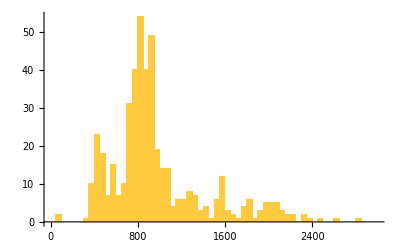

```mathematica
fullgenedepth=Histogram[fullgenomeSNPEFF[[All,Position[header,"DP"][[1,1]]]],{50},PlotRange->{{0,3000},Automatic}]
```

There are two low outliers (BSC1 and HAP1, filtered out below for having too many “.” genotypes):

```mathematica
Select[fullgenomeSNPEFF[[All,Position[header,"DP"][[1,1]]]],#<300&]
```

{91,84}

There are three high outliers (all FLO1, filtered out below for having too many “.” genotypes):

```mathematica
Select[fullgenomeSNPEFF[[All,Position[header,"DP"][[1,1]]]],#>3000&]
```

{15599,15734,17792}

Mean depth:

```mathematica
Mean[fullgenomeSNPEFF[[All,129]]]//N
```

1072.34

### Dropping tRNAs, checking overlapping coding regions (SnpEff), and dropping dubious genes

Dropping tRNAs, which we drop {“tC(GCA)B”,”tE(UUC)G3”,”tK(CUU)E2”,”tS(AGA)M”} and TRT2 (which is tT(CGU)K), but first checking that their annotations from SnpEff do not involve other genes (other than upstream or downstream modifiers):

```mathematica
dropgenes={"tC(GCA)B","tE(UUC)G3","tK(CUU)E2","tS(AGA)M","TRT2"};
```

Depth of coverage for these genes is pretty typical:

```mathematica
Select[fullgenomeSNPEFF,MemberQ[dropgenes,#[[8]]]&][[All,{8,129}]]
Mean[%[[All,2]]]//N
```

{{tC(GCA)B,1316},{tK(CUU)E2,1111},{tE(UUC)G3,398},{TRT2,2091},{tS(AGA)M,885}}

1160.2

Dropping these five tRNAs

```mathematica
Length[fullgenomeSNPEFF];
fullgenomeSNPEFF=Select[fullgenomeSNPEFF,MemberQ[dropgenes,#[[8]]]==False&];
%%-Length[fullgenomeSNPEFF]
```

5

Looking over all genes whose most extreme SnpEff calls involve more than one protein-coding gene:

```mathematica
catSNPEFF={"LOW","MODERATE","HIGH"}; (*Not "MODIFIER"*)
```

```mathematica
Clear[sumFULL]
sumFULL=Table["ERROR",{i,1,Length[fullgenomeSNPEFF]}];
For[i=1,i≤Length[fullgenomeSNPEFF],i++,
temp=StringSplit[fullgenomeSNPEFF[[i,14]],{"|"}];
temp2=Tally[temp];
temp3=Select[temp2,MemberQ[catSNPEFF,#[[1]]]&];
sumFULL[[i]]=Total[temp3][[2]]
]
```

```mathematica
Position[sumFULL,_?(#>1&)]
```

{{84},{120},{227},{229},{296},{317},{356},{380},{439}}

```mathematica
Position[sumFULL,_?(#>2&)]
```

{}

#### #84: YDR269C is dubious, but CCC2 is verified (SGD) [Updated]

```mathematica
fixme=84;
```

```mathematica
fullgenomeSNPEFF[[fixme,8]]
```

YDR269C

Manually swapping for the second gene:

```mathematica
fullgenomeSNPEFF[[fixme]]
```

{chrIV,4,1005804,G,T,283.29,GT:AD:DP:GQ:PL,YDR269C,MODERATE,missense_variant,YDR269C,c.185C>A,p.Thr62Asn,T|missense_variant|MODERATE|YDR269C|YDR269C|transcript|YDR269C_mRNA|protein_coding|1/1|c.185C>A|p.Thr62Asn|185/324|185/324|62/107||,T|missense_variant|MODERATE|CCC2|YDR270W|transcript|YDR270W_mRNA|protein_coding|1/1|c.130G>T|p.Val44Leu|130/3015|130/3015|44/1004||,T|upstream_gene_variant|MODIFIER|HEL2|YDR266C|transcript|YDR266C_mRNA|protein_coding||c.-3781C>A|||||3781|,T|upstream_gene_variant|MODIFIER|CIA1|YDR267C|transcript|YDR267C_mRNA|protein_coding||c.-2302C>A|||||2302|,T|upstream_gene_variant|MODIFIER|GLO2|YDR272W|transcript|YDR272W_mRNA|protein_coding||c.-3206G>T|||||3206|,T|upstream_gene_variant|MODIFIER|DON1|YDR273W|transcript|YDR273W_mRNA|protein_coding||c.-4372G>T|||||4372|,T|downstream_gene_variant|MODIFIER|MSW1|YDR268W|transcript|YDR268W_mRNA|protein_coding||c.*661G>T|||||661|,T|downstream_gene_variant|MODIFIER|YDR271C|YDR271C|transcript|YDR271C_mRNA|protein_coding||c.*2591C>A|||||2591|,0:3,0:3:99:0,109,0:5,0:5:99:0,135,0:3,0:3:99:0,113,0:4,0:4:99:0,104,0:3,0:3:99:0,100,0:4,0:4:99:0,115,0:3,0:3:99:0,100,0:3,0:3:99:0,100,0:4,0:4:99:0,107,0:4,0:4:99:0,100,0:4,0:4:99:0,137,0:3,0:3:99:0,100,0:4,0:4:99:0,109,0:7,0:7:99:0,125,0:3,0:3:99:0,100,0:4,0:4:99:0,141,0:3,0:3:99:0,105,0:3,0:3:99:0,103,0:3,0:3:99:0,109,0:4,0:4:99:0,100,0:3,0:3:99:0,100,0:3,0:3:99:0,114,0:4,0:4:99:0,141,0:3,0:3:99:0,100,0:5,0:5:99:0,128,0:3,0:3:99:0,122,0:5,0:5:99:0,116,1:0,11:11:99:304,0,0:3,0:3:99:0,100,0:3,0:3:99:0,100,0:4,0:4:99:0,155,0:3,0:3:99:0,118,0:3,0:3:99:0,100,0:4,0:4:99:0,135,0:4,0:4:99:0,100,0:3,0:3:99:0,99,0:4,0:4:99:0,104,0:3,0:3:99:0,100,0:3,0:3:99:0,100,0:8,0:8:99:0,148,0:3,0:3:99:0,109,0:4,0:4:99:0,154,0:3,0:3:99:0,103,0:3,0:3:99:0,100,0:3,0:3:99:0,115,0:4,0:4:99:0,132,0:4,0:4:99:0,103,0:4,0:4:99:0,131,0:3,0:3:99:0,100,0:3,0:3:99:0,122,0:3,0:3:99:0,110,0:3,0:3:99:0,100,0:3,0:3:99:0,107,0:3,0:3:99:0,100,0:3,0:3:99:0,100,0:4,0:4:99:0,118,0:3,0:3:99:0,100,0:6,0:6:99:0,131,0:3,0:3:99:0,100,0:3,0:3:99:0,118,0:5,0:5:99:0,122,0:3,0:3:99:0,100,0:4,0:4:99:0,132,0:4,0:4:99:0,131,0:3,0:3:99:0,100,0:3,0:3:99:0,100,0:3,0:3:99:0,113,0:3,0:3:99:0,100,0:3,0:3:99:0,100,0:3,0:3:99:0,109,0:3,0:3:99:0,100,0:3,0:3:99:0,100,0:3,0:3:99:0,112,0:4,0:4:99:0,137,0:3,0:3:99:0,118,0:3,0:3:99:0,100,0:5,0:5:99:0,159,0:3,0:3:99:0,122,0:3,0:3:99:0,109,0:4,0:4:99:0,104,0:3,0:3:99:0,114,0:5,0:5:99:0,170,0:5,0:5:99:0,144,0:4,0:4:99:0,141,0:3,0:3:99:0,122,0:4,0:4:99:0,155,0:10,0:10:99:0,153,0:3,0:3:99:0,100,0:3,0:3:99:0,122,0:3,0:3:99:0,100,0:3,0:3:99:0,118,0:4,0:4:99:0,119,0:4,0:4:99:0,137,0:5,0:5:99:0,141,0:3,0:3:99:0,118,0:4,0:4:99:0,126,0:3,0:3:99:0,100,0:3,0:3:99:0,100,0:4,0:4:99:0,133,0:9,0:9:99:0,157,0:7,0:7:99:0,143,0:4,0:4:99:0,100,0:4,0:4:99:0,129,0:3,0:3:99:0,100,0:6,0:6:99:0,166,0:6,0:6:99:0,180,0:7,0:7:99:0,173,0:4,0:4:99:0,104,0:4,0:4:99:0,109,0:3,0:3:99:0,114,1,0.009091,110,Missing[NotAvailable],426,0.,1,0.009091,60.,Missing[NotAvailable],25.75,Missing[NotAvailable],2.494,Missing[NotAvailable]}

```mathematica
fullgenomeSNPEFF[[fixme]]={"chrIV",4,1005804,"G","T",283.29,"GT:AD:DP:GQ:PL","CCC2","MODERATE","missense_variant","YDR270W","c.130G>T","p.Val44Leu","T|missense_variant|MODERATE|YDR269C|YDR269C|transcript|YDR269C_mRNA|protein_coding|1/1|c.185C>A|p.Thr62Asn|185/324|185/324|62/107||,T|missense_variant|MODERATE|CCC2|YDR270W|transcript|YDR270W_mRNA|protein_coding|1/1|c.130G>T|p.Val44Leu|130/3015|130/3015|44/1004||,T|upstream_gene_variant|MODIFIER|HEL2|YDR266C|transcript|YDR266C_mRNA|protein_coding||c.-3781C>A|||||3781|,T|upstream_gene_variant|MODIFIER|CIA1|YDR267C|transcript|YDR267C_mRNA|protein_coding||c.-2302C>A|||||2302|,T|upstream_gene_variant|MODIFIER|GLO2|YDR272W|transcript|YDR272W_mRNA|protein_coding||c.-3206G>T|||||3206|,T|upstream_gene_variant|MODIFIER|DON1|YDR273W|transcript|YDR273W_mRNA|protein_coding||c.-4372G>T|||||4372|,T|downstream_gene_variant|MODIFIER|MSW1|YDR268W|transcript|YDR268W_mRNA|protein_coding||c.*661G>T|||||661|,T|downstream_gene_variant|MODIFIER|YDR271C|YDR271C|transcript|YDR271C_mRNA|protein_coding||c.*2591C>A|||||2591|","0:3,0:3:99:0,109","0:5,0:5:99:0,135","0:3,0:3:99:0,113","0:4,0:4:99:0,104","0:3,0:3:99:0,100","0:4,0:4:99:0,115","0:3,0:3:99:0,100","0:3,0:3:99:0,100","0:4,0:4:99:0,107","0:4,0:4:99:0,100","0:4,0:4:99:0,137","0:3,0:3:99:0,100","0:4,0:4:99:0,109","0:7,0:7:99:0,125","0:3,0:3:99:0,100","0:4,0:4:99:0,141","0:3,0:3:99:0,105","0:3,0:3:99:0,103","0:3,0:3:99:0,109","0:4,0:4:99:0,100","0:3,0:3:99:0,100","0:3,0:3:99:0,114","0:4,0:4:99:0,141","0:3,0:3:99:0,100","0:5,0:5:99:0,128","0:3,0:3:99:0,122","0:5,0:5:99:0,116","1:0,11:11:99:304,0","0:3,0:3:99:0,100","0:3,0:3:99:0,100","0:4,0:4:99:0,155","0:3,0:3:99:0,118","0:3,0:3:99:0,100","0:4,0:4:99:0,135","0:4,0:4:99:0,100","0:3,0:3:99:0,99","0:4,0:4:99:0,104","0:3,0:3:99:0,100","0:3,0:3:99:0,100","0:8,0:8:99:0,148","0:3,0:3:99:0,109","0:4,0:4:99:0,154","0:3,0:3:99:0,103","0:3,0:3:99:0,100","0:3,0:3:99:0,115","0:4,0:4:99:0,132","0:4,0:4:99:0,103","0:4,0:4:99:0,131","0:3,0:3:99:0,100","0:3,0:3:99:0,122","0:3,0:3:99:0,110","0:3,0:3:99:0,100","0:3,0:3:99:0,107","0:3,0:3:99:0,100","0:3,0:3:99:0,100","0:4,0:4:99:0,118","0:3,0:3:99:0,100","0:6,0:6:99:0,131","0:3,0:3:99:0,100","0:3,0:3:99:0,118","0:5,0:5:99:0,122","0:3,0:3:99:0,100","0:4,0:4:99:0,132","0:4,0:4:99:0,131","0:3,0:3:99:0,100","0:3,0:3:99:0,100","0:3,0:3:99:0,113","0:3,0:3:99:0,100","0:3,0:3:99:0,100","0:3,0:3:99:0,109","0:3,0:3:99:0,100","0:3,0:3:99:0,100","0:3,0:3:99:0,112","0:4,0:4:99:0,137","0:3,0:3:99:0,118","0:3,0:3:99:0,100","0:5,0:5:99:0,159","0:3,0:3:99:0,122","0:3,0:3:99:0,109","0:4,0:4:99:0,104","0:3,0:3:99:0,114","0:5,0:5:99:0,170","0:5,0:5:99:0,144","0:4,0:4:99:0,141","0:3,0:3:99:0,122","0:4,0:4:99:0,155","0:10,0:10:99:0,153","0:3,0:3:99:0,100","0:3,0:3:99:0,122","0:3,0:3:99:0,100","0:3,0:3:99:0,118","0:4,0:4:99:0,119","0:4,0:4:99:0,137","0:5,0:5:99:0,141","0:3,0:3:99:0,118","0:4,0:4:99:0,126","0:3,0:3:99:0,100","0:3,0:3:99:0,100","0:4,0:4:99:0,133","0:9,0:9:99:0,157","0:7,0:7:99:0,143","0:4,0:4:99:0,100","0:4,0:4:99:0,129","0:3,0:3:99:0,100","0:6,0:6:99:0,166","0:6,0:6:99:0,180","0:7,0:7:99:0,173","0:4,0:4:99:0,104","0:4,0:4:99:0,109","0:3,0:3:99:0,114",1,0.009091,110,"NA",426,0.,1,0.009091,60.,"NA",25.75,"NA",2.494,"NA"};
```

#### #120: YFL021C-A is dubious, but GAT1 is verified (SGD) [Updated]

```mathematica
fixme=120;
```

Manually swapping for the second gene:

```mathematica
fullgenomeSNPEFF[[fixme]]
```

{chrVI,6,96312,C,T,839.29,GT:AD:DP:GQ:PL,YFL021C-A,MODERATE,missense_variant,YFL021C-A,c.304G>A,p.Ala102Thr,T|missense_variant|MODERATE|YFL021C-A|YFL021C-A|transcript|YFL021C-A_mRNA|protein_coding|1/1|c.304G>A|p.Ala102Thr|304/855|304/855|102/284||,T|missense_variant|MODERATE|GAT1|YFL021W|transcript|YFL021W_mRNA|protein_coding|1/1|c.347C>T|p.Ala116Val|347/1533|347/1533|116/510||,T|upstream_gene_variant|MODIFIER|FRS2|YFL022C|transcript|YFL022C_mRNA|protein_coding||c.-1302G>A|||||1302|,T|downstream_gene_variant|MODIFIER|BUD27|YFL023W|transcript|YFL023W_mRNA|protein_coding||c.*2936C>T|||||2936|,T|downstream_gene_variant|MODIFIER|PAU5|YFL020C|transcript|YFL020C_mRNA|protein_coding||c.*2919G>A|||||2919|,T|downstream_gene_variant|MODIFIER|YFL019C|YFL019C|transcript|YFL019C_mRNA|protein_coding||c.*3940G>A|||||3940|,0:13,0:13:99:0,393,0:12,0:12:99:0,329,0:8,0:8:99:0,236,0:20,0:20:99:0,484,0:8,0:8:99:0,200,0:14,0:14:99:0,452,0:13,0:13:99:0,239,0:24,0:24:99:0,545,0:10,0:10:99:0,330,0:11,0:11:99:0,348,0:8,0:8:99:0,220,0:10,0:10:99:0,267,0:10,0:10:99:0,297,0:16,0:16:99:0,469,0:11,0:11:99:0,292,0:14,0:14:99:0,399,0:11,0:11:99:0,306,0:9,0:9:99:0,278,0:12,0:12:99:0,314,0:11,0:11:99:0,401,0:8,0:8:99:0,232,0:10,0:10:99:0,294,0:10,0:10:99:0,313,0:16,0:16:99:0,464,0:27,0:27:99:0,714,0:16,0:16:99:0,423,0:11,0:11:99:0,288,0:11,0:11:99:0,251,0:6,0:6:99:0,172,0:8,0:8:99:0,270,0:19,0:19:99:0,514,0:26,0:26:99:0,827,0:23,0:23:99:0,744,0:11,0:11:99:0,358,0:21,0:21:99:0,582,0:10,0:10:99:0,278,0:3,0:3:99:0,109,0:4,0:4:99:0,116,0:7,0:7:99:0,121,0:12,0:12:99:0,367,0:17,0:17:99:0,344,0:21,0:21:99:0,495,0:10,0:10:99:0,270,0:7,0:7:99:0,101,0:11,0:11:99:0,279,0:12,0:12:99:0,331,0:6,0:6:99:0,178,0:9,0:9:99:0,274,0:18,0:18:99:0,587,0:7,0:7:99:0,221,0:6,0:6:99:0,146,0:6,0:6:99:0,124,0:7,0:7:99:0,244,0:12,0:12:99:0,384,0:15,0:15:99:0,474,0:10,0:10:99:0,129,0:15,0:15:99:0,326,0:9,0:9:99:0,214,0:12,0:12:99:0,363,0:8,0:8:99:0,200,0:5,0:5:99:0,140,0:7,0:7:99:0,200,0:11,0:11:99:0,377,0:16,0:16:99:0,323,1:0,25:25:99:860,0,0:18,0:18:99:0,529,0:24,0:24:99:0,702,0:17,0:17:99:0,510,0:17,0:17:99:0,492,0:15,0:15:99:0,504,0:14,0:14:99:0,451,0:10,0:10:99:0,308,0:11,0:11:99:0,276,0:9,0:9:99:0,247,0:11,0:11:99:0,329,0:14,0:14:99:0,421,0:17,0:17:99:0,458,0:28,0:28:99:0,800,0:19,0:19:99:0,562,0:12,0:12:99:0,359,0:16,0:16:99:0,517,0:9,0:9:99:0,266,0:16,0:16:99:0,368,0:8,0:8:99:0,268,0:13,0:13:99:0,358,0:15,0:15:99:0,285,0:15,0:15:99:0,445,0:13,0:13:99:0,452,0:19,0:19:99:0,638,0:7,0:7:99:0,203,0:12,0:12:99:0,306,0:6,0:6:99:0,100,0:9,0:9:99:0,296,0:6,0:6:99:0,200,0:11,0:11:99:0,236,0:12,0:12:99:0,364,0:14,0:14:99:0,396,0:18,0:18:99:0,550,0:19,0:19:99:0,485,0:12,0:12:99:0,247,0:9,0:9:99:0,306,0:12,0:12:99:0,416,0:5,0:5:99:0,100,0:13,0:13:99:0,408,0:9,0:9:99:0,306,0:17,0:17:99:0,364,0:9,0:9:99:0,180,0:8,0:8:99:0,274,0:12,0:12:99:0,302,0:6,0:6:99:0,186,1,0.009091,110,Missing[NotAvailable],1372,0.,1,0.009091,60.,Missing[NotAvailable],33.57,Missing[NotAvailable],2.584,Missing[NotAvailable]}

```mathematica
fullgenomeSNPEFF[[fixme]]={"chrVI",6,96312,"C","T",839.29,"GT:AD:DP:GQ:PL","GAT1","MODERATE","missense_variant","YFL021W","c.347C>T","p.Ala116Val","T|missense_variant|MODERATE|YFL021C-A|YFL021C-A|transcript|YFL021C-A_mRNA|protein_coding|1/1|c.304G>A|p.Ala102Thr|304/855|304/855|102/284||,T|missense_variant|MODERATE|GAT1|YFL021W|transcript|YFL021W_mRNA|protein_coding|1/1|c.347C>T|p.Ala116Val|347/1533|347/1533|116/510||,T|upstream_gene_variant|MODIFIER|FRS2|YFL022C|transcript|YFL022C_mRNA|protein_coding||c.-1302G>A|||||1302|,T|downstream_gene_variant|MODIFIER|BUD27|YFL023W|transcript|YFL023W_mRNA|protein_coding||c.*2936C>T|||||2936|,T|downstream_gene_variant|MODIFIER|PAU5|YFL020C|transcript|YFL020C_mRNA|protein_coding||c.*2919G>A|||||2919|,T|downstream_gene_variant|MODIFIER|YFL019C|YFL019C|transcript|YFL019C_mRNA|protein_coding||c.*3940G>A|||||3940|","0:13,0:13:99:0,393","0:12,0:12:99:0,329","0:8,0:8:99:0,236","0:20,0:20:99:0,484","0:8,0:8:99:0,200","0:14,0:14:99:0,452","0:13,0:13:99:0,239","0:24,0:24:99:0,545","0:10,0:10:99:0,330","0:11,0:11:99:0,348","0:8,0:8:99:0,220","0:10,0:10:99:0,267","0:10,0:10:99:0,297","0:16,0:16:99:0,469","0:11,0:11:99:0,292","0:14,0:14:99:0,399","0:11,0:11:99:0,306","0:9,0:9:99:0,278","0:12,0:12:99:0,314","0:11,0:11:99:0,401","0:8,0:8:99:0,232","0:10,0:10:99:0,294","0:10,0:10:99:0,313","0:16,0:16:99:0,464","0:27,0:27:99:0,714","0:16,0:16:99:0,423","0:11,0:11:99:0,288","0:11,0:11:99:0,251","0:6,0:6:99:0,172","0:8,0:8:99:0,270","0:19,0:19:99:0,514","0:26,0:26:99:0,827","0:23,0:23:99:0,744","0:11,0:11:99:0,358","0:21,0:21:99:0,582","0:10,0:10:99:0,278","0:3,0:3:99:0,109","0:4,0:4:99:0,116","0:7,0:7:99:0,121","0:12,0:12:99:0,367","0:17,0:17:99:0,344","0:21,0:21:99:0,495","0:10,0:10:99:0,270","0:7,0:7:99:0,101","0:11,0:11:99:0,279","0:12,0:12:99:0,331","0:6,0:6:99:0,178","0:9,0:9:99:0,274","0:18,0:18:99:0,587","0:7,0:7:99:0,221","0:6,0:6:99:0,146","0:6,0:6:99:0,124","0:7,0:7:99:0,244","0:12,0:12:99:0,384","0:15,0:15:99:0,474","0:10,0:10:99:0,129","0:15,0:15:99:0,326","0:9,0:9:99:0,214","0:12,0:12:99:0,363","0:8,0:8:99:0,200","0:5,0:5:99:0,140","0:7,0:7:99:0,200","0:11,0:11:99:0,377","0:16,0:16:99:0,323","1:0,25:25:99:860,0","0:18,0:18:99:0,529","0:24,0:24:99:0,702","0:17,0:17:99:0,510","0:17,0:17:99:0,492","0:15,0:15:99:0,504","0:14,0:14:99:0,451","0:10,0:10:99:0,308","0:11,0:11:99:0,276","0:9,0:9:99:0,247","0:11,0:11:99:0,329","0:14,0:14:99:0,421","0:17,0:17:99:0,458","0:28,0:28:99:0,800","0:19,0:19:99:0,562","0:12,0:12:99:0,359","0:16,0:16:99:0,517","0:9,0:9:99:0,266","0:16,0:16:99:0,368","0:8,0:8:99:0,268","0:13,0:13:99:0,358","0:15,0:15:99:0,285","0:15,0:15:99:0,445","0:13,0:13:99:0,452","0:19,0:19:99:0,638","0:7,0:7:99:0,203","0:12,0:12:99:0,306","0:6,0:6:99:0,100","0:9,0:9:99:0,296","0:6,0:6:99:0,200","0:11,0:11:99:0,236","0:12,0:12:99:0,364","0:14,0:14:99:0,396","0:18,0:18:99:0,550","0:19,0:19:99:0,485","0:12,0:12:99:0,247","0:9,0:9:99:0,306","0:12,0:12:99:0,416","0:5,0:5:99:0,100","0:13,0:13:99:0,408","0:9,0:9:99:0,306","0:17,0:17:99:0,364","0:9,0:9:99:0,180","0:8,0:8:99:0,274","0:12,0:12:99:0,302","0:6,0:6:99:0,186",1,0.009091,110,"NA",1372,0.,1,0.009091,60.,"NA",33.57,"NA",2.584,"NA"};
```

#### #227: YJL211C is dubious, but PEX2 is verified (SGD) [Updated]

```mathematica
fixme=227;
```

Manually swapping for the second gene:

```mathematica
fullgenomeSNPEFF[[fixme]]
```

{chrX,10,37037,C,T,1239.29,GT:AD:DP:GQ:PL,YJL211C,MODERATE,missense_variant,YJL211C,c.164G>A,p.Cys55Tyr,T|missense_variant|MODERATE|YJL211C|YJL211C|transcript|YJL211C_mRNA|protein_coding|1/1|c.164G>A|p.Cys55Tyr|164/444|164/444|55/147||,T|missense_variant|MODERATE|PEX2|YJL210W|transcript|YJL210W_mRNA|protein_coding|1/1|c.119C>T|p.Ala40Val|119/816|119/816|40/271||,T|upstream_gene_variant|MODIFIER|OPT1|YJL212C|transcript|YJL212C_mRNA|protein_coding||c.-788G>A|||||788|,T|upstream_gene_variant|MODIFIER|CBP1|YJL209W|transcript|YJL209W_mRNA|protein_coding||c.-968C>T|||||968|,T|downstream_gene_variant|MODIFIER|YJL213W|YJL213W|transcript|YJL213W_mRNA|protein_coding||c.*3879C>T|||||3879|,T|downstream_gene_variant|MODIFIER|NUC1|YJL208C|transcript|YJL208C_mRNA|protein_coding||c.*3157G>A|||||3157|,T|downstream_gene_variant|MODIFIER|LAA1|YJL207C|transcript|YJL207C_mRNA|protein_coding||c.*4352G>A|||||4352|,0:3,0:3:99:0,100,0:8,0:8:99:0,129,0:7,0:7:99:0,189,0:3,0:3:99:0,109,0:4,0:4:99:0,118,0:3,0:3:99:0,111,0:4,0:4:99:0,135,0:3,0:3:99:0,100,0:4,0:4:99:0,135,0:3,0:3:99:0,109,0:3,0:3:99:0,100,0:4,0:4:99:0,119,0:3,0:3:99:0,100,0:4,0:4:99:0,135,0:3,0:3:99:0,110,0:3,0:3:99:0,100,0:6,0:6:99:0,116,0:3,0:3:99:0,100,0:3,0:3:99:0,100,0:3,0:3:99:0,104,0:3,0:3:99:0,109,0:4,0:4:99:0,119,0:3,0:3:99:0,103,0:4,0:4:99:0,114,0:4,0:4:99:0,115,0:4,0:4:99:0,119,0:4,0:4:99:0,110,0:4,0:4:99:0,141,0:3,0:3:99:0,113,0:3,0:3:99:0,100,0:4,0:4:99:0,107,0:3,0:3:99:0,100,0:4,0:4:99:0,110,0:4,0:4:99:0,130,0:3,0:3:99:0,122,0:3,0:3:99:0,100,0:4,0:4:99:0,100,0:4,0:4:99:0,115,0:4,0:4:99:0,137,0:3,0:3:99:0,109,0:3,0:3:99:0,100,0:3,0:3:99:0,105,0:3,0:3:99:0,100,0:4,0:4:99:0,151,0:3,0:3:99:0,110,0:3,0:3:99:0,104,0:8,0:8:99:0,176,0:6,0:6:99:0,119,0:3,0:3:99:0,100,0:3,0:3:99:0,100,0:3,0:3:99:0,113,0:3,0:3:99:0,100,0:3,0:3:99:0,100,0:4,0:4:99:0,100,0:3,0:3:99:0,100,0:3,0:3:99:0,103,0:3,0:3:99:0,118,0:3,0:3:99:0,100,0:3,0:3:99:0,107,0:3,0:3:99:0,107,0:3,0:3:99:0,100,0:7,0:7:99:0,227,0:3,0:3:99:0,109,0:3,0:3:99:0,113,0:3,0:3:99:0,100,0:4,0:4:99:0,139,0:4,0:4:99:0,115,0:4,0:4:99:0,114,1:0,39:39:99:1260,0,0:5,0:5:99:0,132,0:4,0:4:99:0,133,0:3,0:3:99:0,109,0:4,0:4:99:0,110,0:4,0:4:99:0,102,0:3,0:3:99:0,100,0:3,0:3:99:0,103,0:5,0:5:99:0,135,0:5,0:5:99:0,174,0:3,0:3:99:0,100,0:3,0:3:99:0,100,0:3,0:3:99:0,107,0:4,0:4:99:0,135,0:3,0:3:99:0,104,0:4,0:4:99:0,115,0:4,0:4:99:0,128,0:4,0:4:99:0,124,0:5,0:5:99:0,181,0:3,0:3:99:0,100,0:4,0:4:99:0,123,0:3,0:3:99:0,114,0:4,0:4:99:0,132,0:3,0:3:99:0,101,0:3,0:3:99:0,100,0:3,0:3:99:0,109,0:3,0:3:99:0,100,0:4,0:4:99:0,127,0:3,0:3:99:0,117,0:3,0:3:99:0,118,0:3,0:3:99:0,100,0:4,0:4:99:0,111,0:4,0:4:99:0,114,0:4,0:4:99:0,114,0:3,0:3:99:0,100,0:5,0:5:99:0,113,0:4,0:4:99:0,135,0:4,0:4:99:0,122,0:3,0:3:99:0,114,0:3,0:3:99:0,100,0:3,0:3:99:0,100,0:15,0:15:99:0,245,1,0.009091,110,Missing[NotAvailable],452,0.,1,0.009091,60.,Missing[NotAvailable],31.78,Missing[NotAvailable],1.096,Missing[NotAvailable]}

```mathematica
fullgenomeSNPEFF[[fixme]]={"chrX",10,37037,"C","T",1239.29,"GT:AD:DP:GQ:PL","PEX2","MODERATE","missense_variant","YJL210W","c.119C>T","p.Ala40Val","T|missense_variant|MODERATE|YJL211C|YJL211C|transcript|YJL211C_mRNA|protein_coding|1/1|c.164G>A|p.Cys55Tyr|164/444|164/444|55/147||,T|missense_variant|MODERATE|PEX2|YJL210W|transcript|YJL210W_mRNA|protein_coding|1/1|c.119C>T|p.Ala40Val|119/816|119/816|40/271||,T|upstream_gene_variant|MODIFIER|OPT1|YJL212C|transcript|YJL212C_mRNA|protein_coding||c.-788G>A|||||788|,T|upstream_gene_variant|MODIFIER|CBP1|YJL209W|transcript|YJL209W_mRNA|protein_coding||c.-968C>T|||||968|,T|downstream_gene_variant|MODIFIER|YJL213W|YJL213W|transcript|YJL213W_mRNA|protein_coding||c.*3879C>T|||||3879|,T|downstream_gene_variant|MODIFIER|NUC1|YJL208C|transcript|YJL208C_mRNA|protein_coding||c.*3157G>A|||||3157|,T|downstream_gene_variant|MODIFIER|LAA1|YJL207C|transcript|YJL207C_mRNA|protein_coding||c.*4352G>A|||||4352|","0:3,0:3:99:0,100","0:8,0:8:99:0,129","0:7,0:7:99:0,189","0:3,0:3:99:0,109","0:4,0:4:99:0,118","0:3,0:3:99:0,111","0:4,0:4:99:0,135","0:3,0:3:99:0,100","0:4,0:4:99:0,135","0:3,0:3:99:0,109","0:3,0:3:99:0,100","0:4,0:4:99:0,119","0:3,0:3:99:0,100","0:4,0:4:99:0,135","0:3,0:3:99:0,110","0:3,0:3:99:0,100","0:6,0:6:99:0,116","0:3,0:3:99:0,100","0:3,0:3:99:0,100","0:3,0:3:99:0,104","0:3,0:3:99:0,109","0:4,0:4:99:0,119","0:3,0:3:99:0,103","0:4,0:4:99:0,114","0:4,0:4:99:0,115","0:4,0:4:99:0,119","0:4,0:4:99:0,110","0:4,0:4:99:0,141","0:3,0:3:99:0,113","0:3,0:3:99:0,100","0:4,0:4:99:0,107","0:3,0:3:99:0,100","0:4,0:4:99:0,110","0:4,0:4:99:0,130","0:3,0:3:99:0,122","0:3,0:3:99:0,100","0:4,0:4:99:0,100","0:4,0:4:99:0,115","0:4,0:4:99:0,137","0:3,0:3:99:0,109","0:3,0:3:99:0,100","0:3,0:3:99:0,105","0:3,0:3:99:0,100","0:4,0:4:99:0,151","0:3,0:3:99:0,110","0:3,0:3:99:0,104","0:8,0:8:99:0,176","0:6,0:6:99:0,119","0:3,0:3:99:0,100","0:3,0:3:99:0,100","0:3,0:3:99:0,113","0:3,0:3:99:0,100","0:3,0:3:99:0,100","0:4,0:4:99:0,100","0:3,0:3:99:0,100","0:3,0:3:99:0,103","0:3,0:3:99:0,118","0:3,0:3:99:0,100","0:3,0:3:99:0,107","0:3,0:3:99:0,107","0:3,0:3:99:0,100","0:7,0:7:99:0,227","0:3,0:3:99:0,109","0:3,0:3:99:0,113","0:3,0:3:99:0,100","0:4,0:4:99:0,139","0:4,0:4:99:0,115","0:4,0:4:99:0,114","1:0,39:39:99:1260,0","0:5,0:5:99:0,132","0:4,0:4:99:0,133","0:3,0:3:99:0,109","0:4,0:4:99:0,110","0:4,0:4:99:0,102","0:3,0:3:99:0,100","0:3,0:3:99:0,103","0:5,0:5:99:0,135","0:5,0:5:99:0,174","0:3,0:3:99:0,100","0:3,0:3:99:0,100","0:3,0:3:99:0,107","0:4,0:4:99:0,135","0:3,0:3:99:0,104","0:4,0:4:99:0,115","0:4,0:4:99:0,128","0:4,0:4:99:0,124","0:5,0:5:99:0,181","0:3,0:3:99:0,100","0:4,0:4:99:0,123","0:3,0:3:99:0,114","0:4,0:4:99:0,132","0:3,0:3:99:0,101","0:3,0:3:99:0,100","0:3,0:3:99:0,109","0:3,0:3:99:0,100","0:4,0:4:99:0,127","0:3,0:3:99:0,117","0:3,0:3:99:0,118","0:3,0:3:99:0,100","0:4,0:4:99:0,111","0:4,0:4:99:0,114","0:4,0:4:99:0,114","0:3,0:3:99:0,100","0:5,0:5:99:0,113","0:4,0:4:99:0,135","0:4,0:4:99:0,122","0:3,0:3:99:0,114","0:3,0:3:99:0,100","0:3,0:3:99:0,100","0:15,0:15:99:0,245",1,0.009091,110,"NA",452,0.,1,0.009091,60.,"NA",31.78,"NA",1.096,"NA"};
```

#### #229: BUD19 is dubious [HIGH], but RPL39 is verified [LOW] (SGD) [Updated]

```mathematica
fixme=229;
```

Manually swapping for the second gene:

```mathematica
fullgenomeSNPEFF[[fixme]]
```

{chrX,10,76405,G,A,839.29,GT:AD:DP:GQ:PL,BUD19,HIGH,stop_gained,YJL188C,c.106C>T,p.Gln36*,A|stop_gained|HIGH|BUD19|YJL188C|transcript|YJL188C_mRNA|protein_coding|1/1|c.106C>T|p.Gln36*|106/309|106/309|36/102||,A|synonymous_variant|LOW|RPL39|YJL189W|transcript|YJL189W_mRNA|protein_coding|2/2|c.87G>A|p.Leu29Leu|87/156|87/156|29/51||,A|upstream_gene_variant|MODIFIER|SOP4|YJL192C|transcript|YJL192C_mRNA|protein_coding||c.-2991C>T|||||2991|,A|upstream_gene_variant|MODIFIER|RPS22A|YJL190C|transcript|YJL190C_mRNA|protein_coding||c.-1103C>T|||||1103|,A|upstream_gene_variant|MODIFIER|MNN5|YJL186W|transcript|YJL186W_mRNA|protein_coding||c.-3750G>A|||||3750|,A|downstream_gene_variant|MODIFIER|YJL193W|YJL193W|transcript|YJL193W_mRNA|protein_coding||c.*3831G>A|||||3831|,A|downstream_gene_variant|MODIFIER|RPS14B|YJL191W|transcript|YJL191W_mRNA|protein_coding||c.*1794G>A|||||1794|,A|downstream_gene_variant|MODIFIER|SWE1|YJL187C|transcript|YJL187C_mRNA|protein_coding||c.*398C>T|||||398|,0:11,0:11:99:0,164,0:9,0:9:99:0,270,0:10,0:10:99:0,200,0:8,0:8:99:0,103,0:3,0:3:99:0,118,0:12,0:12:99:0,271,0:4,0:4:99:0,135,0:7,0:7:99:0,155,0:7,0:7:99:0,111,0:14,0:14:99:0,458,0:8,0:8:99:0,225,0:6,0:6:99:0,139,0:7,0:7:99:0,152,0:9,0:9:99:0,224,0:3,0:3:99:0,110,0:8,0:8:99:0,227,0:5,0:5:99:0,159,0:6,0:6:99:0,153,0:7,0:7:99:0,146,0:11,0:11:99:0,277,0:7,0:7:99:0,223,0:9,0:9:99:0,197,0:3,0:3:99:0,118,0:13,0:13:99:0,402,0:13,0:13:99:0,264,0:13,0:13:99:0,107,0:7,0:7:99:0,121,0:10,0:10:99:0,165,0:8,0:8:99:0,217,0:9,0:9:99:0,315,0:7,0:7:99:0,135,0:20,0:20:99:0,551,0:14,0:14:99:0,262,0:12,0:12:99:0,209,0:7,0:7:99:0,148,0:8,0:8:99:0,140,0:3,0:3:99:0,100,0:5,0:5:99:0,135,0:4,0:4:99:0,116,0:8,0:8:99:0,253,0:3,0:3:99:0,100,0:11,0:11:99:0,314,0:10,0:10:99:0,240,0:4,0:4:99:0,103,0:5,0:5:99:0,159,0:11,0:11:99:0,150,0:3,0:3:99:0,118,0:7,0:7:99:0,136,0:8,0:8:99:0,129,0:9,0:9:99:0,180,0:5,0:5:99:0,105,0:7,0:7:99:0,127,0:3,0:3:99:0,109,0:4,0:4:99:0,133,0:5,0:5:99:0,115,0:10,0:10:99:0,101,0:3,0:3:99:0,117,0:3,0:3:99:0,100,0:4,0:4:99:0,140,0:3,0:3:99:0,107,0:6,0:6:99:0,218,0:6,0:6:99:0,127,0:8,0:8:99:0,169,0:10,0:10:99:0,311,0:5,0:5:99:0,159,0:5,0:5:99:0,118,0:7,0:7:99:0,204,0:9,0:9:99:0,250,0:15,0:15:99:0,182,0:7,0:7:99:0,172,0:13,0:13:99:0,197,0:7,0:7:99:0,198,0:9,0:9:99:0,177,0:9,0:9:99:0,157,0:4,0:4:99:0,127,0:6,0:6:99:0,113,0:6,0:6:99:0,135,0:20,0:20:99:0,348,0:6,0:6:99:0,135,0:5,0:5:99:0,173,0:12,0:12:99:0,338,0:10,0:10:99:0,180,0:15,0:15:99:0,143,0:12,0:12:99:0,355,0:4,0:4:99:0,128,0:14,0:14:99:0,174,0:12,0:12:99:0,139,0:14,0:14:99:0,157,0:12,0:12:99:0,339,0:9,0:9:99:0,124,0:8,0:8:99:0,208,0:3,0:3:99:0,100,0:7,0:7:99:0,184,1:0,24:24:99:860,0,0:8,0:8:99:0,196,0:5,0:5:99:0,102,0:8,0:8:99:0,120,0:5,0:5:99:0,135,0:7,0:7:99:0,118,0:10,0:10:99:0,136,0:12,0:12:99:0,194,0:5,0:5:99:0,135,0:9,0:9:99:0,178,0:8,0:8:99:0,245,0:3,0:3:99:0,118,0:4,0:4:99:0,122,0:11,0:11:99:0,320,0:11,0:11:99:0,200,0:6,0:6:99:0,124,0:6,0:6:99:0,185,1,0.009091,110,Missing[NotAvailable],890,0.,1,0.009091,60.,Missing[NotAvailable],34.97,Missing[NotAvailable],1.519,Missing[NotAvailable]}

```mathematica
fullgenomeSNPEFF[[fixme]]={"chrX",10,76405,"G","A",839.29,"GT:AD:DP:GQ:PL","RPL39","LOW","synonymous_variant","YJL189W","c.87G>A","p.Leu29Leu","A|stop_gained|HIGH|BUD19|YJL188C|transcript|YJL188C_mRNA|protein_coding|1/1|c.106C>T|p.Gln36*|106/309|106/309|36/102||,A|synonymous_variant|LOW|RPL39|YJL189W|transcript|YJL189W_mRNA|protein_coding|2/2|c.87G>A|p.Leu29Leu|87/156|87/156|29/51||,A|upstream_gene_variant|MODIFIER|SOP4|YJL192C|transcript|YJL192C_mRNA|protein_coding||c.-2991C>T|||||2991|,A|upstream_gene_variant|MODIFIER|RPS22A|YJL190C|transcript|YJL190C_mRNA|protein_coding||c.-1103C>T|||||1103|,A|upstream_gene_variant|MODIFIER|MNN5|YJL186W|transcript|YJL186W_mRNA|protein_coding||c.-3750G>A|||||3750|,A|downstream_gene_variant|MODIFIER|YJL193W|YJL193W|transcript|YJL193W_mRNA|protein_coding||c.*3831G>A|||||3831|,A|downstream_gene_variant|MODIFIER|RPS14B|YJL191W|transcript|YJL191W_mRNA|protein_coding||c.*1794G>A|||||1794|,A|downstream_gene_variant|MODIFIER|SWE1|YJL187C|transcript|YJL187C_mRNA|protein_coding||c.*398C>T|||||398|","0:11,0:11:99:0,164","0:9,0:9:99:0,270","0:10,0:10:99:0,200","0:8,0:8:99:0,103","0:3,0:3:99:0,118","0:12,0:12:99:0,271","0:4,0:4:99:0,135","0:7,0:7:99:0,155","0:7,0:7:99:0,111","0:14,0:14:99:0,458","0:8,0:8:99:0,225","0:6,0:6:99:0,139","0:7,0:7:99:0,152","0:9,0:9:99:0,224","0:3,0:3:99:0,110","0:8,0:8:99:0,227","0:5,0:5:99:0,159","0:6,0:6:99:0,153","0:7,0:7:99:0,146","0:11,0:11:99:0,277","0:7,0:7:99:0,223","0:9,0:9:99:0,197","0:3,0:3:99:0,118","0:13,0:13:99:0,402","0:13,0:13:99:0,264","0:13,0:13:99:0,107","0:7,0:7:99:0,121","0:10,0:10:99:0,165","0:8,0:8:99:0,217","0:9,0:9:99:0,315","0:7,0:7:99:0,135","0:20,0:20:99:0,551","0:14,0:14:99:0,262","0:12,0:12:99:0,209","0:7,0:7:99:0,148","0:8,0:8:99:0,140","0:3,0:3:99:0,100","0:5,0:5:99:0,135","0:4,0:4:99:0,116","0:8,0:8:99:0,253","0:3,0:3:99:0,100","0:11,0:11:99:0,314","0:10,0:10:99:0,240","0:4,0:4:99:0,103","0:5,0:5:99:0,159","0:11,0:11:99:0,150","0:3,0:3:99:0,118","0:7,0:7:99:0,136","0:8,0:8:99:0,129","0:9,0:9:99:0,180","0:5,0:5:99:0,105","0:7,0:7:99:0,127","0:3,0:3:99:0,109","0:4,0:4:99:0,133","0:5,0:5:99:0,115","0:10,0:10:99:0,101","0:3,0:3:99:0,117","0:3,0:3:99:0,100","0:4,0:4:99:0,140","0:3,0:3:99:0,107","0:6,0:6:99:0,218","0:6,0:6:99:0,127","0:8,0:8:99:0,169","0:10,0:10:99:0,311","0:5,0:5:99:0,159","0:5,0:5:99:0,118","0:7,0:7:99:0,204","0:9,0:9:99:0,250","0:15,0:15:99:0,182","0:7,0:7:99:0,172","0:13,0:13:99:0,197","0:7,0:7:99:0,198","0:9,0:9:99:0,177","0:9,0:9:99:0,157","0:4,0:4:99:0,127","0:6,0:6:99:0,113","0:6,0:6:99:0,135","0:20,0:20:99:0,348","0:6,0:6:99:0,135","0:5,0:5:99:0,173","0:12,0:12:99:0,338","0:10,0:10:99:0,180","0:15,0:15:99:0,143","0:12,0:12:99:0,355","0:4,0:4:99:0,128","0:14,0:14:99:0,174","0:12,0:12:99:0,139","0:14,0:14:99:0,157","0:12,0:12:99:0,339","0:9,0:9:99:0,124","0:8,0:8:99:0,208","0:3,0:3:99:0,100","0:7,0:7:99:0,184","1:0,24:24:99:860,0","0:8,0:8:99:0,196","0:5,0:5:99:0,102","0:8,0:8:99:0,120","0:5,0:5:99:0,135","0:7,0:7:99:0,118","0:10,0:10:99:0,136","0:12,0:12:99:0,194","0:5,0:5:99:0,135","0:9,0:9:99:0,178","0:8,0:8:99:0,245","0:3,0:3:99:0,118","0:4,0:4:99:0,122","0:11,0:11:99:0,320","0:11,0:11:99:0,200","0:6,0:6:99:0,124","0:6,0:6:99:0,185",1,0.009091,110,"NA",890,0.,1,0.009091,60.,"NA",34.97,"NA",1.519,"NA"};
```

#### #296: VPS63 is uncharacterized, but YPT6 is verified (SGD) [Updated]

```mathematica
fixme=296;
```

Manually swapping for the second gene :

```mathematica
fullgenomeSNPEFF[[fixme]]
```

{chrXII,12,668352,C,G,549.29,GT:AD:DP:GQ:PL,VPS63,MODERATE,missense_variant,YLR261C,c.212G>C,p.Ser71Thr,G|missense_variant|MODERATE|VPS63|YLR261C|transcript|YLR261C_mRNA|protein_coding|1/1|c.212G>C|p.Ser71Thr|212/327|212/327|71/108||,G|missense_variant|MODERATE|YPT6|YLR262C|transcript|YLR262C_mRNA|protein_coding|1/1|c.540G>C|p.Glu180Asp|540/648|540/648|180/215||,G|upstream_gene_variant|MODIFIER|HSP60|YLR259C|transcript|YLR259C_mRNA|protein_coding||c.-3350G>C|||||3350|,G|upstream_gene_variant|MODIFIER|RED1|YLR263W|transcript|YLR263W_mRNA|protein_coding||c.-1988C>G|||||1988|,G|upstream_gene_variant|MODIFIER|RPS28B|YLR264W|transcript|YLR264W_mRNA|protein_coding||c.-4779C>G|||||4779|,G|downstream_gene_variant|MODIFIER|LCB5|YLR260W|transcript|YLR260W_mRNA|protein_coding||c.*445C>G|||||445|,G|downstream_gene_variant|MODIFIER|TMA7|YLR262C-A|transcript|YLR262C-A_mRNA|protein_coding||c.*1116G>C|||||1116|,0:15,0:15:99:0,486,0:33,0:33:99:0,1029,0:20,0:20:99:0,656,0:18,0:18:99:0,643,0:9,0:9:99:0,253,0:20,0:20:99:0,718,0:19,0:19:99:0,660,0:19,0:19:99:0,575,0:7,0:7:99:0,217,0:10,0:10:99:0,341,0:11,0:11:99:0,278,0:27,0:27:99:0,895,0:14,0:14:99:0,489,0:14,0:14:99:0,405,0:17,0:17:99:0,519,0:14,0:14:99:0,468,0:12,0:12:99:0,423,1:0,15:15:99:570,0,0:9,0:9:99:0,270,0:19,0:19:99:0,570,0:17,0:17:99:0,572,0:11,0:11:99:0,360,0:14,0:14:99:0,436,0:16,0:16:99:0,530,0:11,0:11:99:0,365,0:24,0:24:99:0,847,0:18,0:18:99:0,657,0:7,0:7:99:0,238,0:11,0:11:99:0,336,0:14,0:14:99:0,341,0:21,0:21:99:0,765,0:22,0:22:99:0,790,0:28,0:28:99:0,900,0:10,0:10:99:0,331,0:24,0:24:99:0,822,0:9,0:9:99:0,317,0:3,0:3:99:0,100,0:5,0:5:99:0,128,0:8,0:8:99:0,239,0:10,0:10:99:0,364,0:11,0:11:99:0,292,0:21,0:21:99:0,635,0:19,0:19:99:0,558,0:8,0:8:99:0,278,0:11,0:11:99:0,403,0:14,0:14:99:0,428,0:18,0:18:99:0,628,0:12,0:12:99:0,379,0:13,0:13:99:0,474,0:14,0:14:99:0,473,0:13,0:13:99:0,423,0:17,0:17:99:0,595,0:4,0:4:99:0,129,0:7,0:7:99:0,150,0:8,0:8:99:0,274,0:12,0:12:99:0,422,0:19,0:19:99:0,619,0:12,0:12:99:0,377,0:14,0:14:99:0,341,0:18,0:18:99:0,605,0:8,0:8:99:0,277,0:12,0:12:99:0,372,0:19,0:19:99:0,592,0:15,0:15:99:0,557,0:12,0:12:99:0,437,0:21,0:21:99:0,660,0:17,0:17:99:0,560,0:15,0:15:99:0,487,0:28,0:28:99:0,905,0:14,0:14:99:0,409,0:20,0:20:99:0,685,0:8,0:8:99:0,287,0:19,0:19:99:0,698,0:17,0:17:99:0,561,0:24,0:24:99:0,811,0:17,0:17:99:0,632,0:10,0:10:99:0,370,0:17,0:17:99:0,555,0:20,0:20:99:0,668,0:19,0:19:99:0,611,0:24,0:24:99:0,812,0:17,0:17:99:0,597,0:20,0:20:99:0,706,0:17,0:17:99:0,596,0:15,0:15:99:0,505,0:26,0:26:99:0,943,0:16,0:16:99:0,539,0:15,0:15:99:0,548,0:16,0:16:99:0,534,0:16,0:16:99:0,459,0:18,0:18:99:0,602,0:14,0:14:99:0,324,0:13,0:13:99:0,440,0:13,0:13:99:0,434,0:13,0:13:99:0,450,0:11,0:11:99:0,365,0:23,0:23:99:0,801,0:13,0:13:99:0,413,0:19,0:19:99:0,574,0:13,0:13:99:0,393,0:18,0:18:99:0,627,0:9,0:9:99:0,281,0:17,0:17:99:0,585,0:15,0:15:99:0,540,0:12,0:12:99:0,315,0:18,0:18:99:0,563,0:15,0:15:99:0,512,0:15,0:15:99:0,563,0:8,0:8:99:0,229,0:7,0:7:99:0,237,1,0.009091,110,Missing[NotAvailable],1668,0.,1,0.009091,60.,Missing[NotAvailable],33.61,Missing[NotAvailable],0.818,Missing[NotAvailable]}

```mathematica
fullgenomeSNPEFF[[fixme]]={"chrXII",12,668352,"C","G",549.29,"GT:AD:DP:GQ:PL","YPT6","MODERATE","missense_variant","YLR261C","c.540G>C","p.Glu180Asp","G|missense_variant|MODERATE|VPS63|YLR261C|transcript|YLR261C_mRNA|protein_coding|1/1|c.212G>C|p.Ser71Thr|212/327|212/327|71/108||,G|missense_variant|MODERATE|YPT6|YLR262C|transcript|YLR262C_mRNA|protein_coding|1/1|c.540G>C|p.Glu180Asp|540/648|540/648|180/215||,G|upstream_gene_variant|MODIFIER|HSP60|YLR259C|transcript|YLR259C_mRNA|protein_coding||c.-3350G>C|||||3350|,G|upstream_gene_variant|MODIFIER|RED1|YLR263W|transcript|YLR263W_mRNA|protein_coding||c.-1988C>G|||||1988|,G|upstream_gene_variant|MODIFIER|RPS28B|YLR264W|transcript|YLR264W_mRNA|protein_coding||c.-4779C>G|||||4779|,G|downstream_gene_variant|MODIFIER|LCB5|YLR260W|transcript|YLR260W_mRNA|protein_coding||c.*445C>G|||||445|,G|downstream_gene_variant|MODIFIER|TMA7|YLR262C-A|transcript|YLR262C-A_mRNA|protein_coding||c.*1116G>C|||||1116|","0:15,0:15:99:0,486","0:33,0:33:99:0,1029","0:20,0:20:99:0,656","0:18,0:18:99:0,643","0:9,0:9:99:0,253","0:20,0:20:99:0,718","0:19,0:19:99:0,660","0:19,0:19:99:0,575","0:7,0:7:99:0,217","0:10,0:10:99:0,341","0:11,0:11:99:0,278","0:27,0:27:99:0,895","0:14,0:14:99:0,489","0:14,0:14:99:0,405","0:17,0:17:99:0,519","0:14,0:14:99:0,468","0:12,0:12:99:0,423","1:0,15:15:99:570,0","0:9,0:9:99:0,270","0:19,0:19:99:0,570","0:17,0:17:99:0,572","0:11,0:11:99:0,360","0:14,0:14:99:0,436","0:16,0:16:99:0,530","0:11,0:11:99:0,365","0:24,0:24:99:0,847","0:18,0:18:99:0,657","0:7,0:7:99:0,238","0:11,0:11:99:0,336","0:14,0:14:99:0,341","0:21,0:21:99:0,765","0:22,0:22:99:0,790","0:28,0:28:99:0,900","0:10,0:10:99:0,331","0:24,0:24:99:0,822","0:9,0:9:99:0,317","0:3,0:3:99:0,100","0:5,0:5:99:0,128","0:8,0:8:99:0,239","0:10,0:10:99:0,364","0:11,0:11:99:0,292","0:21,0:21:99:0,635","0:19,0:19:99:0,558","0:8,0:8:99:0,278","0:11,0:11:99:0,403","0:14,0:14:99:0,428","0:18,0:18:99:0,628","0:12,0:12:99:0,379","0:13,0:13:99:0,474","0:14,0:14:99:0,473","0:13,0:13:99:0,423","0:17,0:17:99:0,595","0:4,0:4:99:0,129","0:7,0:7:99:0,150","0:8,0:8:99:0,274","0:12,0:12:99:0,422","0:19,0:19:99:0,619","0:12,0:12:99:0,377","0:14,0:14:99:0,341","0:18,0:18:99:0,605","0:8,0:8:99:0,277","0:12,0:12:99:0,372","0:19,0:19:99:0,592","0:15,0:15:99:0,557","0:12,0:12:99:0,437","0:21,0:21:99:0,660","0:17,0:17:99:0,560","0:15,0:15:99:0,487","0:28,0:28:99:0,905","0:14,0:14:99:0,409","0:20,0:20:99:0,685","0:8,0:8:99:0,287","0:19,0:19:99:0,698","0:17,0:17:99:0,561","0:24,0:24:99:0,811","0:17,0:17:99:0,632","0:10,0:10:99:0,370","0:17,0:17:99:0,555","0:20,0:20:99:0,668","0:19,0:19:99:0,611","0:24,0:24:99:0,812","0:17,0:17:99:0,597","0:20,0:20:99:0,706","0:17,0:17:99:0,596","0:15,0:15:99:0,505","0:26,0:26:99:0,943","0:16,0:16:99:0,539","0:15,0:15:99:0,548","0:16,0:16:99:0,534","0:16,0:16:99:0,459","0:18,0:18:99:0,602","0:14,0:14:99:0,324","0:13,0:13:99:0,440","0:13,0:13:99:0,434","0:13,0:13:99:0,450","0:11,0:11:99:0,365","0:23,0:23:99:0,801","0:13,0:13:99:0,413","0:19,0:19:99:0,574","0:13,0:13:99:0,393","0:18,0:18:99:0,627","0:9,0:9:99:0,281","0:17,0:17:99:0,585","0:15,0:15:99:0,540","0:12,0:12:99:0,315","0:18,0:18:99:0,563","0:15,0:15:99:0,512","0:15,0:15:99:0,563","0:8,0:8:99:0,229","0:7,0:7:99:0,237",1,0.009091,110,"NA",1668,0.,1,0.009091,60.,"NA",33.61,"NA",0.818,"NA"};
```

#### #317: VRP1 is verified, but OPI9 is dubious (SGD) [Kept as is]

```mathematica
fixme=317;
```

Kept as is:

```mathematica
fullgenomeSNPEFF[[fixme]]
```

{chrXII,12,804694,G,A,355.29,GT:AD:DP:GQ:PL,VRP1,MODERATE,missense_variant,YLR337C,c.413C>T,p.Ala138Val,A|missense_variant|MODERATE|VRP1|YLR337C|transcript|YLR337C_mRNA|protein_coding|1/1|c.413C>T|p.Ala138Val|413/2454|413/2454|138/817||,A|missense_variant|MODERATE|OPI9|YLR338W|transcript|YLR338W_mRNA|protein_coding|1/1|c.349G>A|p.Ala117Thr|349/858|349/858|117/285||,A|upstream_gene_variant|MODIFIER|SGD1|YLR336C|transcript|YLR336C_mRNA|protein_coding||c.-2298C>T|||||2298|,A|upstream_gene_variant|MODIFIER|RPP0|YLR340W|transcript|YLR340W_mRNA|protein_coding||c.-1193G>A|||||1193|,A|upstream_gene_variant|MODIFIER|SPO77|YLR341W|transcript|YLR341W_mRNA|protein_coding||c.-2691G>A|||||2691|,A|downstream_gene_variant|MODIFIER|YLR339C|YLR339C|transcript|YLR339C_mRNA|protein_coding||c.*1090C>T|||||1090|,0:10,0:10:99:0,224,0:18,0:18:99:0,224,0:7,0:7:99:0,228,0:8,0:8:99:0,201,0:5,0:5:99:0,118,0:13,0:13:99:0,378,0:10,0:10:99:0,180,0:11,0:11:99:0,244,0:7,0:7:99:0,228,0:5,0:5:99:0,150,0:5,0:5:99:0,135,0:17,0:17:99:0,371,0:4,0:4:99:0,128,0:7,0:7:99:0,187,0:8,0:8:99:0,246,0:11,0:11:99:0,295,0:5,0:5:99:0,115,0:5,0:5:99:0,122,0:5,0:5:99:0,132,0:9,0:9:99:0,251,0:7,0:7:99:0,159,0:5,0:5:99:0,180,0:11,0:11:99:0,338,0:13,0:13:99:0,357,0:3,0:3:99:0,107,0:14,0:14:99:0,407,0:11,0:11:99:0,306,0:7,0:7:99:0,217,0:4,0:4:99:0,99,0:6,0:6:99:0,135,0:14,0:14:99:0,407,0:12,0:12:99:0,245,0:16,0:16:99:0,568,0:6,0:6:99:0,148,0:12,0:12:99:0,346,0:5,0:5:99:0,140,0:3,0:3:99:0,104,0:5,0:5:99:0,122,0:4,0:4:99:0,135,0:4,0:4:99:0,113,0:8,0:8:99:0,214,0:12,0:12:99:0,392,0:6,0:6:99:0,218,0:8,0:8:99:0,161,0:4,0:4:99:0,119,0:10,0:10:99:0,317,0:4,0:4:99:0,122,0:8,0:8:99:0,192,0:10,0:10:99:0,262,0:10,0:10:99:0,197,0:4,0:4:99:0,122,0:6,0:6:99:0,204,0:4,0:4:99:0,99,0:4,0:4:99:0,154,0:5,0:5:99:0,135,0:8,0:8:99:0,162,0:8,0:8:99:0,173,0:7,0:7:99:0,191,0:8,0:8:99:0,250,0:6,0:6:99:0,190,0:7,0:7:99:0,191,0:7,0:7:99:0,228,0:4,0:4:99:0,135,0:10,0:10:99:0,263,1:0,10:10:99:376,0,0:9,0:9:99:0,225,0:13,0:13:99:0,430,0:9,0:9:99:0,336,0:18,0:18:99:0,585,0:11,0:11:99:0,283,0:11,0:11:99:0,203,0:8,0:8:99:0,103,0:9,0:9:99:0,184,0:9,0:9:99:0,240,0:11,0:11:99:0,302,0:10,0:10:99:0,351,0:8,0:8:99:0,279,0:16,0:16:99:0,521,0:12,0:12:99:0,345,0:8,0:8:99:0,241,0:14,0:14:99:0,509,0:8,0:8:99:0,273,0:12,0:12:99:0,435,0:13,0:13:99:0,356,0:7,0:7:99:0,209,0:11,0:11:99:0,393,0:7,0:7:99:0,225,0:8,0:8:99:0,264,0:9,0:9:99:0,232,0:7,0:7:99:0,225,0:9,0:9:99:0,296,0:4,0:4:99:0,133,0:7,0:7:99:0,219,0:9,0:9:99:0,300,0:8,0:8:99:0,221,0:7,0:7:99:0,196,0:10,0:10:99:0,276,0:7,0:7:99:0,184,0:12,0:12:99:0,358,0:6,0:6:99:0,214,0:10,0:10:99:0,316,0:9,0:9:99:0,192,0:6,0:6:99:0,164,0:12,0:12:99:0,259,0:5,0:5:99:0,113,0:9,0:9:99:0,162,0:7,0:7:99:0,247,0:9,0:9:99:0,210,0:5,0:5:99:0,128,0:4,0:4:99:0,107,1,0.009091,110,Missing[NotAvailable],924,0.,1,0.009091,60.,Missing[NotAvailable],29.03,Missing[NotAvailable],1.609,Missing[NotAvailable]}

#### #356: DDR48 is verified, but YMR173W-A is dubious (SGD) [Kept as is]

```mathematica
fixme=356;
```

Kept as is:

```mathematica
fullgenomeSNPEFF[[fixme]]
```

{chrXIII,13,609388,A,G,342.29,GT:AD:DP:GQ:PL,DDR48,MODERATE,missense_variant,YMR173W,c.700A>G,p.Asn234Asp,G|missense_variant|MODERATE|DDR48|YMR173W|transcript|YMR173W_mRNA|protein_coding|1/1|c.700A>G|p.Asn234Asp|700/1293|700/1293|234/430||,G|synonymous_variant|LOW|YMR173W-A|YMR173W-A|transcript|YMR173W-A_mRNA|protein_coding|1/1|c.492A>G|p.Leu164Leu|492/1185|492/1185|164/394||,G|upstream_gene_variant|MODIFIER|EAR1|YMR171C|transcript|YMR171C_mRNA|protein_coding||c.-3868T>C|||||3868|,G|upstream_gene_variant|MODIFIER|YMR172C-A|YMR172C-A|transcript|YMR172C-A_mRNA|protein_coding||c.-1177T>C|||||1177|,G|upstream_gene_variant|MODIFIER|SIP18|YMR175W|transcript|YMR175W_mRNA|protein_coding||c.-1628A>G|||||1628|,G|upstream_gene_variant|MODIFIER|YMR175W-A|YMR175W-A|transcript|YMR175W-A_mRNA|protein_coding||c.-1926A>G|||||1926|,G|upstream_gene_variant|MODIFIER|ECM5|YMR176W|transcript|YMR176W_mRNA|protein_coding||c.-2352A>G|||||2352|,G|downstream_gene_variant|MODIFIER|HOT1|YMR172W|transcript|YMR172W_mRNA|protein_coding||c.*1248A>G|||||1248|,G|downstream_gene_variant|MODIFIER|PAI3|YMR174C|transcript|YMR174C_mRNA|protein_coding||c.*771T>C|||||771|,0:7,0:7:99:0,159,0:11,0:11:99:0,111,0:8,0:8:99:0,170,0:7,0:7:99:0,246,0:5,0:5:99:0,103,0:9,0:9:99:0,149,0:9,0:9:99:0,168,0:10,0:10:99:0,264,0:4,0:4:99:0,111,0:6,0:6:99:0,104,1:0,11:11:99:363,0,0:6,0:6:99:0,142,0:4,0:4:99:0,128,0:5,0:5:99:0,131,0:5,0:5:99:0,163,0:9,0:9:99:0,302,0:7,0:7:99:0,124,0:7,0:7:99:0,111,0:5,0:5:99:0,103,0:8,0:8:99:0,202,0:5,0:5:99:0,155,0:6,0:6:99:0,144,0:11,0:11:99:0,116,0:10,0:10:99:0,185,0:5,0:5:99:0,163,0:9,0:9:99:0,251,0:22,0:22:99:0,313,0:5,0:5:99:0,140,0:3,0:3:99:0,105,0:6,0:6:99:0,136,0:12,0:12:99:0,208,0:13,0:13:99:0,190,0:21,0:21:99:0,596,0:7,0:7:99:0,123,0:12,0:12:99:0,188,0:5,0:5:99:0,166,0:4,0:4:99:0,109,0:5,0:5:99:0,134,0:4,0:4:99:0,104,0:5,0:5:99:0,163,0:6,0:6:99:0,101,0:10,0:10:99:0,187,0:4,0:4:99:0,101,0:7,0:7:99:0,146,0:10,0:10:99:0,136,0:8,0:8:99:0,270,0:4,0:4:99:0,135,0:5,0:5:99:0,125,0:7,0:7:99:0,110,0:7,0:7:99:0,225,0:5,0:5:99:0,103,0:6,0:6:99:0,137,0:4,0:4:99:0,100,0:4,0:4:99:0,107,0:4,0:4:99:0,104,0:8,0:8:99:0,235,0:6,0:6:99:0,159,0:8,0:8:99:0,203,0:6,0:6:99:0,139,0:5,0:5:99:0,155,0:4,0:4:99:0,141,0:5,0:5:99:0,111,0:9,0:9:99:0,183,0:7,0:7:99:0,113,0:8,0:8:99:0,122,0:13,0:13:99:0,399,0:10,0:10:99:0,160,0:9,0:9:99:0,183,0:11,0:11:99:0,342,0:7,0:7:99:0,174,0:9,0:9:99:0,202,0:19,0:19:99:0,297,0:19,0:19:99:0,632,0:20,0:20:99:0,585,0:10,0:10:99:0,157,0:8,0:8:99:0,194,0:9,0:9:99:0,224,0:9,0:9:99:0,105,0:13,0:13:99:0,234,0:8,0:8:99:0,263,0:14,0:14:99:0,392,0:19,0:19:99:0,151,0:12,0:12:99:0,148,0:10,0:10:99:0,208,0:9,0:9:99:0,126,0:25,0:25:99:0,354,0:8,0:8:99:0,198,0:7,0:7:99:0,114,0:7,0:7:99:0,263,0:6,0:6:99:0,180,0:10,0:10:99:0,129,0:3,0:3:99:0,104,0:6,0:6:99:0,218,0:7,0:7:99:0,137,0:7,0:7:99:0,191,0:8,0:8:99:0,103,0:11,0:11:99:0,334,0:21,0:21:99:0,514,0:12,0:12:99:0,128,0:11,0:11:99:0,331,0:9,0:9:99:0,154,0:10,0:10:99:0,175,0:9,0:9:99:0,233,0:25,0:25:99:0,281,0:5,0:5:99:0,141,0:22,0:22:99:0,455,0:7,0:7:99:0,195,0:11,0:11:99:0,325,0:3,0:3:99:0,114,0:13,0:13:99:0,189,1,0.009091,110,Missing[NotAvailable],972,0.,1,0.009091,57.68,Missing[NotAvailable],31.12,Missing[NotAvailable],1.802,Missing[NotAvailable]}

#### #380: YNL109W is dubious, as is YNL108C (SGD) [To be dropped]

```mathematica
fixme=380;
```

```mathematica
fullgenomeSNPEFF[[fixme]]
```

{chrXIV,14,419354,G,A,446.29,GT:AD:DP:GQ:PL,YNL109W,MODERATE,missense_variant,YNL109W,c.391G>A,p.Gly131Arg,A|missense_variant|MODERATE|YNL109W|YNL109W|transcript|YNL109W_mRNA|protein_coding|1/1|c.391G>A|p.Gly131Arg|391/546|391/546|131/181||,A|missense_variant|MODERATE|YNL108C|YNL108C|transcript|YNL108C_mRNA|protein_coding|1/1|c.473C>T|p.Pro158Leu|473/813|473/813|158/270||,A|upstream_gene_variant|MODIFIER|CYB5|YNL111C|transcript|YNL111C_mRNA|protein_coding||c.-2052C>T|||||2052|,A|upstream_gene_variant|MODIFIER|NOP15|YNL110C|transcript|YNL110C_mRNA|protein_coding||c.-866C>T|||||866|,A|upstream_gene_variant|MODIFIER|YAF9|YNL107W|transcript|YNL107W_mRNA|protein_coding||c.-744G>A|||||744|,A|upstream_gene_variant|MODIFIER|RRT16|YNL105W|transcript|YNL105W_mRNA|protein_coding||c.-4801G>A|||||4801|,A|downstream_gene_variant|MODIFIER|DBP2|YNL112W|transcript|YNL112W_mRNA|protein_coding||c.*3073G>A|||||3073|,A|downstream_gene_variant|MODIFIER|INP52|YNL106C|transcript|YNL106C_mRNA|protein_coding||c.*1590C>T|||||1590|,0:10,0:10:99:0,151,0:7,0:7:99:0,136,0:5,0:5:99:0,159,0:11,0:11:99:0,137,0:4,0:4:99:0,109,0:7,0:7:99:0,196,0:8,0:8:99:0,105,0:8,0:8:99:0,191,0:5,0:5:99:0,113,0:7,0:7:99:0,99,0:7,0:7:99:0,123,0:8,0:8:99:0,237,0:8,0:8:99:0,112,0:7,0:7:99:0,125,0:8,0:8:99:0,120,0:6,0:6:99:0,125,0:4,0:4:99:0,119,0:6,0:6:99:0,200,0:4,0:4:99:0,104,0:7,0:7:99:0,116,0:6,0:6:99:0,150,1:0,12:12:99:467,0,0:13,0:13:99:0,106,0:10,0:10:99:0,123,0:12,0:12:99:0,151,0:10,0:10:99:0,130,0:9,0:9:99:0,177,0:7,0:7:99:0,114,0:4,0:4:99:0,132,0:9,0:9:99:0,101,0:14,0:14:99:0,258,0:12,0:12:99:0,172,0:21,0:21:99:0,135,0:4,0:4:99:0,126,0:19,0:19:99:0,202,0:5,0:5:99:0,169,0:4,0:4:99:0,135,0:6,0:6:99:0,140,0:4,0:4:99:0,135,0:8,0:8:99:0,107,0:13,0:13:99:0,138,0:10,0:10:99:0,167,0:7,0:7:99:0,99,0:6,0:6:99:0,138,0:6,0:6:99:0,130,0:10,0:10:99:0,146,0:7,0:7:99:0,223,0:10,0:10:99:0,187,0:9,0:9:99:0,259,0:7,0:7:99:0,158,0:7,0:7:99:0,142,0:4,0:4:99:0,133,0:4,0:4:99:0,113,0:5,0:5:99:0,125,0:4,0:4:99:0,103,0:7,0:7:99:0,208,0:9,0:9:99:0,103,0:3,0:3:99:0,100,0:6,0:6:99:0,138,0:7,0:7:99:0,123,0:3,0:3:99:0,109,0:6,0:6:99:0,105,0:7,0:7:99:0,225,0:9,0:9:99:0,283,0:12,0:12:99:0,165,0:11,0:11:99:0,164,0:15,0:15:99:0,122,0:9,0:9:99:0,166,0:15,0:15:99:0,204,0:13,0:13:99:0,184,0:11,0:11:99:0,268,0:21,0:21:99:0,130,0:23,0:23:99:0,142,0:17,0:17:99:0,198,0:15,0:15:99:0,147,0:12,0:12:99:0,178,0:13,0:13:99:0,121,0:22,0:22:99:0,125,0:11,0:11:99:0,342,0:8,0:8:99:0,166,0:19,0:19:99:0,102,0:22,0:22:99:0,211,0:11,0:11:99:0,249,0:10,0:10:99:0,147,0:26,0:26:99:0,186,0:13,0:13:99:0,260,0:10,0:10:99:0,156,0:11,0:11:99:0,237,0:9,0:9:99:0,233,0:8,0:8:99:0,109,0:10,0:10:99:0,203,0:4,0:4:99:0,114,0:6,0:6:99:0,207,0:8,0:8:99:0,137,0:9,0:9:99:0,114,0:8,0:8:99:0,177,0:11,0:11:99:0,101,0:10,0:10:99:0,173,0:13,0:13:99:0,109,0:6,0:6:99:0,138,0:8,0:8:99:0,139,0:7,0:7:99:0,119,0:9,0:9:99:0,148,0:11,0:11:99:0,138,0:6,0:6:99:0,112,0:9,0:9:99:0,101,0:10,0:10:99:0,114,0:10,0:10:99:0,107,0:7,0:7:99:0,144,0:4,0:4:99:0,127,1,0.009091,110,Missing[NotAvailable],1025,0.,1,0.009091,60.,Missing[NotAvailable],25.41,Missing[NotAvailable],1.981,Missing[NotAvailable]}

Dropping this (will do in the next folder so it doesn’t affect the numbering):
	fullgenomeSNPEFF=Select[fullgenomeSNPEFF,StringContainsQ[#[[8]],”YNL109W”]==False&];

#### #439: YPL114W is dubious, but YPL113C is verified (SGD) [Updated]

```mathematica
fixme=439;
```

Manually swapping for the second gene:

```mathematica
fullgenomeSNPEFF[[fixme]]
```

{chrXVI,16,336149,G,A,896.29,GT:AD:DP:GQ:PL,YPL114W,MODERATE,missense_variant,YPL114W,c.202G>A,p.Ala68Thr,A|missense_variant|MODERATE|YPL114W|YPL114W|transcript|YPL114W_mRNA|protein_coding|1/1|c.202G>A|p.Ala68Thr|202/420|202/420|68/139||,A|missense_variant|MODERATE|YPL113C|YPL113C|transcript|YPL113C_mRNA|protein_coding|1/1|c.995C>T|p.Ala332Val|995/1191|995/1191|332/396||,A|upstream_gene_variant|MODIFIER|BEM3|YPL115C|transcript|YPL115C_mRNA|protein_coding||c.-663C>T|||||663|,A|upstream_gene_variant|MODIFIER|CAR1|YPL111W|transcript|YPL111W_mRNA|protein_coding||c.-3795G>A|||||3795|,A|downstream_gene_variant|MODIFIER|HOS3|YPL116W|transcript|YPL116W_mRNA|protein_coding||c.*4450G>A|||||4450|,A|downstream_gene_variant|MODIFIER|PEX25|YPL112C|transcript|YPL112C_mRNA|protein_coding||c.*1287C>T|||||1287|,A|downstream_gene_variant|MODIFIER|IMT2|tM(CAU)P|transcript|tM(CAU)P_tRNA|protein_coding||c.*2699C>T|||||2699|WARNING_TRANSCRIPT_NO_START_CODON,A|downstream_gene_variant|MODIFIER|GDE1|YPL110C|transcript|YPL110C_mRNA|protein_coding||c.*4919C>T|||||4919|,0:10,0:10:99:0,307,0:5,0:5:99:0,128,0:8,0:8:99:0,276,0:7,0:7:99:0,201,0:4,0:4:99:0,99,0:7,0:7:99:0,185,0:6,0:6:99:0,214,0:6,0:6:99:0,194,0:4,0:4:99:0,110,0:5,0:5:99:0,163,0:6,0:6:99:0,169,0:5,0:5:99:0,174,0:6,0:6:99:0,180,0:5,0:5:99:0,150,0:4,0:4:99:0,123,0:8,0:8:99:0,241,0:4,0:4:99:0,112,0:4,0:4:99:0,119,0:4,0:4:99:0,100,0:7,0:7:99:0,178,0:4,0:4:99:0,130,0:4,0:4:99:0,132,0:7,0:7:99:0,185,0:10,0:10:99:0,162,0:3,0:3:99:0,100,0:9,0:9:99:0,275,0:7,0:7:99:0,182,1:0,28:28:99:917,0,0:4,0:4:99:0,110,0:5,0:5:99:0,169,0:10,0:10:99:0,321,0:10,0:10:99:0,360,0:19,0:19:99:0,577,0:5,0:5:99:0,181,0:7,0:7:99:0,259,0:6,0:6:99:0,200,0:3,0:3:99:0,100,0:3,0:3:99:0,100,0:3,0:3:99:0,100,0:6,0:6:99:0,176,0:7,0:7:99:0,180,0:11,0:11:99:0,341,0:6,0:6:99:0,176,0:5,0:5:99:0,159,0:4,0:4:99:0,113,0:9,0:9:99:0,244,0:6,0:6:99:0,126,0:7,0:7:99:0,137,0:5,0:5:99:0,159,0:8,0:8:99:0,258,0:4,0:4:99:0,135,0:5,0:5:99:0,150,0:3,0:3:99:0,100,0:4,0:4:99:0,100,0:3,0:3:99:0,114,0:9,0:9:99:0,280,0:7,0:7:99:0,203,0:5,0:5:99:0,173,0:4,0:4:99:0,137,0:6,0:6:99:0,204,0:3,0:3:99:0,113,0:7,0:7:99:0,190,0:8,0:8:99:0,254,0:5,0:5:99:0,144,0:7,0:7:99:0,229,0:9,0:9:99:0,270,0:12,0:12:99:0,380,0:9,0:9:99:0,260,0:9,0:9:99:0,256,0:11,0:11:99:0,263,0:9,0:9:99:0,278,0:5,0:5:99:0,138,0:9,0:9:99:0,146,0:8,0:8:99:0,255,0:8,0:8:99:0,270,0:9,0:9:99:0,295,0:8,0:8:99:0,260,0:11,0:11:99:0,325,0:9,0:9:99:0,294,0:5,0:5:99:0,169,0:14,0:14:99:0,303,0:6,0:6:99:0,222,0:8,0:8:99:0,269,0:8,0:8:99:0,249,0:7,0:7:99:0,215,0:8,0:8:99:0,219,0:5,0:5:99:0,172,0:9,0:9:99:0,273,0:9,0:9:99:0,293,0:5,0:5:99:0,159,0:7,0:7:99:0,218,0:4,0:4:99:0,113,0:5,0:5:99:0,135,0:7,0:7:99:0,198,0:7,0:7:99:0,199,0:6,0:6:99:0,173,0:10,0:10:99:0,278,0:8,0:8:99:0,257,0:11,0:11:99:0,364,0:8,0:8:99:0,214,0:7,0:7:99:0,144,0:7,0:7:99:0,113,0:9,0:9:99:0,270,0:11,0:11:99:0,360,0:5,0:5:99:0,135,0:6,0:6:99:0,132,0:6,0:6:99:0,180,0:9,0:9:99:0,246,0:4,0:4:99:0,100,0:3,0:3:99:0,100,1,0.009091,110,Missing[NotAvailable],766,0.,1,0.009091,60.,Missing[NotAvailable],32.01,Missing[NotAvailable],0.997,Missing[NotAvailable]}

```mathematica
fullgenomeSNPEFF[[fixme]]={"chrXVI",16,336149,"G","A",896.29,"GT:AD:DP:GQ:PL","YPL113C","MODERATE","missense_variant","YPL113C","c.995C>T","p.Ala332Val","A|missense_variant|MODERATE|YPL114W|YPL114W|transcript|YPL114W_mRNA|protein_coding|1/1|c.202G>A|p.Ala68Thr|202/420|202/420|68/139||,A|missense_variant|MODERATE|YPL113C|YPL113C|transcript|YPL113C_mRNA|protein_coding|1/1|c.995C>T|p.Ala332Val|995/1191|995/1191|332/396||,A|upstream_gene_variant|MODIFIER|BEM3|YPL115C|transcript|YPL115C_mRNA|protein_coding||c.-663C>T|||||663|,A|upstream_gene_variant|MODIFIER|CAR1|YPL111W|transcript|YPL111W_mRNA|protein_coding||c.-3795G>A|||||3795|,A|downstream_gene_variant|MODIFIER|HOS3|YPL116W|transcript|YPL116W_mRNA|protein_coding||c.*4450G>A|||||4450|,A|downstream_gene_variant|MODIFIER|PEX25|YPL112C|transcript|YPL112C_mRNA|protein_coding||c.*1287C>T|||||1287|,A|downstream_gene_variant|MODIFIER|IMT2|tM(CAU)P|transcript|tM(CAU)P_tRNA|protein_coding||c.*2699C>T|||||2699|WARNING_TRANSCRIPT_NO_START_CODON,A|downstream_gene_variant|MODIFIER|GDE1|YPL110C|transcript|YPL110C_mRNA|protein_coding||c.*4919C>T|||||4919|","0:10,0:10:99:0,307","0:5,0:5:99:0,128","0:8,0:8:99:0,276","0:7,0:7:99:0,201","0:4,0:4:99:0,99","0:7,0:7:99:0,185","0:6,0:6:99:0,214","0:6,0:6:99:0,194","0:4,0:4:99:0,110","0:5,0:5:99:0,163","0:6,0:6:99:0,169","0:5,0:5:99:0,174","0:6,0:6:99:0,180","0:5,0:5:99:0,150","0:4,0:4:99:0,123","0:8,0:8:99:0,241","0:4,0:4:99:0,112","0:4,0:4:99:0,119","0:4,0:4:99:0,100","0:7,0:7:99:0,178","0:4,0:4:99:0,130","0:4,0:4:99:0,132","0:7,0:7:99:0,185","0:10,0:10:99:0,162","0:3,0:3:99:0,100","0:9,0:9:99:0,275","0:7,0:7:99:0,182","1:0,28:28:99:917,0","0:4,0:4:99:0,110","0:5,0:5:99:0,169","0:10,0:10:99:0,321","0:10,0:10:99:0,360","0:19,0:19:99:0,577","0:5,0:5:99:0,181","0:7,0:7:99:0,259","0:6,0:6:99:0,200","0:3,0:3:99:0,100","0:3,0:3:99:0,100","0:3,0:3:99:0,100","0:6,0:6:99:0,176","0:7,0:7:99:0,180","0:11,0:11:99:0,341","0:6,0:6:99:0,176","0:5,0:5:99:0,159","0:4,0:4:99:0,113","0:9,0:9:99:0,244","0:6,0:6:99:0,126","0:7,0:7:99:0,137","0:5,0:5:99:0,159","0:8,0:8:99:0,258","0:4,0:4:99:0,135","0:5,0:5:99:0,150","0:3,0:3:99:0,100","0:4,0:4:99:0,100","0:3,0:3:99:0,114","0:9,0:9:99:0,280","0:7,0:7:99:0,203","0:5,0:5:99:0,173","0:4,0:4:99:0,137","0:6,0:6:99:0,204","0:3,0:3:99:0,113","0:7,0:7:99:0,190","0:8,0:8:99:0,254","0:5,0:5:99:0,144","0:7,0:7:99:0,229","0:9,0:9:99:0,270","0:12,0:12:99:0,380","0:9,0:9:99:0,260","0:9,0:9:99:0,256","0:11,0:11:99:0,263","0:9,0:9:99:0,278","0:5,0:5:99:0,138","0:9,0:9:99:0,146","0:8,0:8:99:0,255","0:8,0:8:99:0,270","0:9,0:9:99:0,295","0:8,0:8:99:0,260","0:11,0:11:99:0,325","0:9,0:9:99:0,294","0:5,0:5:99:0,169","0:14,0:14:99:0,303","0:6,0:6:99:0,222","0:8,0:8:99:0,269","0:8,0:8:99:0,249","0:7,0:7:99:0,215","0:8,0:8:99:0,219","0:5,0:5:99:0,172","0:9,0:9:99:0,273","0:9,0:9:99:0,293","0:5,0:5:99:0,159","0:7,0:7:99:0,218","0:4,0:4:99:0,113","0:5,0:5:99:0,135","0:7,0:7:99:0,198","0:7,0:7:99:0,199","0:6,0:6:99:0,173","0:10,0:10:99:0,278","0:8,0:8:99:0,257","0:11,0:11:99:0,364","0:8,0:8:99:0,214","0:7,0:7:99:0,144","0:7,0:7:99:0,113","0:9,0:9:99:0,270","0:11,0:11:99:0,360","0:5,0:5:99:0,135","0:6,0:6:99:0,132","0:6,0:6:99:0,180","0:9,0:9:99:0,246","0:4,0:4:99:0,100","0:3,0:3:99:0,100",1,0.009091,110,"NA",766,0.,1,0.009091,60.,"NA",32.01,"NA",0.997,"NA"};
```

#### Revised gene list

Dropping dubious YNL109W from above (done now to avoid affecting the numbering):

```mathematica
fullgenomeSNPEFF=Select[fullgenomeSNPEFF,StringContainsQ[#[[8]],"YNL109W"]==False&];
```

```mathematica
genelist=Sort[Union[fullgenomeSNPEFF[[All,8]]]]
```

{ABP1,ACB1,ACC1,ADE6,ADR1,AFT1,AGP1,AHK1,ALD5,ALY2,APC2,ARO3,ASN1,ATG11,ATG2,BDS1,BIR1,BLM10,BNA6,BNI1,BNI4,BRR2,BSC1,BSD2,BUL1,BUL2,CAJ1,CCC2,CCR4,CCW12,CDC25,CIC1,CLB3,CLN3,CNE1,COG1,COG3,COQ1,CPA1,CSM3,CUE3,CWC22,CWH41,CYK3,DAL2,DAN4,DBF20,DBP10,DDR48,DNF1,DOA4,DOT6,DSC2,DSE4,DUS4,EBS1,ECM14,ECM22,EFR3,ERB1,ERG1,ERG27,ERG7,ERG9,FAS2,FAU1,FCY2,FET4,FIG2,FIG4,FLC2,FLO1,FLO9,FMP52,FRE6,FSF1,FYV10,FYV6,FZF1,GAS4,GAT1,GCD2,GPB1,GPB2,GPH1,GSC2,HAP1,HBT1,HEH2,HHF2,HIS4,HMF1,HO,HRT3,HSL1,HSP104,HUL5,HXT13,IDP1,IES3,ILV2,IMA1,INP2,IOC4,IPI3,IRC20,IRC8,IST2,ISU1,ITC1,KAR3,KGD1,KIN1,KIN82,KRE5,KSP1,KTR3,LAM1,LAM6,LOS1,LRG1,MAM3,MAS2,MCK1,MCM5,MCT1,MDH2,MDL2,MDM30,MET10,MET30,MEX67,MHP1,MKT1,MLF3,MLH3,MLS1,MMS4,MNN9,MOT1,MPA43,MRL1,MRPL36,MSC6,MSS11,MSS2,MTR4,MYO2,NAM8,NAR1,NFT1,NGG1,NIP100,NPL3,NSR1,NUC1,NUG1,OAF1,OCA4,OCA5,OPI1,OSH2,PBP2,PBS2,PCL5,PDA1,PDR1,PDR10,PDX1,PET111,PET127,PEX2,PFK26,PHM7,PHO23,PHO81,PHO84,PIB1,PIR3,PKP1,PLB2,PMA1,POL3,PPQ1,PRC1,PRI1,PRI2,PRP2,PRP8,PTK2,PYK2,QRI7,RAD16,RAD17,RAD26,RBK1,RCE1,RCK2,RCO1,REC102,RED1,RHO1,RIM11,RIM21,RKM3,RMP1,RNY1,ROG1,RPA135,RPI1,RPL22A,RPL2A,RPL39,RPS15,RPS2,RPT5,RRB1,RRG7,RRP46,RRP6,RSC1,RSE1,RTC2,SAK1,SAP4,SBE2,SEC8,SET2,SFP1,SHP1,SIW14,SKN1,SMC2,SMY2,SNF7,SNT2,SPC105,SPO77,SPS100,SRP40,SSE1,SSK2,SSQ1,SSZ1,STE5,STP3,STT3,SUB2,SUC2,SUM1,SWC5,SWS2,SWT1,SYF2,SYG1,TAF8,TAH11,TAO3,TCO89,TFB1,TFG1,TIM54,TOM1,TOP1,TOP2,TOS3,TPS3,TRK2,TRL1,TUS1,UBC1,UBP5,UBR2,UBX7,UGA3,UGA4,UIP5,ULS1,UME6,URA2,URB1,USA1,UTP21,UTP8,VBA1,VCX1,VHR2,VID22,VPS13,VPS74,VRP1,VTC1,VTC3,VTC4,VTC5,WAR1,YAP6,YBL109W,YBR134W,YBR242W,YBR292C,YCF1,YCK1,YCT1,YDL176W,YDL199C,YDR003W-A,YDR157W,YDR381C-A,YDR541C,YDR544C,YEF1,YER087C-A,YER156C,YFR036W-A,YGR126W,YGR130C,YGR266W,YHC1,YHC3,YHL008C,YHR028W-A,YHR071C-A,YIH1,YIL092W,YIR020W-A,YKR073C,YLL020C,YLL066W-B,YLR108C,YLR296W,YLR312C,YLR372W,YML119W,YMR027W,YMR317W,YOR029W,YOR1,YOR296W,YOR343C,YPK1,YPL025C,YPL113C,YPR078C,YPR089W,YPR117W,YPT6,YRA1,YRB2,ZDS2,ZRT1,ZRT3}

Checking all of the systematic (“Y...”) names:

```mathematica
checkme={"YBL109W","YBR134W","YBR242W","YBR292C","YDL199C","YDR003W-A","YDR157W","YDR541C","YDR544C","YER087C-A","YFR036W-A","YGR126W","YGR130C","YGR266W","YHL008C","YHR028W-A","YHR071C-A","YIL092W","YIR020W-A","YKR073C","YLL020C","YLL066W-B","YLR108C","YLR296W","YML119W","YMR027W","YMR317W","YOR029W","YOR296W","YOR343C","YPL025C","YPL113C","YPL114W","YPR078C","YPR089W"};
```

Some now have standardized names (replacing these names):

```mathematica
Position[fullgenomeSNPEFF[[All,8]],"YDL176W"][[1,1]]
```

50

```mathematica
fullgenomeSNPEFF[[%,8]]="GID12"
```

GID12

```mathematica
Position[fullgenomeSNPEFF[[All,8]],"YDR381C-A"][[1,1]]
```

91

```mathematica
fullgenomeSNPEFF[[%,8]]="COI1"
```

COI1

```mathematica
Position[fullgenomeSNPEFF[[All,8]],"YER156C"][[1,1]]
```

113

```mathematica
fullgenomeSNPEFF[[%,8]]="MYG1"
```

MYG1

```mathematica
Position[fullgenomeSNPEFF[[All,8]],"YLR312C"][[1,1]]
```

315

```mathematica
fullgenomeSNPEFF[[%,8]]="ATG39"
```

ATG39

```mathematica
Position[fullgenomeSNPEFF[[All,8]],"YLR372W"][[1,1]]
```

321

```mathematica
fullgenomeSNPEFF[[%,8]]="ELO3"
```

ELO3

```mathematica
Position[fullgenomeSNPEFF[[All,8]],"YPR117W"][[1,1]]
```

452

```mathematica
fullgenomeSNPEFF[[%,8]]="HOB2"
```

HOB2

Throwing out the dubious genes according to SGD [6 Nov 2024] (keeping uncharacterized):

```mathematica
dropme={"YBL109W","YBR134W","YDR544C","YER087C-A","YFR036W-A","YHR028W-A","YHR071C-A","YIR020W-A","YLL020C","YPL025C"};
```

Depth of coverage for these genes is pretty typical:

```mathematica
Select[fullgenomeSNPEFF,MemberQ[dropme,#[[8]]]&][[All,{8,129}]]
Mean[%[[All,2]]]//N
```

{{YBL109W,410},{YBR134W,976},{YDR544C,400},{YER087C-A,814},{YFR036W-A,823},{YHR028W-A,691},{YHR071C-A,968},{YIR020W-A,726},{YLL020C,1251},{YPL025C,846}}

790.5

Dropping these ten dubious genes:

```mathematica
Length[fullgenomeSNPEFF];
fullgenomeSNPEFF=Select[fullgenomeSNPEFF,MemberQ[dropme,#[[8]]]==False&];
%%-Length[fullgenomeSNPEFF]
```

10

```mathematica
genelist=Sort[Union[fullgenomeSNPEFF[[All,8]]]]
```

{ABP1,ACB1,ACC1,ADE6,ADR1,AFT1,AGP1,AHK1,ALD5,ALY2,APC2,ARO3,ASN1,ATG11,ATG2,ATG39,BDS1,BIR1,BLM10,BNA6,BNI1,BNI4,BRR2,BSC1,BSD2,BUL1,BUL2,CAJ1,CCC2,CCR4,CCW12,CDC25,CIC1,CLB3,CLN3,CNE1,COG1,COG3,COI1,COQ1,CPA1,CSM3,CUE3,CWC22,CWH41,CYK3,DAL2,DAN4,DBF20,DBP10,DDR48,DNF1,DOA4,DOT6,DSC2,DSE4,DUS4,EBS1,ECM14,ECM22,EFR3,ELO3,ERB1,ERG1,ERG27,ERG7,ERG9,FAS2,FAU1,FCY2,FET4,FIG2,FIG4,FLC2,FLO1,FLO9,FMP52,FRE6,FSF1,FYV10,FYV6,FZF1,GAS4,GAT1,GCD2,GID12,GPB1,GPB2,GPH1,GSC2,HAP1,HBT1,HEH2,HHF2,HIS4,HMF1,HO,HOB2,HRT3,HSL1,HSP104,HUL5,HXT13,IDP1,IES3,ILV2,IMA1,INP2,IOC4,IPI3,IRC20,IRC8,IST2,ISU1,ITC1,KAR3,KGD1,KIN1,KIN82,KRE5,KSP1,KTR3,LAM1,LAM6,LOS1,LRG1,MAM3,MAS2,MCK1,MCM5,MCT1,MDH2,MDL2,MDM30,MET10,MET30,MEX67,MHP1,MKT1,MLF3,MLH3,MLS1,MMS4,MNN9,MOT1,MPA43,MRL1,MRPL36,MSC6,MSS11,MSS2,MTR4,MYG1,MYO2,NAM8,NAR1,NFT1,NGG1,NIP100,NPL3,NSR1,NUC1,NUG1,OAF1,OCA4,OCA5,OPI1,OSH2,PBP2,PBS2,PCL5,PDA1,PDR1,PDR10,PDX1,PET111,PET127,PEX2,PFK26,PHM7,PHO23,PHO81,PHO84,PIB1,PIR3,PKP1,PLB2,PMA1,POL3,PPQ1,PRC1,PRI1,PRI2,PRP2,PRP8,PTK2,PYK2,QRI7,RAD16,RAD17,RAD26,RBK1,RCE1,RCK2,RCO1,REC102,RED1,RHO1,RIM11,RIM21,RKM3,RMP1,RNY1,ROG1,RPA135,RPI1,RPL22A,RPL2A,RPL39,RPS15,RPS2,RPT5,RRB1,RRG7,RRP46,RRP6,RSC1,RSE1,RTC2,SAK1,SAP4,SBE2,SEC8,SET2,SFP1,SHP1,SIW14,SKN1,SMC2,SMY2,SNF7,SNT2,SPC105,SPO77,SPS100,SRP40,SSE1,SSK2,SSQ1,SSZ1,STE5,STP3,STT3,SUB2,SUC2,SUM1,SWC5,SWS2,SWT1,SYF2,SYG1,TAF8,TAH11,TAO3,TCO89,TFB1,TFG1,TIM54,TOM1,TOP1,TOP2,TOS3,TPS3,TRK2,TRL1,TUS1,UBC1,UBP5,UBR2,UBX7,UGA3,UGA4,UIP5,ULS1,UME6,URA2,URB1,USA1,UTP21,UTP8,VBA1,VCX1,VHR2,VID22,VPS13,VPS74,VRP1,VTC1,VTC3,VTC4,VTC5,WAR1,YAP6,YBR242W,YBR292C,YCF1,YCK1,YCT1,YDL199C,YDR003W-A,YDR157W,YDR541C,YEF1,YGR126W,YGR130C,YGR266W,YHC1,YHC3,YHL008C,YIH1,YIL092W,YKR073C,YLL066W-B,YLR108C,YLR296W,YML119W,YMR027W,YMR317W,YOR029W,YOR1,YOR296W,YOR343C,YPK1,YPL113C,YPR078C,YPR089W,YPT6,YRA1,YRB2,ZDS2,ZRT1,ZRT3}

```mathematica
Length[genelist]
```

342

#### Checking ExcessHet - No further filtering of data needed

```mathematica
fullgenomeDIP[[1]]
```

Part::partd: Part specification fullgenomeDIP⟦1⟧ is longer than depth of object.

fullgenomeDIP⟦1⟧

```mathematica
For[i=1;highEXHET={},i≤Length[fullgenomeDIP],i++,
temp=StringSplit[fullgenomeDIP[[i,8]],{";"}];
temp2=ToExpression[StringSplit[temp[[6]],{"="}]][[2]];
highEXHET=Append[highEXHET,{fullgenomeDIP[[i,1]],fullgenomeDIP[[i,2]],temp2}]
]
```

```mathematica
highEXHET=highEXHET/.{"ref|NC_001133|"->"chrI","ref|NC_001134|"->"chrII","ref|NC_001135|"->"chrIII","ref|NC_001136|"->"chrIV","ref|NC_001137|"->"chrV","ref|NC_001138|"->"chrVI",
"ref|NC_001139|"->"chrVII","ref|NC_001140|"->"chrVIII","ref|NC_001141|"->"chrVIX",
"ref|NC_001142|"->"chrX","ref|NC_001143|"->"chrXI","ref|NC_001144|"->"chrXII",
"ref|NC_001145|"->"chrXIII","ref|NC_001146|"->"chrXIV","ref|NC_001147|"->"chrXV","ref|NC_001148|"->"chrXVI","ref|NC_001224|"->"chrmt"};
```

```mathematica
highEXHET=Select[highEXHET,#[[3]]≥50&];
```

Looking at the ExcessHet calls from the diploid lines above 50:

```mathematica
{Min[highEXHET[[All,3]]],Max[highEXHET[[All,3]]]}
```

{∞,-∞}

The only positions in common are:

```mathematica
temppos=Intersection[highEXHET[[All,2]],fullgenomeSNPEFF[[All,3]]]
```

{}

But this isn’t on the same chromosome (position 25178) or is a site with more than one alternate allele and so filtered out (position 889748):

```mathematica
Select[highEXHET,MemberQ[temppos,#[[2]]]&]
```

{}

```mathematica
Select[fullgenomeSNPEFF[[All,1;;3]],MemberQ[temppos,#[[3]]]&]
```

{}

#### Checking MQ

The mapping quality is almost always 60:

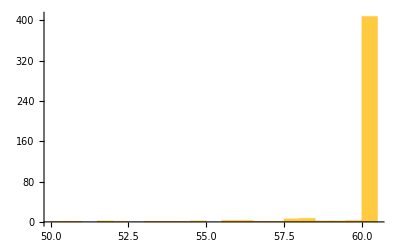

```mathematica
Histogram[fullgenomeSNPEFF[[All,133]]]
```

Many of the ones with lower mapping quality are the ones with missing genotype calls (filtered out below):

```mathematica
Select[fullgenomeSNPEFF[[All,{1,3,8,133}]],#[[4]]<60&]//MatrixForm
```

(chrI | 25487 | FLO9 | 58.61
chrI | 25489 | FLO9 | 57.62
chrI | 27090 | FLO9 | 52.4
chrI | 204218 | FLO1 | 56.97
chrI | 206360 | FLO1 | 54.5
chrI | 206363 | FLO1 | 54.41
chrI | 206375 | FLO1 | 53.78
chrV | 22913 | HXT13 | 51.91
chrVIII | 93335 | YHL008C | 58.24
chrVIII | 93350 | YHL008C | 58.24
chrVIII | 93359 | YHL008C | 58.13
chrVIII | 93361 | YHL008C | 58.11
chrVIII | 93370 | YHL008C | 58.16
chrVIII | 93375 | YHL008C | 58.16
chrVIII | 93391 | YHL008C | 58.28
chrVIII | 93577 | YHL008C | 51.63
chrVIII | 93608 | YHL008C | 54.81
chrVIII | 93624 | YHL008C | 56.2
chrVIII | 93898 | YHL008C | 50.58
chrX | 715087 | DAN4 | 58.93
chrX | 715108 | DAN4 | 57.88
chrX | 715114 | DAN4 | 57.14
chrX | 715117 | DAN4 | 59.04
chrX | 715141 | DAN4 | 55.81
chrX | 715149 | DAN4 | 59.1
chrXI | 144880 | PIR3 | 55.87
chrXI | 144883 | PIR3 | 56.03
chrXI | 578481 | YKR073C | 53.08
chrXI | 578485 | YKR073C | 50.17
chrXI | 613636 | SRP40 | 59.9
chrXII | 5683 | YLL066W-B | 57.77
chrXII | 650822 | HAP1 | 59.76
chrXIII | 588588 | MSS11 | 59.85
chrXIII | 609388 | DDR48 | 57.68
chrXIII | 908159 | YMR317W | 57.88
chrXIII | 908168 | YMR317W | 57.87
chrXIII | 908215 | YMR317W | 56.28
chrXIII | 908221 | YMR317W | 55.95)

```mathematica
Union[%[[All,3]]]
```

{DAN4,DDR48,FLO1,FLO9,HAP1,HXT13,MSS11,PIR3,SRP40,YHL008C,YKR073C,YLL066W-B,YMR317W}

Mean mapping quality of all genes:

```mathematica
Mean[fullgenomeSNPEFF[[All,133]]]
```

59.7012

Mean mapping quality of the genes dropped below with ≥5 “.” calls:

```mathematica
{"BSC1","DAN4","FLO1","FLO9","HAP1","MSS11","PIR3","YHL008C","YKR073C"};
Select[fullgenomeSNPEFF,MemberQ[%,#[[8]]]&];
Mean[%[[All,133]]]
```

56.6091

Of the genes filtered out because of having 5 or more uncalled genotypes, all but BSC1 have MQ<60

Mean mapping quality of the genes not dropped, but having some “.” calls:

```mathematica
{"SRP40","YGR130C","YLL066W-B","YLR296W","YMR317W"};
Select[fullgenomeSNPEFF,MemberQ[%,#[[8]]]&];
Mean[%[[All,133]]]
```

58.8042

Of the genes not filtered out (but of concern), three have MQ<60 {SRP40,YLL066W-B,YMR317W}.

### Dropping genes with too many uncalled genotypes and dropping genotypic calls with <5 depth

#### Processing and dropping genes with two many poor quality genotypes

Sites that were hard to call (low depth or no genotype call) can indicate duplicated genes and alignment problems.  Here we identify these:

```mathematica
droppos=-1+Position[header,"OLY077_S101"][[1,1]];(*# columns to be dropped before first sample*)
```

```mathematica
topos=Position[header,"ZnBM47_S95"][[1,1]];(*# last sample column*)
```

Extracting the ref vs alt call in genomeSNPEFF:

```mathematica
genomeSNPEFF=Table[".",{i,1,Length[fullgenomeSNPEFF]},{j,1,topos-droppos}];
```

```mathematica
genomeSNPEFF[[1]]//Length
```

110

```mathematica
For[i=1,i≤Length[fullgenomeSNPEFF],i++,
For[j=1+droppos,j≤topos,j++,
temp=StringSplit[fullgenomeSNPEFF[[i,j]],{":"}];
genomeSNPEFF[[i,j-droppos]]=temp[[1]];
]
]
```

```mathematica
genomeSNPEFF//Length
```

446

```mathematica
Tally[Select[genomeSNPEFF[[1]],#≠"."&]]
```

{{0,101},{1,9}}

All mutant sites and the tally of mutations in them:

```mathematica
summarytable=Table[{fullgenomeSNPEFF[[i,1]],fullgenomeSNPEFF[[i,3]],fullgenomeSNPEFF[[i,8]],fullgenomeSNPEFF[[i,9]],Sort[Tally[genomeSNPEFF[[i]]]]},{i,1,Length[genomeSNPEFF]}];
```

The set of sites where the number of “.” calls was ≥5:

```mathematica
dropthese=Select[summarytable,(#[[5,1,1]]==".")&&(#[[5,1,2]]≥5)&];
dropthese//MatrixForm
```

(chrI | 27090 | FLO9 | LOW | {{.,83},{0,2},{1,25}}
chrI | 204218 | FLO1 | MODERATE | {{.,71},{0,19},{1,20}}
chrI | 206360 | FLO1 | LOW | {{.,80},{0,16},{1,14}}
chrI | 206363 | FLO1 | LOW | {{.,70},{0,26},{1,14}}
chrI | 206375 | FLO1 | LOW | {{.,95},{0,1},{1,14}}
chrIV | 384924 | BSC1 | HIGH | {{.,99},{0,7},{1,4}}
chrVIII | 93335 | YHL008C | LOW | {{.,41},{0,1},{1,68}}
chrVIII | 93350 | YHL008C | LOW | {{.,39},{0,3},{1,68}}
chrVIII | 93359 | YHL008C | MODERATE | {{.,29},{0,15},{1,66}}
chrVIII | 93375 | YHL008C | HIGH | {{.,30},{0,44},{1,36}}
chrVIII | 93391 | YHL008C | MODERATE | {{.,65},{0,9},{1,36}}
chrX | 715087 | DAN4 | LOW | {{.,6},{0,97},{1,7}}
chrX | 715108 | DAN4 | LOW | {{.,65},{0,2},{1,43}}
chrX | 715114 | DAN4 | LOW | {{.,68},{0,5},{1,37}}
chrX | 715141 | DAN4 | LOW | {{.,61},{0,27},{1,22}}
chrXI | 144880 | PIR3 | LOW | {{.,76},{0,5},{1,29}}
chrXI | 144883 | PIR3 | LOW | {{.,52},{0,29},{1,29}}
chrXI | 578481 | YKR073C | HIGH | {{.,32},{0,77},{1,1}}
chrXII | 650822 | HAP1 | HIGH | {{.,90},{0,14},{1,6}}
chrXII | 650830 | HAP1 | LOW | {{.,98},{0,1},{1,11}}
chrXIII | 588588 | MSS11 | MODERATE | {{.,8},{0,25},{1,77}})

```mathematica
dropme=Union[dropthese[[All,3]]]
%//Length
```

{BSC1,DAN4,FLO1,FLO9,HAP1,MSS11,PIR3,YHL008C,YKR073C}

9

Depth of coverage for these genes is much higher on average, with both the high outliers (FLO1) and the two low outliers (BSC1 and HAP1):

```mathematica
Select[fullgenomeSNPEFF,MemberQ[dropme,#[[8]]]&][[All,{8,129}]]
Mean[%[[All,2]]]//N
```

{{FLO9,1799},{FLO9,1584},{FLO9,2213},{FLO1,348},{FLO1,15599},{FLO1,15734},{FLO1,17792},{BSC1,91},{YHL008C,2060},{YHL008C,2102},{YHL008C,2001},{YHL008C,1983},{YHL008C,1921},{YHL008C,1941},{YHL008C,2062},{YHL008C,1441},{YHL008C,1946},{YHL008C,1810},{YHL008C,2247},{DAN4,905},{DAN4,1522},{DAN4,1559},{DAN4,1583},{DAN4,1310},{DAN4,628},{PIR3,2648},{PIR3,2800},{YKR073C,1609},{YKR073C,1536},{HAP1,509},{HAP1,84},{MSS11,658}}

2938.28

Mapping quality is also poorer on average, except for BSC1, with the mean at the bottom 3.5% tail:

```mathematica
Select[fullgenomeSNPEFF,MemberQ[dropme,#[[8]]]&][[All,{8,133}]]
Mean[%[[All,2]]]//N
Length[Select[fullgenomeSNPEFF[[All,133]],#<%&]]/Length[fullgenomeSNPEFF[[All,133]]]//N//PercentForm
```

{{FLO9,58.61},{FLO9,57.62},{FLO9,52.4},{FLO1,56.97},{FLO1,54.5},{FLO1,54.41},{FLO1,53.78},{BSC1,60.},{YHL008C,58.24},{YHL008C,58.24},{YHL008C,58.13},{YHL008C,58.11},{YHL008C,58.16},{YHL008C,58.16},{YHL008C,58.28},{YHL008C,51.63},{YHL008C,54.81},{YHL008C,56.2},{YHL008C,50.58},{DAN4,58.93},{DAN4,57.88},{DAN4,57.14},{DAN4,59.04},{DAN4,55.81},{DAN4,59.1},{PIR3,55.87},{PIR3,56.03},{YKR073C,53.08},{YKR073C,50.17},{HAP1,59.76},{HAP1,60.},{MSS11,59.85}}

56.6091

3.587%

Dropping all sites (32) in the nine genes with ≥5 “.” calls:

```mathematica
Length[fullgenomeSNPEFF];
fullgenomeSNPEFF=Select[fullgenomeSNPEFF,MemberQ[dropme,#[[8]]]==False&];
%%-Length[fullgenomeSNPEFF]
```

32

Considering the others with uncalled genotypes, first recalculating the summary table:

```mathematica
genomeSNPEFF=Table[".",{i,1,Length[fullgenomeSNPEFF]},{j,1,topos-droppos}];For[i=1,i≤Length[fullgenomeSNPEFF],i++,
For[j=1+droppos,j≤topos,j++,
temp=StringSplit[fullgenomeSNPEFF[[i,j]],{":"}];
genomeSNPEFF[[i,j-droppos]]=temp[[1]];
]
]
summarytable=Table[{fullgenomeSNPEFF[[i,1]],fullgenomeSNPEFF[[i,3]],fullgenomeSNPEFF[[i,8]],fullgenomeSNPEFF[[i,9]],Sort[Tally[genomeSNPEFF[[i]]]]},{i,1,Length[genomeSNPEFF]}];
```

```mathematica
consider=Select[summarytable,(#[[5,1,1]]==".")&&(#[[5,1,2]]<5)&&(#[[5,1,2]]≥1)&];
consider//MatrixForm
```

(chrVII | 753296 | YGR130C | MODERATE | {{.,1},{0,23},{1,86}}
chrXI | 613636 | SRP40 | MODERATE | {{.,1},{0,1},{1,108}}
chrXII | 5683 | YLL066W-B | HIGH | {{.,3},{0,99},{1,8}}
chrXII | 723168 | YLR296W | HIGH | {{.,2},{0,104},{1,4}}
chrXIII | 908215 | YMR317W | LOW | {{.,1},{0,17},{1,92}}
chrXIII | 908221 | YMR317W | LOW | {{.,2},{0,9},{1,99}})

```mathematica
considergenes=Union[consider[[All,3]]]
%//Length
```

{SRP40,YGR130C,YLL066W-B,YLR296W,YMR317W}

5

Depth of coverage for these genes is somewhat higher on average:

```mathematica
Select[fullgenomeSNPEFF,MemberQ[considergenes,#[[8]]]&][[All,{8,129}]]
Mean[%[[All,2]]]//N
```

{{YGR130C,2020},{YGR130C,2020},{YGR130C,1799},{YGR130C,1809},{SRP40,1173},{YLL066W-B,607},{YLR296W,974},{YLR296W,977},{YMR317W,1959},{YMR317W,1960},{YMR317W,1836},{YMR317W,1789}}

1576.92

Mapping quality is slightly smaller (in the bottom 1.7% tail):

```mathematica
Select[fullgenomeSNPEFF,MemberQ[considergenes,#[[8]]]&][[All,{8,133}]]
Mean[%[[All,2]]]//N
Length[Select[fullgenomeSNPEFF[[All,133]],#<%&]]/Length[fullgenomeSNPEFF[[All,133]]]//N//PercentForm
```

{{YGR130C,60.},{YGR130C,60.},{YGR130C,60.},{YGR130C,60.},{SRP40,59.9},{YLL066W-B,57.77},{YLR296W,60.},{YLR296W,60.},{YMR317W,57.88},{YMR317W,57.87},{YMR317W,56.28},{YMR317W,55.95}}

58.8042

1.691%

These genes are kept but will be flagged as:
	{SRP40,YLL066W-B,YMR317W} have MQ<60
	{YGR130C,YMR317W} have depth ~ twice average depth (~1000)

#### Processing and dropping sites with <5 depth

We next scan for sites that are called with depth <5 (note that we do not filter on the depth for each allele, just total depth at that site in that sample).

An example of a site with low coverage:

```mathematica
Position[fullgenomeSNPEFF[[All,3]],723168][[1,1]];
fullgenomeSNPEFF[[%,106;;110]]
```

{1:0,1:1:26:26,0,0:10,0:10:99:0,249,0:3,3:6:3:0,3,0:8,0:8:99:0,252,0:4,0:4:99:0,108}

```mathematica
For[i=1;altered={},i≤Length[fullgenomeSNPEFF],i++,
For[j=1+droppos,j≤topos,j++,
temp=StringSplit[fullgenomeSNPEFF[[i,j]],{":"}];
If[ToExpression[temp[[3]]]<5,temp[[1]]=".";fullgenomeSNPEFF[[i,j]]=StringRiffle[temp,":"];AppendTo[altered,{i,j}]];
]
]
```

```mathematica
altered
```

The example is now corrected:

```mathematica
Position[fullgenomeSNPEFF[[All,3]],723168][[1,1]];
fullgenomeSNPEFF[[%,106;;110]]
```

{.:0,1:1:26:26,0,0:10,0:10:99:0,249,0:3,3:6:3:0,3,0:8,0:8:99:0,252,.:4,0:4:99:0,108}

Extracting the ref vs alt call in genomeSNPEFF:

```mathematica
genomeSNPEFF=Table[".",{i,1,Length[fullgenomeSNPEFF]},{j,1,topos-droppos}];
```

```mathematica
genomeSNPEFF[[1]]//Length
```

110

```mathematica
For[i=1,i≤Length[fullgenomeSNPEFF],i++,
For[j=1+droppos,j≤topos,j++,
temp=StringSplit[fullgenomeSNPEFF[[i,j]],{":"}];
genomeSNPEFF[[i,j-droppos]]=temp[[1]];
]
]
```

```mathematica
genomeSNPEFF//Length
```

414

```mathematica
Tally[Select[genomeSNPEFF[[1]],#≠"."&]]
```

{{0,104},{1,1}}

All mutant sites and the tally of mutations in them (ignore the error, which comes from sorting so that “.” is last):

```mathematica
summarytable=Table[{fullgenomeSNPEFF[[i,1]],fullgenomeSNPEFF[[i,3]],fullgenomeSNPEFF[[i,8]],fullgenomeSNPEFF[[i,9]],SortBy[Tally[genomeSNPEFF[[i]]],ToExpression[#]&]},{i,1,Length[genomeSNPEFF]}];
```

ToExpression::sntx: Invalid syntax in or before ". ".
                                                  ^

General::stop: Further output of ToExpression::sntx will be suppressed during this calculation.

This does not change the number of genes with mutations detected (i.e., all tallies with only two elements include the ref and alt allele):

```mathematica
Select[summarytable,Length[#[[5]]]≤2&]//MatrixForm
```

(chrII | 634214 | KTR3 | HIGH | {{0,108},{1,2}}
chrII | 682726 | SWC5 | MODERATE | {{0,109},{1,1}}
chrII | 683908 | PBP2 | MODERATE | {{0,109},{1,1}}
chrXI | 415085 | URB1 | MODERATE | {{0,109},{1,1}}
chrXI | 529178 | TRK2 | MODERATE | {{0,109},{1,1}}
chrXII | 672772 | RED1 | LOW | {{0,109},{1,1}}
chrXIII | 53046 | ZDS2 | LOW | {{0,109},{1,1}}
chrXIII | 533259 | RRB1 | LOW | {{0,109},{1,1}}
chrXIII | 547166 | RIM11 | MODERATE | {{0,109},{1,1}}
chrXIII | 585173 | INP2 | HIGH | {{0,109},{1,1}}
chrXIII | 914235 | FET4 | HIGH | {{0,109},{1,1}}
chrXIV | 195289 | ATG2 | LOW | {{0,109},{1,1}})

#### Revised gene list

```mathematica
genelist=Sort[Union[fullgenomeSNPEFF[[All,8]]]]
Length[%]
```

{ABP1,ACB1,ACC1,ADE6,ADR1,AFT1,AGP1,AHK1,ALD5,ALY2,APC2,ARO3,ASN1,ATG11,ATG2,ATG39,BDS1,BIR1,BLM10,BNA6,BNI1,BNI4,BRR2,BSD2,BUL1,BUL2,CAJ1,CCC2,CCR4,CCW12,CDC25,CIC1,CLB3,CLN3,CNE1,COG1,COG3,COI1,COQ1,CPA1,CSM3,CUE3,CWC22,CWH41,CYK3,DAL2,DBF20,DBP10,DDR48,DNF1,DOA4,DOT6,DSC2,DSE4,DUS4,EBS1,ECM14,ECM22,EFR3,ELO3,ERB1,ERG1,ERG27,ERG7,ERG9,FAS2,FAU1,FCY2,FET4,FIG2,FIG4,FLC2,FMP52,FRE6,FSF1,FYV10,FYV6,FZF1,GAS4,GAT1,GCD2,GID12,GPB1,GPB2,GPH1,GSC2,HBT1,HEH2,HHF2,HIS4,HMF1,HO,HOB2,HRT3,HSL1,HSP104,HUL5,HXT13,IDP1,IES3,ILV2,IMA1,INP2,IOC4,IPI3,IRC20,IRC8,IST2,ISU1,ITC1,KAR3,KGD1,KIN1,KIN82,KRE5,KSP1,KTR3,LAM1,LAM6,LOS1,LRG1,MAM3,MAS2,MCK1,MCM5,MCT1,MDH2,MDL2,MDM30,MET10,MET30,MEX67,MHP1,MKT1,MLF3,MLH3,MLS1,MMS4,MNN9,MOT1,MPA43,MRL1,MRPL36,MSC6,MSS2,MTR4,MYG1,MYO2,NAM8,NAR1,NFT1,NGG1,NIP100,NPL3,NSR1,NUC1,NUG1,OAF1,OCA4,OCA5,OPI1,OSH2,PBP2,PBS2,PCL5,PDA1,PDR1,PDR10,PDX1,PET111,PET127,PEX2,PFK26,PHM7,PHO23,PHO81,PHO84,PIB1,PKP1,PLB2,PMA1,POL3,PPQ1,PRC1,PRI1,PRI2,PRP2,PRP8,PTK2,PYK2,QRI7,RAD16,RAD17,RAD26,RBK1,RCE1,RCK2,RCO1,REC102,RED1,RHO1,RIM11,RIM21,RKM3,RMP1,RNY1,ROG1,RPA135,RPI1,RPL22A,RPL2A,RPL39,RPS15,RPS2,RPT5,RRB1,RRG7,RRP46,RRP6,RSC1,RSE1,RTC2,SAK1,SAP4,SBE2,SEC8,SET2,SFP1,SHP1,SIW14,SKN1,SMC2,SMY2,SNF7,SNT2,SPC105,SPO77,SPS100,SRP40,SSE1,SSK2,SSQ1,SSZ1,STE5,STP3,STT3,SUB2,SUC2,SUM1,SWC5,SWS2,SWT1,SYF2,SYG1,TAF8,TAH11,TAO3,TCO89,TFB1,TFG1,TIM54,TOM1,TOP1,TOP2,TOS3,TPS3,TRK2,TRL1,TUS1,UBC1,UBP5,UBR2,UBX7,UGA3,UGA4,UIP5,ULS1,UME6,URA2,URB1,USA1,UTP21,UTP8,VBA1,VCX1,VHR2,VID22,VPS13,VPS74,VRP1,VTC1,VTC3,VTC4,VTC5,WAR1,YAP6,YBR242W,YBR292C,YCF1,YCK1,YCT1,YDL199C,YDR003W-A,YDR157W,YDR541C,YEF1,YGR126W,YGR130C,YGR266W,YHC1,YHC3,YIH1,YIL092W,YLL066W-B,YLR108C,YLR296W,YML119W,YMR027W,YMR317W,YOR029W,YOR1,YOR296W,YOR343C,YPK1,YPL113C,YPR078C,YPR089W,YPT6,YRA1,YRB2,ZDS2,ZRT1,ZRT3}

333

The systematic names:

```mathematica
genelistSYS=Sort[Union[fullgenomeSNPEFF[[All,11]]]]
Length[%]
```

{YAL021C,YAL040C,YAL051W,YAL053W,YAL056W,YAL058W,YBL058W,YBR003W,YBR030W,YBR086C,YBR098W,YBR114W,YBR122C,YBR147W,YBR172C,YBR205W,YBR231C,YBR233W,YBR242W,YBR273C,YBR290W,YBR292C,YCL025C,YCL030C,YCR036W,YCR059C,YCR088W,YCR089W,YCR091W,YCR095C,YDL019C,YDL031W,YDL066W,YDL073W,YDL084W,YDL102W,YDL104C,YDL107W,YDL117W,YDL128W,YDL155W,YDL170W,YDL176W,YDL199C,YDL210W,YDL223C,YDL227C,YDL240W,YDR003W-A,YDR035W,YDR069C,YDR089W,YDR103W,YDR122W,YDR135C,YDR157W,YDR176W,YDR177W,YDR206W,YDR207C,YDR216W,YDR259C,YDR270W,YDR310C,YDR311W,YDR313C,YDR351W,YDR372C,YDR381C-A,YDR381W,YDR432W,YDR457W,YDR458C,YDR541C,YEL041W,YEL069C,YER004W,YER006W,YER048C,YER056C,YER057C,YER064C,YER072W,YER073W,YER088C,YER129W,YER144C,YER156C,YER157W,YER166W,YER172C,YER178W,YER183C,YFL007W,YFL021W,YFR030W,YFR031C,YFR031C-A,YFR047C,YGL008C,YGL013C,YGL022W,YGL027C,YGL071W,YGL093W,YGL110C,YGL123W,YGL131C,YGL133W,YGL141W,YGL144C,YGL179C,YGL223C,YGL229C,YGL254W,YGL255W,YGR032W,YGR037C,YGR056W,YGR061C,YGR083C,YGR095C,YGR126W,YGR128C,YGR129W,YGR130C,YGR143W,YGR159C,YGR175C,YGR186W,YGR193C,YGR233C,YGR266W,YGR278W,YGR281W,YGR287C,YHL020C,YHL029C,YHR024C,YHR052W,YHR064C,YHR071W,YHR072W,YHR082C,YHR086W,YHR132C,YHR135C,YHR139C,YHR155W,YHR165C,YHR190W,YIL042C,YIL046W,YIL047C,YIL063C,YIL092W,YIL097W,YIL107C,YIL119C,YIL125W,YIL129C,YIL162W,YIR008C,YIR029W,YJL012C,YJL042W,YJL050W,YJL051W,YJL054W,YJL059W,YJL084C,YJL087C,YJL128C,YJL130C,YJL168C,YJL189W,YJL208C,YJL210W,YJR035W,YJR046W,YJR059W,YJR089W,YKL014C,YKL045W,YKL101W,YKL126W,YKL175W,YKL205W,YKR044W,YKR050W,YKR092C,YKR103W,YLL026W,YLL040C,YLL051C,YLL055W,YLL066W-B,YLR024C,YLR025W,YLR052W,YLR061W,YLR072W,YLR097C,YLR100W,YLR108C,YLR110C,YLR127C,YLR145W,YLR228C,YLR247C,YLR248W,YLR261C,YLR263W,YLR274W,YLR296W,YLR298C,YLR310C,YLR312C,YLR329W,YLR337C,YLR341W,YLR368W,YLR369W,YLR372W,YLR373C,YLR375W,YLR403W,YLR405W,YLR409C,YLR425W,YML029W,YML049C,YML076C,YML109W,YML111W,YML114C,YML119W,YML123C,YMR006C,YMR027W,YMR044W,YMR048W,YMR049C,YMR075W,YMR088C,YMR108W,YMR131C,YMR139W,YMR163C,YMR173W,YMR212C,YMR257C,YMR261C,YMR274C,YMR275C,YMR297W,YMR317W,YMR319C,YNL030W,YNL032W,YNL074C,YNL081C,YNL085W,YNL088W,YNL097C,YNL117W,YNL133C,YNL182C,YNL233W,YNL240C,YNL242W,YNL249C,YNL271C,YNL294C,YNL307C,YNL325C,YNR011C,YNR016C,YNR031C,YNR067C,YOL006C,YOL040C,YOL060C,YOL073C,YOL084W,YOL126C,YOL132W,YOL164W,YOR001W,YOR017W,YOR029W,YOR117W,YOR166C,YOR191W,YOR221C,YOR271C,YOR296W,YOR303W,YOR305W,YOR326W,YOR328W,YOR336W,YOR343C,YOR347C,YOR354C,YOR368W,YOR371C,YPL019C,YPL050C,YPL082C,YPL106C,YPL113C,YPL123C,YPL135W,YPL164C,YPL169C,YPL174C,YPL179W,YPL180W,YPL231W,YPL270W,YPR010C,YPR049C,YPR055W,YPR078C,YPR079W,YPR089W,YPR111W,YPR117W,YPR141C,YPR145W,YPR160W,YPR165W}

333

Plotting the depth of coverage at that site:

```mathematica
Mean[fullgenomeSNPEFF[[All,129]]]//N
```

933.978

```mathematica
Max[fullgenomeSNPEFF[[All,129]]]
```

2469

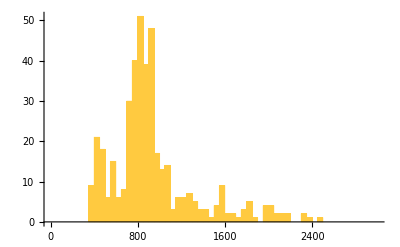

```mathematica
Histogram[fullgenomeSNPEFF[[All,129]],{50},PlotRange->{{0,3000},Automatic}]
```

#### Relating mutations to phenotypes (metal resistance, phosphorous metabolism, DNA repair)

Metal Resistance: 
The list of genes affecting metal resistance was downloaded from SGD (https://yeastgenome.org/observable/APO:0000090) on 23 May 2025:

```mathematica
metallist=Import["/Users/otto/Documents/Students/AnnaBazzicalupo/MetalAdaptation/Genomics/metal_resistance_annotations_23May2025.txt","tsv"];
```

```mathematica
metalhead=metallist[[2]]
```

{Gene,Gene Systematic Name,Phenotype,Experiment Type,Experiment Type Category,Mutant Information,Strain Background,Chemical,Details,Reference}

```mathematica
metallist=Drop[metallist,2];
```

Here we will use the Gene Systematic Name for comparison:

```mathematica
metalgenenames=Union[metallist[[All,2]]];
Length[%]
```

1791

Of the 333 genes bearing mutations, 121 (36.34%) are annotated as having metal tolerance:

```mathematica
Intersection[genelistSYS,metalgenenames]
{Length[genelistSYS],Length[%],Length[%]/Length[genelistSYS]//N//PercentForm}
```

{YAL021C,YAL040C,YAL051W,YAL053W,YAL056W,YBL058W,YBR098W,YBR114W,YBR122C,YBR172C,YBR231C,YBR233W,YBR273C,YBR290W,YCL030C,YCR036W,YCR088W,YDL066W,YDL073W,YDL128W,YDL155W,YDL176W,YDR069C,YDR089W,YDR103W,YDR122W,YDR135C,YDR176W,YDR207C,YDR216W,YDR270W,YDR310C,YDR351W,YDR372C,YDR432W,YDR457W,YDR458C,YER072W,YER129W,YER156C,YER178W,YFL007W,YGL027C,YGL071W,YGL141W,YGL223C,YGL254W,YGL255W,YGR037C,YGR056W,YHR064C,YHR082C,YHR086W,YHR135C,YIL047C,YIL097W,YIL125W,YJL012C,YJL042W,YJL128C,YJL189W,YJL208C,YJR059W,YKL101W,YKL126W,YKL175W,YKR050W,YKR092C,YLL040C,YLL051C,YLR024C,YLR025W,YLR061W,YLR072W,YLR228C,YLR248W,YLR261C,YLR337C,YLR341W,YLR368W,YLR369W,YLR372W,YLR373C,YLR375W,YLR403W,YLR425W,YML111W,YML123C,YMR075W,YMR108W,YMR139W,YMR173W,YMR261C,YMR275C,YMR319C,YNL032W,YNL074C,YNL097C,YNL233W,YNL242W,YNL271C,YNL294C,YNL307C,YNL325C,YNR031C,YOL006C,YOL060C,YOR221C,YOR296W,YOR326W,YOR347C,YPL019C,YPL050C,YPL106C,YPL123C,YPL135W,YPL179W,YPL180W,YPR049C,YPR141C,YPR160W}

{333,121,36.34%}

Appending “metal gene resistance” phenotype information to the data:

```mathematica
For[i=1;newcolumn={},i≤Length[fullgenomeSNPEFF],i++,
nameSYS=fullgenomeSNPEFF[[i,11]];
If[MemberQ[metalgenenames,nameSYS],AppendTo[newcolumn,"Metal"],AppendTo[newcolumn,"No"]]
]
```

```mathematica
fullgenomeSNPEFF=Transpose[Append[Transpose[fullgenomeSNPEFF],newcolumn]];
```

Phosphorus metabolic process: 
The list of genes affecting phosphorous metabolism was downloaded from Amigo 2 (https://amigo.geneontology.org/amigo/term/GO:0006793) on 17 June2025:

```mathematica
pholist=Import["/Users/otto/Documents/Students/AnnaBazzicalupo/MetalAdaptation/Genomics/phosphate_metabolism_annotations_17Jun2025.tsv","tsv"];
```

```mathematica
phohead=pholist[[1]]
```

{gene,gene_id,gene_name,go_id,evidence}

```mathematica
pholist=Drop[pholist,1];
```

The gene name but not the systematic name is listed:

```mathematica
phogenenames=pholist[[All,1]];
Length[%]
```

480

Of the 333 genes bearing mutations, 27 (8.1%) are annotated as affecting phosphorous metabolism:

```mathematica
Intersection[genelist,phogenenames]
{Length[genelist],Length[%],Length[%]/Length[genelist]//N//PercentForm}
```

{ACC1,ADE6,AFT1,BNA6,ERG9,FIG4,IDP1,KRE5,MPA43,OPI1,PDA1,PDX1,PFK26,PHO81,PHO84,PLB2,PYK2,RBK1,SIW14,URA2,VTC1,VTC3,VTC4,VTC5,YBR242W,YEF1,YPK1}

{333,27,8.108%}

Appending phosphorous metabolism phenotype information to the data:

```mathematica
For[i=1;newcolumn={},i≤Length[fullgenomeSNPEFF],i++,
name=fullgenomeSNPEFF[[i,8]];
If[MemberQ[phogenenames,name],AppendTo[newcolumn,"PHO"],AppendTo[newcolumn,"No"]]
]
```

```mathematica
fullgenomeSNPEFF=Transpose[Append[Transpose[fullgenomeSNPEFF],newcolumn]];
```

DNA Repair: 
The list of genes affecting DNA repair was downloaded from Amigo 2 (https://amigo.geneontology.org/amigo/term/GO:0006281) on 17 June 2025:

```mathematica
repairlist=Import["/Users/otto/Documents/Students/AnnaBazzicalupo/MetalAdaptation/Genomics/dna_repair_amigo_17Jun2025.tsv","tsv"];
```

```mathematica
repairhead=repairlist[[1]]
```

{gene,gene_id,gene_name,go_id,evidence}

```mathematica
repairlist=Drop[repairlist,1];
```

```mathematica
repairlist[[2]]
```

{RFC2,SGD:S000003829,Subunit of heteropentameric Replication factor C (RF-C),GO:0006298,TAS}

The gene name but not the systematic name is listed:

```mathematica
repairgenenames=Union[repairlist[[All,1]]];
Length[%]
```

322

Of the 333 genes bearing mutations, 23 (6.9%) are annotated as affecting DNA repair:

```mathematica
Intersection[genelist,repairgenenames]
{Length[genelist],Length[%],Length[%]/Length[genelist]//N//PercentForm}
```

{BLM10,CSM3,DDR48,FYV6,IRC20,MCK1,MCM5,MLH3,MMS4,PDR10,POL3,PRI2,RAD16,RAD17,RAD26,RSC1,SET2,SUB2,TAH11,TFB1,ULS1,VID22,YRA1}

{333,23,6.907%}

Appending DNA repair phenotype information to the data:

```mathematica
For[i=1;newcolumn={},i≤Length[fullgenomeSNPEFF],i++,
name=fullgenomeSNPEFF[[i,8]];
If[MemberQ[repairgenenames,name],AppendTo[newcolumn,"Repair"],AppendTo[newcolumn,"No"]]
]
```

```mathematica
fullgenomeSNPEFF=Transpose[Append[Transpose[fullgenomeSNPEFF],newcolumn]];
```

#### Exporting

For printing, we want a shorter header table:

```mathematica
newheader=Table[StringSplit[header[[i]],"_"][[1]],{i,1,Length[header]}];
newheader=Flatten[AppendTo[newheader,{"Metal resistance gene (SGD)","Phosphorous metabolism (Amigo 2)","DNA repair (SGD)"}]]
```

{CHROM,chr,POS,REF,ALT,QUAL,FORMAT,gene,effect,mut,gene,base,aa,ANN,OLY077,CdBM23,CdBM25,CdBM26,CdBM29,CdBM30,CdBM32,CdBM36,CdBM37,CdBM39,CdBM42,CdBM43,CdBM44,CdBM45,CdBM46,CdBM47,CdBM48,CoBM12,CoBM14,CoBM15,CoBM16,CoBM17,CoBM18,CoBM1,CoBM20,CoBM21,CoBM2,CoBM3,CoBM4,CoBM5,CoBM6,CoBM7,CoBM8,CuBM10,CuBM11,CuBM12,CuBM13,CuBM14,CuBM15,CuBM16,CuBM17,CuBM18,CuBM3,CuBM4,CuBM6,CuBM7,CuBM8,CuBM9,MnBM12,MnBM13,MnBM14,MnBM15,MnBM16,MnBM17,MnBM18,MnBM20,MnBM21,MnBM23,MnBM24,MnBM25,MnBM27,MnBM28,MnBM29,MnBM31,MnBM32,MnBM34,MnBM38,MnBM39,MnBM42,MnBM44,NiBM11,NiBM12,NiBM14,NiBM16,NiBM17,NiBM21,NiBM22,NiBM24,NiBM25,NiBM27,NiBM28,NiBM29,NiBM30,NiBM4,NiBM6,NiBM8,NiBM9,ZnBM11,ZnBM12,ZnBM15,ZnBM16,ZnBM17,ZnBM19,ZnBM22,ZnBM23,ZnBM25,ZnBM28,ZnBM29,ZnBM31,ZnBM34,ZnBM37,ZnBM38,ZnBM39,ZnBM41,ZnBM42,ZnBM43,ZnBM44,ZnBM45,ZnBM46,ZnBM47,AC,AF,AN,BaseQRankSum,DP,FS,MLEAC,MLEAF,MQ,MQRankSum,QD,ReadPosRankSum,SOR,LOF,Metal resistance gene (SGD),Phosphorous metabolism (Amigo 2),DNA repair (SGD)}

First recalculating the summary table:

```mathematica
genomeSNPEFF=Table[-1,{i,1,Length[fullgenomeSNPEFF]},{j,1,topos-droppos}];For[i=1,i≤Length[fullgenomeSNPEFF],i++,
For[j=1+droppos,j≤topos,j++,
temp=StringSplit[fullgenomeSNPEFF[[i,j]],{":"}];
temp2=temp[[1]];
genomeSNPEFF[[i,j-droppos]]=temp2;
]
]
```

The following sites are “1”s in OLY077 and so we swap 1’s for 0’s and call these revertants

```mathematica
Position[genomeSNPEFF,_?(#[[1]]=="1"&)][[All,1]]
```

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification 0⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{155,234,322,323,324,325}

Swapping 0<->1 and calling “.” 0 (like OLY077):

```mathematica
For[i=1,i≤Length[%],i++,
genomeSNPEFF[[%[[i]]]]=Mod[ToExpression[StringReplace[genomeSNPEFF[[%[[i]]]],"."->"1"]]+1,2]
]
```

Swapped variants positions:

```mathematica
fullgenomeSNPEFF[[%%,{1,3,8}]]
```

{{chrVII,753296,YGR130C},{chrXI,613636,SRP40},{chrXIII,908159,YMR317W},{chrXIII,908168,YMR317W},{chrXIII,908215,YMR317W},{chrXIII,908221,YMR317W}}

All remaining “.” are treated as identical to OLY077 (not mutant) and 0/1 treated as numbers (only in genomeSNPEFF, summarytable and fullgenomeSNPEFF remain the same):

```mathematica
genomeSNPEFF=genomeSNPEFF/."."->"0";
genomeSNPEFF=ToExpression/@genomeSNPEFF;
```

Number of unique mutations:

```mathematica
Length[genomeSNPEFF]
```

414

Number of mutational hits:

```mathematica
Total[Total[genomeSNPEFF]]
```

506

As expected (once revertants were recoded), OLY077 has no mutations

```mathematica
Total[genomeSNPEFF[[All,1]]]
```

0

Number of lines per unique mutation:

```mathematica
Sort[Tally[Sum[genomeSNPEFF[[All,i]],{i,1,110}]]]
```

{{1,384},{2,18},{3,3},{4,1},{5,1},{6,3},{8,1},{9,1},{10,1},{23,1}}

Genes with excessive SNP mutations (≥5) include:

```mathematica
toopoly=Position[genomeSNPEFF,_?(Total[#]≥5&)][[All,1]]
```

{68,155,159,236,322,323,324,325}

The genotype call for OLY077 at these sites:

```mathematica
fullgenomeSNPEFF[[toopoly,Position[newheader,"OLY077"][[1,1]]]]//MatrixForm
```

(.:3,0:3:99:0,100
1:0,21:21:99:945,0
0:8,0:8:99:0,175
0:13,0:13:99:0,226
1:0,10:10:99:450,0
1:0,10:10:99:450,0
1:0,9:9:99:406,0
1:0,9:9:99:406,0)

```mathematica
consider=summarytable[[toopoly]];
consider//MatrixForm
```

(chrIV | 815428 | NGG1 | MODERATE | {{0,38},{1,10},{.,62}}
chrVII | 753296 | YGR130C | MODERATE | {{0,23},{1,81},{.,6}}
chrVII | 869872 | TFG1 | MODERATE | {{0,73},{1,6},{.,31}}
chrXII | 5683 | YLL066W-B | HIGH | {{0,46},{1,8},{.,56}}
chrXIII | 908159 | YMR317W | HIGH | {{0,5},{1,80},{.,25}}
chrXIII | 908168 | YMR317W | HIGH | {{0,6},{1,63},{.,41}}
chrXIII | 908215 | YMR317W | LOW | {{0,9},{1,60},{.,41}}
chrXIII | 908221 | YMR317W | LOW | {{0,6},{1,68},{.,36}})

Depth of coverage for these genes is higher on average:

```mathematica
fullgenomeSNPEFF[[toopoly,{8,129}]]
Mean[%[[All,2]]]//N
```

{{NGG1,642},{YGR130C,1809},{TFG1,798},{YLL066W-B,607},{YMR317W,1959},{YMR317W,1960},{YMR317W,1836},{YMR317W,1789}}

1425.

Mapping quality is also poorer on average:

```mathematica
fullgenomeSNPEFF[[toopoly,{8,133}]]
Mean[%[[All,2]]]//N
Length[Select[fullgenomeSNPEFF[[All,133]],#<%&]]/Length[fullgenomeSNPEFF[[All,133]]]//N//PercentForm
```

{{NGG1,60.},{YGR130C,60.},{TFG1,60.},{YLL066W-B,57.77},{YMR317W,57.88},{YMR317W,57.87},{YMR317W,56.28},{YMR317W,55.95}}

58.2188

1.691%

```mathematica
considergenes=Union[consider[[All,3]]]
%//Length
```

{NGG1,TFG1,YGR130C,YLL066W-B,YMR317W}

5

```mathematica
Position[newheader,"Metal resistance gene (SGD)"][[1,1]]
```

139

```mathematica
toprintmultiple=Sort[Table[{fullgenomeSNPEFF[[toopoly[[i]],8]],fullgenomeSNPEFF[[toopoly[[i]],11]],StringJoin[fullgenomeSNPEFF[[toopoly[[i]],1]],".",ToString[fullgenomeSNPEFF[[toopoly[[i]],3]]]],fullgenomeSNPEFF[[toopoly[[i]],12]],fullgenomeSNPEFF[[toopoly[[i]],13]],fullgenomeSNPEFF[[toopoly[[i]],9]],fullgenomeSNPEFF[[toopoly[[i]],Position[newheader,"Metal resistance gene (SGD)"][[1,1]]]],fullgenomeSNPEFF[[toopoly[[i]],Position[newheader,"Phosphorous metabolism (Amigo 2)"][[1,1]]]],fullgenomeSNPEFF[[toopoly[[i]],Position[newheader,"DNA repair (SGD)"][[1,1]]]],summarytable[[toopoly[[i]],5]],genomeSNPEFF[[toopoly[[i]]]].newheader[[1+droppos;;topos]]},{i,1,Length[toopoly]}]];
MatrixForm[%]
```

(NGG1 | YDR176W | chrIV.815428 | c.977G>A | p.Ser326Asn | MODERATE | Metal | No | No | {{0,38},{1,10},{.,62}} | CuBM10+CuBM11+CuBM12+CuBM13+CuBM14+CuBM17+CuBM18+CuBM4+CuBM7+CuBM9
TFG1 | YGR186W | chrVII.869872 | c.2099T>C | p.Phe700Ser | MODERATE | No | No | No | {{0,73},{1,6},{.,31}} | CuBM11+CuBM14+CuBM17+CuBM18+CuBM7+CuBM9
YGR130C | YGR130C | chrVII.753296 | c.543_548delATCGTC | p.Ser182_Ser183del | MODERATE | No | No | No | {{0,23},{1,81},{.,6}} | CdBM23+CdBM36+CdBM39+CdBM43+CoBM12+CoBM15+CoBM16+CoBM17+CoBM20+CuBM12+CuBM9+MnBM17+MnBM21+MnBM25+MnBM29+NiBM12+NiBM14+NiBM22+NiBM8+NiBM9+ZnBM17+ZnBM22+ZnBM23
YLL066W-B | YLL066W-B | chrXII.5683 | c.85_103delCACACCCACACCCACACAC | p.His29fs | HIGH | No | No | No | {{0,46},{1,8},{.,56}} | CdBM42+MnBM20+MnBM23+NiBM21+ZnBM28+ZnBM34+ZnBM41+ZnBM44
YMR317W | YMR317W | chrXIII.908159 | c.797_804delCGGCAACG | p.Ser266fs | HIGH | No | No | No | {{0,5},{1,80},{.,25}} | CdBM36+CoBM14+CuBM6+MnBM17+MnBM24
YMR317W | YMR317W | chrXIII.908168 | c.806_833delCTAGCGTAATTAGTTCAGAAGCTTCATG | p.Ser269fs | HIGH | No | No | No | {{0,6},{1,63},{.,41}} | CdBM36+CoBM14+CuBM6+MnBM16+MnBM17+MnBM24
YMR317W | YMR317W | chrXIII.908215 | c.852G>A | p.Val284Val | LOW | No | No | No | {{0,9},{1,60},{.,41}} | CdBM32+CdBM36+CoBM14+CoBM7+CoBM8+CuBM10+CuBM6+MnBM16+MnBM17
YMR317W | YMR317W | chrXIII.908221 | c.858G>A | p.Ser286Ser | LOW | No | No | No | {{0,6},{1,68},{.,36}} | CdBM36+CoBM14+CuBM10+CuBM13+CuBM6+MnBM16)

```mathematica
Export["/Users/otto/Documents/Students/AnnaBazzicalupo/MetalAdaptation/Genomics/toopolymorphic_17June2025.tsv",Join[{{"Gene","Systematic name","chrom.pos","base_change","aa_change","effect","Metal resistance gene (SGD)","Phosphorous metabolism (Amigo 2)","DNA repair (SGD)","# lines","Lines carrying variant not seen in W303 ancestor (OLY077)"}},toprintmultiple]];
```

The remaining sites:

```mathematica
rest=Complement[Table[i,{i,1,Length[fullgenomeSNPEFF]}],toopoly];
```

```mathematica
Length[rest]+Length[toopoly]-Length[fullgenomeSNPEFF]
```

0

Including NGG1 and TFG1:

```mathematica
fullgenomeSNPEFF[[68,8]]
```

NGG1

```mathematica
fullgenomeSNPEFF[[159,8]]
```

TFG1

```mathematica
rest=Sort[Join[rest,{68,159}]];
```

```mathematica
toprint=Table[{fullgenomeSNPEFF[[rest[[i]],8]],fullgenomeSNPEFF[[rest[[i]],11]],StringJoin[fullgenomeSNPEFF[[rest[[i]],1]],".",ToString[fullgenomeSNPEFF[[rest[[i]],3]]]],fullgenomeSNPEFF[[rest[[i]],12]],fullgenomeSNPEFF[[rest[[i]],13]],fullgenomeSNPEFF[[rest[[i]],9]],
fullgenomeSNPEFF[[rest[[i]],Position[newheader,"Metal resistance gene (SGD)"][[1,1]]]],fullgenomeSNPEFF[[rest[[i]],Position[newheader,"Phosphorous metabolism (Amigo 2)"][[1,1]]]],fullgenomeSNPEFF[[rest[[i]],Position[newheader,"DNA repair (SGD)"][[1,1]]]],genomeSNPEFF[[rest[[i]]]].newheader[[1+droppos;;topos]]},{i,1,Length[rest]}];
MatrixForm[%[[1;;12]]] (*The first 12 lines shows the nature of parallel SNPs in different lines*)
```

(CNE1 | YAL058W | chrI.37834 | c.371C>T | p.Thr124Met | MODERATE | No | No | No | MnBM14
CNE1 | YAL058W | chrI.38041 | c.578C>T | p.Ser193Leu | MODERATE | No | No | No | MnBM14
GPB2 | YAL056W | chrI.40593 | c.1335A>C | p.Leu445Phe | MODERATE | Metal | No | No | CoBM17
FLC2 | YAL053W | chrI.48206 | c.2308A>G | p.Asn770Asp | MODERATE | Metal | No | No | MnBM14
OAF1 | YAL051W | chrI.48640 | c.77C>T | p.Ala26Val | MODERATE | Metal | No | No | MnBM14
CLN3 | YAL040C | chrI.66785 | c.736T>G | p.Leu246Val | MODERATE | Metal | No | No | CoBM3
CCR4 | YAL021C | chrI.112637 | c.723C>G | p.Asp241Glu | MODERATE | Metal | No | No | MnBM42
CCR4 | YAL021C | chrI.113278 | c.82C>T | p.Leu28Leu | LOW | Metal | No | No | MnBM42
SHP1 | YBL058W | chrII.112395 | c.959A>T | p.Glu320Val | MODERATE | Metal | No | No | CoBM6
COQ1 | YBR003W | chrII.243326 | c.518C>A | p.Pro173His | MODERATE | No | No | No | CuBM15
RKM3 | YBR030W | chrII.299270 | c.979G>C | p.Gly327Arg | MODERATE | No | No | No | CoBM4+NiBM24
IST2 | YBR086C | chrII.421076 | c.1966G>T | p.Ala656Ser | MODERATE | No | No | No | NiBM12)

```mathematica
Length[toprint]
```

408

For each SNP that occurs multiple times, make a separate row:

```mathematica
namepos=10; (*Line names*)
For[i=1;toappend={},i≤Length[toprint],i++,
splits=Length[toprint[[i,namepos]]];
If[splits>1,
temp=toprint[[i,namepos]];
toprint[[i,namepos]]=toprint[[i,namepos]][[1]];
For[j=2,j≤splits,j++,
toadd=toprint[[i]];
toadd[[namepos]]=temp[[j]];
toappend=Append[toappend,toadd]
]
]
]
```

Sorting then putting the metal first:

```mathematica
Sort[Join[toprint,toappend]];
mat=Transpose[Join[{Transpose[%[[All,namepos]]]},Transpose[%[[All,1;;namepos-1]]]]];
MatrixForm[mat[[1;;12]]]
```

(CuBM18 | ABP1 | YCR088W | chrIII.265691 | c.624A>C | p.Leu208Phe | MODERATE | Metal | No | No
MnBM42 | ACB1 | YGR037C | chrVII.559830 | c.165G>A | p.Lys55Lys | LOW | Metal | No | No
ZnBM12 | ACC1 | YNR016C | chrXIV.660428 | c.947G>T | p.Gly316Val | MODERATE | No | PHO | No
ZnBM15 | ACC1 | YNR016C | chrXIV.660428 | c.947G>T | p.Gly316Val | MODERATE | No | PHO | No
ZnBM23 | ADE6 | YGR061C | chrVII.613265 | c.2701G>C | p.Val901Leu | MODERATE | No | PHO | No
MnBM23 | ADR1 | YDR216W | chrIV.896208 | c.1174C>T | p.His392Tyr | MODERATE | Metal | No | No
CoBM17 | AFT1 | YGL071W | chrVII.372520 | c.509C>T | p.Ser170Phe | MODERATE | Metal | PHO | No
MnBM31 | AGP1 | YCL025C | chrIII.76154 | c.1765delA | p.Ile589fs | HIGH | No | No | No
MnBM31 | AGP1 | YCL025C | chrIII.76159 | c.1761G>T | p.Leu587Leu | LOW | No | No | No
CdBM25 | AHK1 | YDL073W | chrIV.329143 | c.2531G>A | p.Gly844Glu | MODERATE | Metal | No | No
MnBM18 | ALD5 | YER073W | chrV.304100 | c.71C>A | p.Ser24Tyr | MODERATE | No | No | No
CoBM16 | ALY2 | YJL084C | chrX.277922 | c.80delT | p.Leu27fs | HIGH | No | No | No)

The length matches that expected from the tally of multiply hit genes:

```mathematica
Length[mat]
```

449

```mathematica
Sort[Tally[Sum[genomeSNPEFF[[All,i]],{i,1,110}]]][[1;;4]]
%[[All,1]].%[[All,2]]+(6+10)(*Adding NGG1 and TFG1*)
```

{{1,384},{2,18},{3,3},{4,1}}

449

```mathematica
Export["/Users/otto/Documents/Students/AnnaBazzicalupo/MetalAdaptation/Genomics/SNPs_17June2025.tsv",Join[{{"Line","Gene","Systematic name","chrom.pos","base_change","aa_change","effect","Metal resistance gene (SGD)","Phosphorous metabolism (Amigo 2)","DNA repair (SGD)"}},mat]];
```

Tally by line:

```mathematica
newheader[[16;;124]]//Length
```

109

```mathematica
bymetal=Tally[Sort[Join[mat[[All,1]],newheader[[16;;124]]]]];
bymetal[[All,2]]=bymetal[[All,2]]-1;
bymetal
```

{{CdBM23,4},{CdBM25,2},{CdBM26,5},{CdBM29,5},{CdBM30,9},{CdBM32,7},{CdBM36,0},{CdBM37,4},{CdBM39,6},{CdBM42,3},{CdBM43,3},{CdBM44,3},{CdBM45,1},{CdBM46,3},{CdBM47,2},{CdBM48,1},{CoBM1,4},{CoBM12,6},{CoBM14,1},{CoBM15,8},{CoBM16,5},{CoBM17,6},{CoBM18,7},{CoBM2,6},{CoBM20,2},{CoBM21,5},{CoBM3,8},{CoBM4,4},{CoBM5,6},{CoBM6,8},{CoBM7,5},{CoBM8,5},{CuBM10,2},{CuBM11,2},{CuBM12,2},{CuBM13,2},{CuBM14,5},{CuBM15,1},{CuBM16,0},{CuBM17,3},{CuBM18,5},{CuBM3,1},{CuBM4,3},{CuBM6,2},{CuBM7,3},{CuBM8,0},{CuBM9,4},{MnBM12,5},{MnBM13,5},{MnBM14,36},{MnBM15,1},{MnBM16,5},{MnBM17,4},{MnBM18,3},{MnBM20,2},{MnBM21,1},{MnBM23,5},{MnBM24,4},{MnBM25,2},{MnBM27,3},{MnBM28,1},{MnBM29,3},{MnBM31,4},{MnBM32,13},{MnBM34,0},{MnBM38,5},{MnBM39,4},{MnBM42,102},{MnBM44,1},{NiBM11,2},{NiBM12,1},{NiBM14,0},{NiBM16,1},{NiBM17,1},{NiBM21,2},{NiBM22,0},{NiBM24,3},{NiBM25,0},{NiBM27,1},{NiBM28,2},{NiBM29,0},{NiBM30,2},{NiBM4,4},{NiBM6,4},{NiBM8,0},{NiBM9,1},{ZnBM11,2},{ZnBM12,1},{ZnBM15,2},{ZnBM16,4},{ZnBM17,2},{ZnBM19,2},{ZnBM22,1},{ZnBM23,2},{ZnBM25,0},{ZnBM28,1},{ZnBM29,1},{ZnBM31,1},{ZnBM34,0},{ZnBM37,1},{ZnBM38,2},{ZnBM39,1},{ZnBM41,2},{ZnBM42,1},{ZnBM43,3},{ZnBM44,2},{ZnBM45,3},{ZnBM46,2},{ZnBM47,1}}

```mathematica
Total[bymetal[[All,2]]]
```

449

```mathematica
Sort[Union[mat[[All,2]]]]
Length[%]
```

{ABP1,ACB1,ACC1,ADE6,ADR1,AFT1,AGP1,AHK1,ALD5,ALY2,APC2,ARO3,ASN1,ATG11,ATG2,ATG39,BDS1,BIR1,BLM10,BNA6,BNI1,BNI4,BRR2,BSD2,BUL1,BUL2,CAJ1,CCC2,CCR4,CCW12,CDC25,CIC1,CLB3,CLN3,CNE1,COG1,COG3,COI1,COQ1,CPA1,CSM3,CUE3,CWC22,CWH41,CYK3,DAL2,DBF20,DBP10,DDR48,DNF1,DOA4,DOT6,DSC2,DSE4,DUS4,EBS1,ECM14,ECM22,EFR3,ELO3,ERB1,ERG1,ERG27,ERG7,ERG9,FAS2,FAU1,FCY2,FET4,FIG2,FIG4,FLC2,FMP52,FRE6,FSF1,FYV10,FYV6,FZF1,GAS4,GAT1,GCD2,GID12,GPB1,GPB2,GPH1,GSC2,HBT1,HEH2,HHF2,HIS4,HMF1,HO,HOB2,HRT3,HSL1,HSP104,HUL5,HXT13,IDP1,IES3,ILV2,IMA1,INP2,IOC4,IPI3,IRC20,IRC8,IST2,ISU1,ITC1,KAR3,KGD1,KIN1,KIN82,KRE5,KSP1,KTR3,LAM1,LAM6,LOS1,LRG1,MAM3,MAS2,MCK1,MCM5,MCT1,MDH2,MDL2,MDM30,MET10,MET30,MEX67,MHP1,MKT1,MLF3,MLH3,MLS1,MMS4,MNN9,MOT1,MPA43,MRL1,MRPL36,MSC6,MSS2,MTR4,MYG1,MYO2,NAM8,NAR1,NFT1,NGG1,NIP100,NPL3,NSR1,NUC1,NUG1,OAF1,OCA4,OCA5,OPI1,OSH2,PBP2,PBS2,PCL5,PDA1,PDR1,PDR10,PDX1,PET111,PET127,PEX2,PFK26,PHM7,PHO23,PHO81,PHO84,PIB1,PKP1,PLB2,PMA1,POL3,PPQ1,PRC1,PRI1,PRI2,PRP2,PRP8,PTK2,PYK2,QRI7,RAD16,RAD17,RAD26,RBK1,RCE1,RCK2,RCO1,REC102,RED1,RHO1,RIM11,RIM21,RKM3,RMP1,RNY1,ROG1,RPA135,RPI1,RPL22A,RPL2A,RPL39,RPS15,RPS2,RPT5,RRB1,RRG7,RRP46,RRP6,RSC1,RSE1,RTC2,SAK1,SAP4,SBE2,SEC8,SET2,SFP1,SHP1,SIW14,SKN1,SMC2,SMY2,SNF7,SNT2,SPC105,SPO77,SPS100,SRP40,SSE1,SSK2,SSQ1,SSZ1,STE5,STP3,STT3,SUB2,SUC2,SUM1,SWC5,SWS2,SWT1,SYF2,SYG1,TAF8,TAH11,TAO3,TCO89,TFB1,TFG1,TIM54,TOM1,TOP1,TOP2,TOS3,TPS3,TRK2,TRL1,TUS1,UBC1,UBP5,UBR2,UBX7,UGA3,UGA4,UIP5,ULS1,UME6,URA2,URB1,USA1,UTP21,UTP8,VBA1,VCX1,VHR2,VID22,VPS13,VPS74,VRP1,VTC1,VTC3,VTC4,VTC5,WAR1,YAP6,YBR242W,YBR292C,YCF1,YCK1,YCT1,YDL199C,YDR003W-A,YDR157W,YDR541C,YEF1,YGR126W,YGR130C,YGR266W,YHC1,YHC3,YIH1,YIL092W,YLR108C,YLR296W,YML119W,YMR027W,YOR029W,YOR1,YOR296W,YOR343C,YPK1,YPL113C,YPR078C,YPR089W,YPT6,YRA1,YRB2,ZDS2,ZRT1,ZRT3}

331

Gene list with all lines:

```mathematica
Sort[Union[mat[[All,2]]]]
Length[%]
```

{ABP1,ACB1,ACC1,ADE6,ADR1,AFT1,AGP1,AHK1,ALD5,ALY2,APC2,ARO3,ASN1,ATG11,ATG2,ATG39,BDS1,BIR1,BLM10,BNA6,BNI1,BNI4,BRR2,BSD2,BUL1,BUL2,CAJ1,CCC2,CCR4,CCW12,CDC25,CIC1,CLB3,CLN3,CNE1,COG1,COG3,COI1,COQ1,CPA1,CSM3,CUE3,CWC22,CWH41,CYK3,DAL2,DBF20,DBP10,DDR48,DNF1,DOA4,DOT6,DSC2,DSE4,DUS4,EBS1,ECM14,ECM22,EFR3,ELO3,ERB1,ERG1,ERG27,ERG7,ERG9,FAS2,FAU1,FCY2,FET4,FIG2,FIG4,FLC2,FMP52,FRE6,FSF1,FYV10,FYV6,FZF1,GAS4,GAT1,GCD2,GID12,GPB1,GPB2,GPH1,GSC2,HBT1,HEH2,HHF2,HIS4,HMF1,HO,HOB2,HRT3,HSL1,HSP104,HUL5,HXT13,IDP1,IES3,ILV2,IMA1,INP2,IOC4,IPI3,IRC20,IRC8,IST2,ISU1,ITC1,KAR3,KGD1,KIN1,KIN82,KRE5,KSP1,KTR3,LAM1,LAM6,LOS1,LRG1,MAM3,MAS2,MCK1,MCM5,MCT1,MDH2,MDL2,MDM30,MET10,MET30,MEX67,MHP1,MKT1,MLF3,MLH3,MLS1,MMS4,MNN9,MOT1,MPA43,MRL1,MRPL36,MSC6,MSS2,MTR4,MYG1,MYO2,NAM8,NAR1,NFT1,NGG1,NIP100,NPL3,NSR1,NUC1,NUG1,OAF1,OCA4,OCA5,OPI1,OSH2,PBP2,PBS2,PCL5,PDA1,PDR1,PDR10,PDX1,PET111,PET127,PEX2,PFK26,PHM7,PHO23,PHO81,PHO84,PIB1,PKP1,PLB2,PMA1,POL3,PPQ1,PRC1,PRI1,PRI2,PRP2,PRP8,PTK2,PYK2,QRI7,RAD16,RAD17,RAD26,RBK1,RCE1,RCK2,RCO1,REC102,RED1,RHO1,RIM11,RIM21,RKM3,RMP1,RNY1,ROG1,RPA135,RPI1,RPL22A,RPL2A,RPL39,RPS15,RPS2,RPT5,RRB1,RRG7,RRP46,RRP6,RSC1,RSE1,RTC2,SAK1,SAP4,SBE2,SEC8,SET2,SFP1,SHP1,SIW14,SKN1,SMC2,SMY2,SNF7,SNT2,SPC105,SPO77,SPS100,SRP40,SSE1,SSK2,SSQ1,SSZ1,STE5,STP3,STT3,SUB2,SUC2,SUM1,SWC5,SWS2,SWT1,SYF2,SYG1,TAF8,TAH11,TAO3,TCO89,TFB1,TFG1,TIM54,TOM1,TOP1,TOP2,TOS3,TPS3,TRK2,TRL1,TUS1,UBC1,UBP5,UBR2,UBX7,UGA3,UGA4,UIP5,ULS1,UME6,URA2,URB1,USA1,UTP21,UTP8,VBA1,VCX1,VHR2,VID22,VPS13,VPS74,VRP1,VTC1,VTC3,VTC4,VTC5,WAR1,YAP6,YBR242W,YBR292C,YCF1,YCK1,YCT1,YDL199C,YDR003W-A,YDR157W,YDR541C,YEF1,YGR126W,YGR130C,YGR266W,YHC1,YHC3,YIH1,YIL092W,YLR108C,YLR296W,YML119W,YMR027W,YOR029W,YOR1,YOR296W,YOR343C,YPK1,YPL113C,YPR078C,YPR089W,YPT6,YRA1,YRB2,ZDS2,ZRT1,ZRT3}

331

```mathematica
Sort[Union[mat[[All,2]]]]
Length[%]
```

{ABP1,ACB1,ACC1,ADE6,ADR1,AFT1,AGP1,AHK1,ALD5,ALY2,APC2,ARO3,ASN1,ATG11,ATG2,ATG39,BDS1,BIR1,BLM10,BNA6,BNI1,BNI4,BRR2,BSD2,BUL1,BUL2,CAJ1,CCC2,CCR4,CCW12,CDC25,CIC1,CLB3,CLN3,CNE1,COG1,COG3,COI1,COQ1,CPA1,CSM3,CUE3,CWC22,CWH41,CYK3,DAL2,DBF20,DBP10,DDR48,DNF1,DOA4,DOT6,DSC2,DSE4,DUS4,EBS1,ECM14,ECM22,EFR3,ELO3,ERB1,ERG1,ERG27,ERG7,ERG9,FAS2,FAU1,FCY2,FET4,FIG2,FIG4,FLC2,FMP52,FRE6,FSF1,FYV10,FYV6,FZF1,GAS4,GAT1,GCD2,GID12,GPB1,GPB2,GPH1,GSC2,HBT1,HEH2,HHF2,HIS4,HMF1,HO,HOB2,HRT3,HSL1,HSP104,HUL5,HXT13,IDP1,IES3,ILV2,IMA1,INP2,IOC4,IPI3,IRC20,IRC8,IST2,ISU1,ITC1,KAR3,KGD1,KIN1,KIN82,KRE5,KSP1,KTR3,LAM1,LAM6,LOS1,LRG1,MAM3,MAS2,MCK1,MCM5,MCT1,MDH2,MDL2,MDM30,MET10,MET30,MEX67,MHP1,MKT1,MLF3,MLH3,MLS1,MMS4,MNN9,MOT1,MPA43,MRL1,MRPL36,MSC6,MSS2,MTR4,MYG1,MYO2,NAM8,NAR1,NFT1,NGG1,NIP100,NPL3,NSR1,NUC1,NUG1,OAF1,OCA4,OCA5,OPI1,OSH2,PBP2,PBS2,PCL5,PDA1,PDR1,PDR10,PDX1,PET111,PET127,PEX2,PFK26,PHM7,PHO23,PHO81,PHO84,PIB1,PKP1,PLB2,PMA1,POL3,PPQ1,PRC1,PRI1,PRI2,PRP2,PRP8,PTK2,PYK2,QRI7,RAD16,RAD17,RAD26,RBK1,RCE1,RCK2,RCO1,REC102,RED1,RHO1,RIM11,RIM21,RKM3,RMP1,RNY1,ROG1,RPA135,RPI1,RPL22A,RPL2A,RPL39,RPS15,RPS2,RPT5,RRB1,RRG7,RRP46,RRP6,RSC1,RSE1,RTC2,SAK1,SAP4,SBE2,SEC8,SET2,SFP1,SHP1,SIW14,SKN1,SMC2,SMY2,SNF7,SNT2,SPC105,SPO77,SPS100,SRP40,SSE1,SSK2,SSQ1,SSZ1,STE5,STP3,STT3,SUB2,SUC2,SUM1,SWC5,SWS2,SWT1,SYF2,SYG1,TAF8,TAH11,TAO3,TCO89,TFB1,TFG1,TIM54,TOM1,TOP1,TOP2,TOS3,TPS3,TRK2,TRL1,TUS1,UBC1,UBP5,UBR2,UBX7,UGA3,UGA4,UIP5,ULS1,UME6,URA2,URB1,USA1,UTP21,UTP8,VBA1,VCX1,VHR2,VID22,VPS13,VPS74,VRP1,VTC1,VTC3,VTC4,VTC5,WAR1,YAP6,YBR242W,YBR292C,YCF1,YCK1,YCT1,YDL199C,YDR003W-A,YDR157W,YDR541C,YEF1,YGR126W,YGR130C,YGR266W,YHC1,YHC3,YIH1,YIL092W,YLR108C,YLR296W,YML119W,YMR027W,YOR029W,YOR1,YOR296W,YOR343C,YPK1,YPL113C,YPR078C,YPR089W,YPT6,YRA1,YRB2,ZDS2,ZRT1,ZRT3}

331

Gene list without the mutator lines MnBM14 and MnBM42:

```mathematica
Union[Sort[Select[mat,MemberQ[{"MnBM14","MnBM42"},#[[1]]]==False&][[All,2]]]]
Length[%]
```

{ABP1,ACC1,ADE6,ADR1,AFT1,AGP1,AHK1,ALD5,ALY2,APC2,ARO3,ASN1,ATG2,ATG39,BIR1,BLM10,BNA6,BNI1,BNI4,BSD2,BUL1,BUL2,CCC2,CCW12,CDC25,CLN3,COG1,COI1,COQ1,CSM3,CYK3,DBF20,DBP10,DDR48,DNF1,DOA4,DSE4,DUS4,EBS1,ECM14,EFR3,ELO3,ERB1,ERG1,ERG27,ERG9,FCY2,FET4,FIG4,FRE6,FSF1,FYV10,FZF1,GAT1,GCD2,GPB1,GPB2,HBT1,HHF2,HIS4,HMF1,HO,HSL1,HSP104,HUL5,HXT13,IDP1,ILV2,INP2,IOC4,IST2,ISU1,KAR3,KIN1,KIN82,KRE5,KSP1,KTR3,LOS1,LRG1,MAM3,MAS2,MCK1,MCT1,MDL2,MET10,MET30,MLS1,MMS4,MPA43,MSC6,MSS2,MYG1,MYO2,NAM8,NFT1,NGG1,NPL3,NSR1,NUG1,OCA4,OCA5,PBP2,PBS2,PDR1,PDR10,PDX1,PET127,PFK26,PHM7,PHO23,PHO81,PHO84,PKP1,PLB2,PMA1,POL3,PPQ1,PRI2,PRP2,PRP8,PTK2,PYK2,RAD16,RBK1,RCE1,RCK2,RCO1,RED1,RHO1,RIM11,RIM21,RKM3,RMP1,ROG1,RPL39,RPS15,RPS2,RPT5,RRG7,RRP46,RRP6,RSC1,RSE1,RTC2,SAK1,SAP4,SBE2,SET2,SFP1,SHP1,SIW14,SMC2,SMY2,SNF7,SNT2,SPO77,SPS100,SRP40,SSK2,SSQ1,STE5,STP3,SUB2,SWT1,SYG1,TAF8,TCO89,TFB1,TFG1,TOM1,TPS3,TRK2,TRL1,TUS1,UBC1,UBP5,UBR2,UBX7,UGA4,ULS1,UME6,URB1,VCX1,VHR2,VPS74,VRP1,VTC1,VTC4,VTC5,YAP6,YBR242W,YBR292C,YCT1,YDL199C,YDR003W-A,YDR157W,YEF1,YHC1,YIL092W,YLR108C,YLR296W,YMR027W,YOR029W,YOR1,YOR343C,YPL113C,YPR089W,YPT6,YRB2}

210

If the entire SNPEff and VCF information is needed (as in snpEff_RMheterozygotes_RMmodifiers_4Nov2024.tsv):

```mathematica
toprint2=Join[{header},Table[fullgenomeSNPEFF[[rest[[i]]]],{i,1,Length[rest]}]];
```

```mathematica
Export["/Users/otto/Documents/Students/AnnaBazzicalupo/MetalAdaptation/Genomics/fullgenomeSNPEFF_Afterfiltering_17June2025.tsv",toprint2];
```

#### Correlation of phenotypes with cross-tolerance scores

```mathematica
crosstolerance=Import["/Users/otto/Documents/Students/AnnaBazzicalupo/MetalAdaptation/Genomics/cross_tolerance_scores.xlsx"][[1]];
```

```mathematica
crosstolerance[[2]]
```

{Evolved line,CT_x,CT_xCd,CT_xCo,CT_xCu,CT_xMn,CT_xNi,CT_xZn}

```mathematica
broadtolerance=Sort[crosstolerance[[3;;All,1;;2]]]
```

{{CdBM21,0.0295789},{CdBM22,0.045829},{CdBM23,0.0408102},{CdBM25,0.0390631},{CdBM26,0.073705},{CdBM28,0.0551266},{CdBM29,0.0329269},{CdBM30,0.0167164},{CdBM31,0.0184396},{CdBM32,0.0038423},{CdBM36,0.0628518},{CdBM37,0.0426436},{CdBM39,0.0203796},{CdBM40,0.0212642},{CdBM42,0.0723531},{CdBM43,0.0316343},{CdBM44,0.0282257},{CdBM45,0.047366},{CdBM46,0.0444139},{CdBM47,0.0701282},{CdBM48,0.0492243},{CoBM1,0.0692854},{CoBM12,0.0339337},{CoBM14,0.0264419},{CoBM15,0.0458346},{CoBM16,0.0357453},{CoBM17,0.0597343},{CoBM18,0.0413294},{CoBM2,0.0706202},{CoBM20,0.0606192},{CoBM21,0.0100054},{CoBM3,0.0703313},{CoBM4,0.0305671},{CoBM5,0.0741003},{CoBM6,0.0712429},{CoBM7,0.0970299},{CoBM8,0.0994528},{CuBM10,0.0342128},{CuBM11,0.0346486},{CuBM12,0.0424993},{CuBM13,0.0659556},{CuBM14,0.0276601},{CuBM15,0.0233375},{CuBM16,0.0714624},{CuBM17,0.0318022},{CuBM18,0.0338427},{CuBM3,0.0420565},{CuBM4,0.0399191},{CuBM6,0.0296793},{CuBM7,0.0409789},{CuBM8,0.0481646},{CuBM9,0.0379313},{MnBM12,0.0169373},{MnBM13,0.00492092},{MnBM14,0.0327898},{MnBM15,0.0113796},{MnBM16,0.00232012},{MnBM17,0.0149786},{MnBM18,0.0129248},{MnBM20,-0.00458364},{MnBM21,-0.000900768},{MnBM23,0.0301072},{MnBM24,0.011251},{MnBM25,0.0389341},{MnBM27,-0.00624868},{MnBM28,-0.0036978},{MnBM29,0.0114235},{MnBM31,0.0238223},{MnBM32,0.024686},{MnBM34,0.0206666},{MnBM38,0.0131807},{MnBM39,0.038027},{MnBM42,0.0167083},{MnBM44,0.0406336},{NiBM11,0.0559507},{NiBM12,0.025158},{NiBM14,0.024977},{NiBM16,0.0568948},{NiBM17,0.0653254},{NiBM21,0.00717952},{NiBM22,0.00704802},{NiBM24,0.04489},{NiBM25,0.0256437},{NiBM27,-0.002682},{NiBM28,0.00404369},{NiBM29,0.0147255},{NiBM30,0.03299},{NiBM4,0.0295935},{NiBM6,0.0074981},{NiBM8,0.0267679},{NiBM9,0.0379949},{OLY077,0.},{ZnBM11,0.0557065},{ZnBM12,0.0316056},{ZnBM15,0.0529235},{ZnBM16,0.0137405},{ZnBM17,0.0505517},{ZnBM19,0.0309429},{ZnBM22,0.00630274},{ZnBM23,0.111893},{ZnBM25,0.0223311},{ZnBM28,0.0390185},{ZnBM29,0.0610565},{ZnBM31,0.0299658},{ZnBM32,0.0332991},{ZnBM34,0.0376299},{ZnBM37,0.0234296},{ZnBM38,0.0640663},{ZnBM39,0.0516385},{ZnBM41,0.0529478},{ZnBM42,0.0394398},{ZnBM43,0.0325736},{ZnBM44,0.0223613},{ZnBM45,0.0207541},{ZnBM46,0.0593916},{ZnBM47,0.0202203},{ZnBM5,0.0550999},{ZnBM6,0.0257625},{ZnBM7,0.0247512},{ZnBM8,0.0527277},{ZnBM9,0.0584928}}

Below wIncluding NGG1 and TFG1:

```mathematica
linenames=Sort[Union[mat[[All,1]]]]
```

{CdBM23,CdBM25,CdBM26,CdBM29,CdBM30,CdBM32,CdBM37,CdBM39,CdBM42,CdBM43,CdBM44,CdBM45,CdBM46,CdBM47,CdBM48,CoBM1,CoBM12,CoBM14,CoBM15,CoBM16,CoBM17,CoBM18,CoBM2,CoBM20,CoBM21,CoBM3,CoBM4,CoBM5,CoBM6,CoBM7,CoBM8,CuBM10,CuBM11,CuBM12,CuBM13,CuBM14,CuBM15,CuBM17,CuBM18,CuBM3,CuBM4,CuBM6,CuBM7,CuBM9,MnBM12,MnBM13,MnBM14,MnBM15,MnBM16,MnBM17,MnBM18,MnBM20,MnBM21,MnBM23,MnBM24,MnBM25,MnBM27,MnBM28,MnBM29,MnBM31,MnBM32,MnBM38,MnBM39,MnBM42,MnBM44,NiBM11,NiBM12,NiBM16,NiBM17,NiBM21,NiBM24,NiBM27,NiBM28,NiBM30,NiBM4,NiBM6,NiBM9,ZnBM11,ZnBM12,ZnBM15,ZnBM16,ZnBM17,ZnBM19,ZnBM22,ZnBM23,ZnBM28,ZnBM29,ZnBM31,ZnBM37,ZnBM38,ZnBM39,ZnBM41,ZnBM42,ZnBM43,ZnBM44,ZnBM45,ZnBM46,ZnBM47}

```mathematica
For[i=1;phenolist={},i≤Length[linenames],i++,
temp=Select[mat,#[[1]]==linenames[[i]]&];
part1=If[MemberQ[Union[Select[mat,#[[1]]==linenames[[i]]&][[All,8]]],"Metal"],"Metal","NO"];
part2=If[MemberQ[Union[Select[mat,#[[1]]==linenames[[i]]&][[All,9]]],"PHO"],"PHO","NO"];
part3=If[MemberQ[Union[Select[mat,#[[1]]==linenames[[i]]&][[All,10]]],"Repair"],"Repair","NO"];
part4=Select[broadtolerance,#[[1]]==linenames[[i]]&][[1,2]];
AppendTo[phenolist,{part1,part2,part3,part4}]
];
```

```mathematica
linephenotypes=Transpose[Join[{linenames},Transpose[phenolist]]]
```

{{CdBM23,NO,NO,NO,0.0408102},{CdBM25,Metal,NO,NO,0.0390631},{CdBM26,Metal,NO,NO,0.073705},{CdBM29,Metal,NO,NO,0.0329269},{CdBM30,Metal,PHO,Repair,0.0167164},{CdBM32,Metal,NO,NO,0.0038423},{CdBM37,Metal,NO,NO,0.0426436},{CdBM39,Metal,NO,NO,0.0203796},{CdBM42,Metal,NO,Repair,0.0723531},{CdBM43,NO,NO,NO,0.0316343},{CdBM44,Metal,PHO,NO,0.0282257},{CdBM45,Metal,NO,NO,0.047366},{CdBM46,Metal,NO,NO,0.0444139},{CdBM47,Metal,NO,NO,0.0701282},{CdBM48,NO,NO,NO,0.0492243},{CoBM1,Metal,PHO,NO,0.0692854},{CoBM12,Metal,PHO,NO,0.0339337},{CoBM14,NO,NO,NO,0.0264419},{CoBM15,Metal,PHO,NO,0.0458346},{CoBM16,Metal,PHO,NO,0.0357453},{CoBM17,Metal,PHO,Repair,0.0597343},{CoBM18,Metal,PHO,Repair,0.0413294},{CoBM2,Metal,PHO,NO,0.0706202},{CoBM20,Metal,PHO,NO,0.0606192},{CoBM21,Metal,PHO,NO,0.0100054},{CoBM3,Metal,PHO,NO,0.0703313},{CoBM4,Metal,PHO,NO,0.0305671},{CoBM5,Metal,PHO,NO,0.0741003},{CoBM6,Metal,PHO,NO,0.0712429},{CoBM7,Metal,NO,Repair,0.0970299},{CoBM8,Metal,PHO,NO,0.0994528},{CuBM10,Metal,NO,NO,0.0342128},{CuBM11,Metal,NO,NO,0.0346486},{CuBM12,Metal,NO,NO,0.0424993},{CuBM13,Metal,NO,NO,0.0659556},{CuBM14,Metal,PHO,NO,0.0276601},{CuBM15,NO,NO,NO,0.0233375},{CuBM17,Metal,NO,NO,0.0318022},{CuBM18,Metal,NO,NO,0.0338427},{CuBM3,NO,NO,NO,0.0420565},{CuBM4,Metal,NO,Repair,0.0399191},{CuBM6,Metal,NO,NO,0.0296793},{CuBM7,Metal,NO,Repair,0.0409789},{CuBM9,Metal,NO,Repair,0.0379313},{MnBM12,Metal,NO,Repair,0.0169373},{MnBM13,Metal,NO,NO,0.00492092},{MnBM14,Metal,PHO,Repair,0.0327898},{MnBM15,NO,NO,NO,0.0113796},{MnBM16,Metal,NO,Repair,0.00232012},{MnBM17,Metal,PHO,NO,0.0149786},{MnBM18,NO,NO,NO,0.0129248},{MnBM20,NO,NO,NO,-0.00458364},{MnBM21,NO,NO,NO,-0.000900768},{MnBM23,Metal,NO,NO,0.0301072},{MnBM24,NO,NO,Repair,0.011251},{MnBM25,NO,NO,Repair,0.0389341},{MnBM27,NO,NO,NO,-0.00624868},{MnBM28,Metal,NO,NO,-0.0036978},{MnBM29,Metal,NO,NO,0.0114235},{MnBM31,Metal,NO,NO,0.0238223},{MnBM32,Metal,NO,NO,0.024686},{MnBM38,Metal,PHO,NO,0.0131807},{MnBM39,Metal,NO,NO,0.038027},{MnBM42,Metal,PHO,Repair,0.0167083},{MnBM44,NO,NO,NO,0.0406336},{NiBM11,Metal,PHO,NO,0.0559507},{NiBM12,NO,NO,NO,0.025158},{NiBM16,NO,NO,NO,0.0568948},{NiBM17,NO,NO,NO,0.0653254},{NiBM21,Metal,PHO,NO,0.00717952},{NiBM24,Metal,NO,NO,0.04489},{NiBM27,Metal,NO,NO,-0.002682},{NiBM28,Metal,PHO,NO,0.00404369},{NiBM30,Metal,NO,NO,0.03299},{NiBM4,Metal,PHO,NO,0.0295935},{NiBM6,Metal,PHO,NO,0.0074981},{NiBM9,Metal,PHO,NO,0.0379949},{ZnBM11,Metal,PHO,NO,0.0557065},{ZnBM12,NO,PHO,NO,0.0316056},{ZnBM15,NO,PHO,NO,0.0529235},{ZnBM16,Metal,NO,NO,0.0137405},{ZnBM17,NO,NO,NO,0.0505517},{ZnBM19,Metal,NO,NO,0.0309429},{ZnBM22,Metal,NO,NO,0.00630274},{ZnBM23,Metal,PHO,NO,0.111893},{ZnBM28,Metal,NO,NO,0.0390185},{ZnBM29,NO,NO,NO,0.0610565},{ZnBM31,Metal,NO,NO,0.0299658},{ZnBM37,NO,NO,NO,0.0234296},{ZnBM38,Metal,PHO,NO,0.0640663},{ZnBM39,Metal,NO,NO,0.0516385},{ZnBM41,NO,NO,NO,0.0529478},{ZnBM42,Metal,PHO,NO,0.0394398},{ZnBM43,Metal,NO,NO,0.0325736},{ZnBM44,Metal,NO,NO,0.0223613},{ZnBM45,Metal,NO,NO,0.0207541},{ZnBM46,Metal,NO,NO,0.0593916},{ZnBM47,Metal,NO,NO,0.0202203}}

```mathematica
Export["/Users/otto/Documents/Students/AnnaBazzicalupo/MetalAdaptation/Genomics/lines_by_phenotype_17June2025.tsv",Join[{{"Line","Metal resistance gene (SGD)","Phosphorous metabolism (Amigo 2)","DNA repair (SGD)","Broad cross tolerance"}},linephenotypes]];
```

## Looking at intergenic data from SnpEff

According to Shih and Fay (2021): 
“In yeast, cis-acting variants most likely occur within the small (~500 bp) intergenic region upstream of a gene, but could also occur within the coding or 30 region of a gene.”

### Uploading data

Converting information from SnpEff

```mathematica
fullgenomeSNPEFF=Import["/Users/otto/Documents/Students/AnnaBazzicalupo/MetalAdaptation/Genomics/snpEff_intergenic_haploid_19May2025.tsv"];
```

```mathematica
header=fullgenomeSNPEFF[[1]]
```

{CHROM,chr,POS,REF,ALT,QUAL,FORMAT,gene,effect,mut_type,gene_code,base_change,aa_change,ANN,OLY077_S101,CdBM23_S1,CdBM25_S10,CdBM26_S18,CdBM29_S26,CdBM30_S34,CdBM32_S42,CdBM36_S50,CdBM37_S58,CdBM39_S2,CdBM42_S11,CdBM43_S19,CdBM44_S27,CdBM45_S35,CdBM46_S43,CdBM47_S51,CdBM48_S59,CoBM12_S4,CoBM14_S13,CoBM15_S21,CoBM16_S29,CoBM17_S37,CoBM18_S45,CoBM1_S3,CoBM20_S53,CoBM21_S61,CoBM2_S12,CoBM3_S20,CoBM4_S28,CoBM5_S36,CoBM6_S44,CoBM7_S52,CoBM8_S60,CuBM10_S54,CuBM11_S62,CuBM12_S6,CuBM13_S15,CuBM14_S23,CuBM15_S31,CuBM16_S39,CuBM17_S47,CuBM18_S55,CuBM3_S5,CuBM4_S14,CuBM6_S22,CuBM7_S30,CuBM8_S38,CuBM9_S46,MnBM12_S63,MnBM13_S7,MnBM14_S16,MnBM15_S24,MnBM16_S32,MnBM17_S40,MnBM18_S48,MnBM20_S56,MnBM21_S64,MnBM23_S8,MnBM24_S17,MnBM25_S25,MnBM27_S33,MnBM28_S41,MnBM29_S49,MnBM31_S57,MnBM32_S65,MnBM34_S66,MnBM38_S72,MnBM39_S78,MnBM42_S84,MnBM44_S90,NiBM11_S73,NiBM12_S79,NiBM14_S85,NiBM16_S91,NiBM17_S97,NiBM21_S103,NiBM22_S109,NiBM24_S68,NiBM25_S74,NiBM27_S80,NiBM28_S86,NiBM29_S92,NiBM30_S98,NiBM4_S96,NiBM6_S102,NiBM8_S108,NiBM9_S67,ZnBM11_S104,ZnBM12_S110,ZnBM15_S69,ZnBM16_S75,ZnBM17_S81,ZnBM19_S87,ZnBM22_S93,ZnBM23_S99,ZnBM25_S105,ZnBM28_S111,ZnBM29_S70,ZnBM31_S76,ZnBM34_S82,ZnBM37_S88,ZnBM38_S94,ZnBM39_S100,ZnBM41_S106,ZnBM42_S112,ZnBM43_S71,ZnBM44_S77,ZnBM45_S83,ZnBM46_S89,ZnBM47_S95,AC,AF,AN,BaseQRankSum,DP,FS,MLEAC,MLEAF,MQ,MQRankSum,QD,ReadPosRankSum,SOR,LOF}

```mathematica
fullgenomeSNPEFF=Drop[fullgenomeSNPEFF,1];
```

```mathematica
Length[fullgenomeSNPEFF]
```

348

```mathematica
Select[fullgenomeSNPEFF,#[[Position[header,"effect"][[1,1]]]]=="MODIFIER"&]//Length
```

348

Plotting the depth of coverage at each site:

```mathematica
Max[fullgenomeSNPEFF[[All,Position[header,"DP"][[1,1]]]]]
```

4828

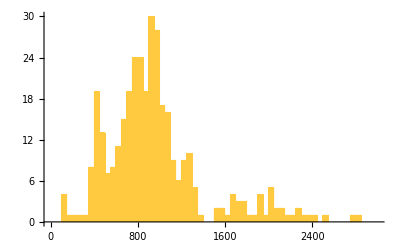

```mathematica
fullgenedepth=Histogram[fullgenomeSNPEFF[[All,Position[header,"DP"][[1,1]]]],{50},PlotRange->{{0,3000},Automatic}]
```

There are a few low outliers:

```mathematica
Select[fullgenomeSNPEFF[[All,Position[header,"DP"][[1,1]]]],#<300&]
```

{292,158,130,143,205,129,124}

There is one high outlier:

```mathematica
Select[fullgenomeSNPEFF[[All,Position[header,"DP"][[1,1]]]],#>3000&]
```

{4828}

Mean depth:

```mathematica
Mean[fullgenomeSNPEFF[[All,129]]]//N
```

968.839

Below, we will also compare genes bearing mutations to those with upstream variants, so copying from above:

The list of 333 genes that bear a mutation from the previous section:

```mathematica
genelist={"ABP1","ACB1","ACC1","ADE6","ADR1","AFT1","AGP1","AHK1","ALD5","ALY2","APC2","ARO3","ASN1","ATG11","ATG2","ATG39","BDS1","BIR1","BLM10","BNA6","BNI1","BNI4","BRR2","BSD2","BUL1","BUL2","CAJ1","CCC2","CCR4","CCW12","CDC25","CIC1","CLB3","CLN3","CNE1","COG1","COG3","COI1","COQ1","CPA1","CSM3","CUE3","CWC22","CWH41","CYK3","DAL2","DBF20","DBP10","DDR48","DNF1","DOA4","DOT6","DSC2","DSE4","DUS4","EBS1","ECM14","ECM22","EFR3","ELO3","ERB1","ERG1","ERG27","ERG7","ERG9","FAS2","FAU1","FCY2","FET4","FIG2","FIG4","FLC2","FMP52","FRE6","FSF1","FYV10","FYV6","FZF1","GAS4","GAT1","GCD2","GID12","GPB1","GPB2","GPH1","GSC2","HBT1","HEH2","HHF2","HIS4","HMF1","HO","HOB2","HRT3","HSL1","HSP104","HUL5","HXT13","IDP1","IES3","ILV2","IMA1","INP2","IOC4","IPI3","IRC20","IRC8","IST2","ISU1","ITC1","KAR3","KGD1","KIN1","KIN82","KRE5","KSP1","KTR3","LAM1","LAM6","LOS1","LRG1","MAM3","MAS2","MCK1","MCM5","MCT1","MDH2","MDL2","MDM30","MET10","MET30","MEX67","MHP1","MKT1","MLF3","MLH3","MLS1","MMS4","MNN9","MOT1","MPA43","MRL1","MRPL36","MSC6","MSS2","MTR4","MYG1","MYO2","NAM8","NAR1","NFT1","NGG1","NIP100","NPL3","NSR1","NUC1","NUG1","OAF1","OCA4","OCA5","OPI1","OSH2","PBP2","PBS2","PCL5","PDA1","PDR1","PDR10","PDX1","PET111","PET127","PEX2","PFK26","PHM7","PHO23","PHO81","PHO84","PIB1","PKP1","PLB2","PMA1","POL3","PPQ1","PRC1","PRI1","PRI2","PRP2","PRP8","PTK2","PYK2","QRI7","RAD16","RAD17","RAD26","RBK1","RCE1","RCK2","RCO1","REC102","RED1","RHO1","RIM11","RIM21","RKM3","RMP1","RNY1","ROG1","RPA135","RPI1","RPL22A","RPL2A","RPL39","RPS15","RPS2","RPT5","RRB1","RRG7","RRP46","RRP6","RSC1","RSE1","RTC2","SAK1","SAP4","SBE2","SEC8","SET2","SFP1","SHP1","SIW14","SKN1","SMC2","SMY2","SNF7","SNT2","SPC105","SPO77","SPS100","SRP40","SSE1","SSK2","SSQ1","SSZ1","STE5","STP3","STT3","SUB2","SUC2","SUM1","SWC5","SWS2","SWT1","SYF2","SYG1","TAF8","TAH11","TAO3","TCO89","TFB1","TFG1","TIM54","TOM1","TOP1","TOP2","TOS3","TPS3","TRK2","TRL1","TUS1","UBC1","UBP5","UBR2","UBX7","UGA3","UGA4","UIP5","ULS1","UME6","URA2","URB1","USA1","UTP21","UTP8","VBA1","VCX1","VHR2","VID22","VPS13","VPS74","VRP1","VTC1","VTC3","VTC4","VTC5","WAR1","YAP6","YBR242W","YBR292C","YCF1","YCK1","YCT1","YDL199C","YDR003W-A","YDR157W","YDR541C","YEF1","YGR126W","YGR130C","YGR266W","YHC1","YHC3","YIH1","YIL092W","YLL066W-B","YLR108C","YLR296W","YML119W","YMR027W","YMR317W","YOR029W","YOR1","YOR296W","YOR343C","YPK1","YPL113C","YPR078C","YPR089W","YPT6","YRA1","YRB2","ZDS2","ZRT1","ZRT3"};
```

```mathematica
genelistSYS={"YAL021C","YAL040C","YAL051W","YAL053W","YAL056W","YAL058W","YBL058W","YBR003W","YBR030W","YBR086C","YBR098W","YBR114W","YBR122C","YBR147W","YBR172C","YBR205W","YBR231C","YBR233W","YBR242W","YBR273C","YBR290W","YBR292C","YCL025C","YCL030C","YCR036W","YCR059C","YCR088W","YCR089W","YCR091W","YCR095C","YDL019C","YDL031W","YDL066W","YDL073W","YDL084W","YDL102W","YDL104C","YDL107W","YDL117W","YDL128W","YDL155W","YDL170W","YDL176W","YDL199C","YDL210W","YDL223C","YDL227C","YDL240W","YDR003W-A","YDR035W","YDR069C","YDR089W","YDR103W","YDR122W","YDR135C","YDR157W","YDR176W","YDR177W","YDR206W","YDR207C","YDR216W","YDR259C","YDR270W","YDR310C","YDR311W","YDR313C","YDR351W","YDR372C","YDR381C-A","YDR381W","YDR432W","YDR457W","YDR458C","YDR541C","YEL041W","YEL069C","YER004W","YER006W","YER048C","YER056C","YER057C","YER064C","YER072W","YER073W","YER088C","YER129W","YER144C","YER156C","YER157W","YER166W","YER172C","YER178W","YER183C","YFL007W","YFL021W","YFR030W","YFR031C","YFR031C-A","YFR047C","YGL008C","YGL013C","YGL022W","YGL027C","YGL071W","YGL093W","YGL110C","YGL123W","YGL131C","YGL133W","YGL141W","YGL144C","YGL179C","YGL223C","YGL229C","YGL254W","YGL255W","YGR032W","YGR037C","YGR056W","YGR061C","YGR083C","YGR095C","YGR126W","YGR128C","YGR129W","YGR130C","YGR143W","YGR159C","YGR175C","YGR186W","YGR193C","YGR233C","YGR266W","YGR278W","YGR281W","YGR287C","YHL020C","YHL029C","YHR024C","YHR052W","YHR064C","YHR071W","YHR072W","YHR082C","YHR086W","YHR132C","YHR135C","YHR139C","YHR155W","YHR165C","YHR190W","YIL042C","YIL046W","YIL047C","YIL063C","YIL092W","YIL097W","YIL107C","YIL119C","YIL125W","YIL129C","YIL162W","YIR008C","YIR029W","YJL012C","YJL042W","YJL050W","YJL051W","YJL054W","YJL059W","YJL084C","YJL087C","YJL128C","YJL130C","YJL168C","YJL189W","YJL208C","YJL210W","YJR035W","YJR046W","YJR059W","YJR089W","YKL014C","YKL045W","YKL101W","YKL126W","YKL175W","YKL205W","YKR044W","YKR050W","YKR092C","YKR103W","YLL026W","YLL040C","YLL051C","YLL055W","YLL066W-B","YLR024C","YLR025W","YLR052W","YLR061W","YLR072W","YLR097C","YLR100W","YLR108C","YLR110C","YLR127C","YLR145W","YLR228C","YLR247C","YLR248W","YLR261C","YLR263W","YLR274W","YLR296W","YLR298C","YLR310C","YLR312C","YLR329W","YLR337C","YLR341W","YLR368W","YLR369W","YLR372W","YLR373C","YLR375W","YLR403W","YLR405W","YLR409C","YLR425W","YML029W","YML049C","YML076C","YML109W","YML111W","YML114C","YML119W","YML123C","YMR006C","YMR027W","YMR044W","YMR048W","YMR049C","YMR075W","YMR088C","YMR108W","YMR131C","YMR139W","YMR163C","YMR173W","YMR212C","YMR257C","YMR261C","YMR274C","YMR275C","YMR297W","YMR317W","YMR319C","YNL030W","YNL032W","YNL074C","YNL081C","YNL085W","YNL088W","YNL097C","YNL117W","YNL133C","YNL182C","YNL233W","YNL240C","YNL242W","YNL249C","YNL271C","YNL294C","YNL307C","YNL325C","YNR011C","YNR016C","YNR031C","YNR067C","YOL006C","YOL040C","YOL060C","YOL073C","YOL084W","YOL126C","YOL132W","YOL164W","YOR001W","YOR017W","YOR029W","YOR117W","YOR166C","YOR191W","YOR221C","YOR271C","YOR296W","YOR303W","YOR305W","YOR326W","YOR328W","YOR336W","YOR343C","YOR347C","YOR354C","YOR368W","YOR371C","YPL019C","YPL050C","YPL082C","YPL106C","YPL113C","YPL123C","YPL135W","YPL164C","YPL169C","YPL174C","YPL179W","YPL180W","YPL231W","YPL270W","YPR010C","YPR049C","YPR055W","YPR078C","YPR079W","YPR089W","YPR111W","YPR117W","YPR141C","YPR145W","YPR160W","YPR165W"};
```

```mathematica
{Length[genelist],Length[genelistSYS]}
```

{333,333}

### Dropping genes with too many uncalled genotypes and dropping genotypic calls with <5 depth

#### Processing and dropping genes with two many poor quality genotypes

Sites that were hard to call (low depth or no genotype call) can indicate duplicated genes and alignment problems.  Here we identify these:

```mathematica
droppos=-1+Position[header,"OLY077_S101"][[1,1]];(*# columns to be dropped before first sample*)
```

```mathematica
topos=Position[header,"ZnBM47_S95"][[1,1]];(*# last sample column*)
```

Extracting the ref vs alt call in genomeSNPEFF:

```mathematica
genomeSNPEFF=Table[".",{i,1,Length[fullgenomeSNPEFF]},{j,1,topos-droppos}];
```

```mathematica
genomeSNPEFF[[1]]//Length
```

110

```mathematica
For[i=1,i≤Length[fullgenomeSNPEFF],i++,
For[j=1+droppos,j≤topos,j++,
temp=StringSplit[fullgenomeSNPEFF[[i,j]],{":"}];
genomeSNPEFF[[i,j-droppos]]=temp[[1]];
]
]
```

```mathematica
genomeSNPEFF//Length
```

348

```mathematica
Tally[Select[genomeSNPEFF[[1]],#≠"."&]]
```

{{1,36},{0,73}}

All mutant sites and the tally of mutations in them:

```mathematica
summarytable=Table[{fullgenomeSNPEFF[[i,1]],fullgenomeSNPEFF[[i,3]],fullgenomeSNPEFF[[i,8]],fullgenomeSNPEFF[[i,9]],Sort[Tally[genomeSNPEFF[[i]]]]},{i,1,Length[genomeSNPEFF]}];
```

The set of sites where the number of “.” calls was ≥5:

```mathematica
dropthese=Select[summarytable,(#[[5,1,1]]==".")&&(#[[5,1,2]]≥5)&];
dropthese//MatrixForm
dropthese//Length
```

(chrII | 258784 | FLR1 | MODIFIER | {{.,53},{0,49},{1,8}}
chrII | 643488 | DUR1%2C2 | MODIFIER | {{.,96},{0,1},{1,13}}
chrII | 643489 | DUR1%2C2 | MODIFIER | {{.,104},{0,1},{1,5}}
chrIII | 295234 | HMRA2 | MODIFIER | {{.,35},{0,72},{1,3}}
chrIV | 273629 | PHO2 | MODIFIER | {{.,11},{0,74},{1,25}}
chrIV | 336206 | CBS1 | MODIFIER | {{.,5},{0,91},{1,14}}
chrIV | 384223 | NAT1 | MODIFIER | {{.,17},{0,31},{1,62}}
chrIV | 384226 | NAT1 | MODIFIER | {{.,38},{0,10},{1,62}}
chrIV | 384262 | NAT1 | MODIFIER | {{.,24},{0,25},{1,61}}
chrIV | 384290 | NAT1 | MODIFIER | {{.,11},{0,70},{1,29}}
chrIV | 1341641 | DOT1 | MODIFIER | {{.,5},{0,98},{1,7}}
chrV | 116118 | URA3 | MODIFIER | {{.,7},{0,81},{1,22}}
chrVII | 278779 | MON1 | MODIFIER | {{.,5},{0,96},{1,9}}
chrVII | 323365 | TOS8 | MODIFIER | {{.,24},{0,76},{1,10}}
chrVII | 701187 | SRB5 | MODIFIER | {{.,43},{0,61},{1,6}}
chrVII | 735813 | COG2 | MODIFIER | {{.,13},{0,95},{1,2}}
chrVII | 735814 | COG2 | MODIFIER | {{.,13},{0,95},{1,2}}
chrVII | 811448 | NSR1 | MODIFIER | {{.,92},{0,13},{1,5}}
chrVIII | 2292 | COS8 | MODIFIER | {{.,10},{0,85},{1,15}}
chrVIII | 85388 | PRS3 | MODIFIER | {{.,23},{0,85},{1,2}}
chrVIII | 85390 | PRS3 | MODIFIER | {{.,23},{0,85},{1,2}}
chrX | 745669 | COS5 | MODIFIER | {{.,27},{0,39},{1,44}}
chrXI | 196211 | 01-Oct | MODIFIER | {{.,59},{0,44},{1,7}}
chrXI | 379671 | tV(AAC)K2 | MODIFIER | {{.,60},{0,49},{1,1}}
chrXI | 379672 | tV(AAC)K2 | MODIFIER | {{.,28},{0,81},{1,1}}
chrXI | 517454 | KAE1 | MODIFIER | {{.,107},{0,1},{1,2}}
chrXI | 517455 | KAE1 | MODIFIER | {{.,105},{0,1},{1,4}}
chrXII | 251194 | FCF2 | MODIFIER | {{.,10},{0,97},{1,3}}
chrXII | 421496 | TIS11 | MODIFIER | {{.,9},{0,93},{1,8}}
chrXII | 593143 | YLR225C | MODIFIER | {{.,95},{0,1},{1,14}}
chrXII | 1065029 | YLR460C | MODIFIER | {{.,12},{0,97},{1,1}}
chrXVI | 850633 | YPR158W-A | MODIFIER | {{.,91},{0,14},{1,5}})

32

```mathematica
dropme=Union[dropthese[[All,3]]]
%//Length
```

{01-Oct,CBS1,COG2,COS5,COS8,DOT1,DUR1%2C2,FCF2,FLR1,HMRA2,KAE1,MON1,NAT1,NSR1,PHO2,PRS3,SRB5,TIS11,TOS8,tV(AAC)K2,URA3,YLR225C,YLR460C,YPR158W-A}

24

We’ll remove these specific sites by position too (not by gene, as these sites may be upstream of many genes, which hasn’t been processed yet):

```mathematica
dropmeposition=Union[dropthese[[All,2]]];
```

Depth of coverage for these genes is similar:

```mathematica
Select[fullgenomeSNPEFF,MemberQ[dropme,#[[8]]]&][[All,{8,129}]]
Mean[%[[All,2]]]//N
```

{{FLR1,303},{DUR1%2C2,292},{DUR1%2C2,158},{HMRA2,1986},{PHO2,702},{CBS1,709},{NAT1,1327},{NAT1,1253},{NAT1,1231},{NAT1,987},{NAT1,838},{DOT1,978},{URA3,1248},{MON1,821},{TOS8,502},{TOS8,2018},{SRB5,1355},{SRB5,1281},{COG2,860},{COG2,859},{NSR1,130},{COS8,773},{PRS3,1684},{PRS3,1522},{COS5,657},{01-Oct,2022},{tV(AAC)K2,1747},{tV(AAC)K2,143},{tV(AAC)K2,205},{KAE1,129},{KAE1,124},{FCF2,928},{TIS11,721},{YLR225C,450},{YLR460C,1124},{YPR158W-A,355}}

900.611

Mapping quality is also poorer on average, with the mean at the bottom 8.9% tail:

```mathematica
Select[fullgenomeSNPEFF,MemberQ[dropme,#[[8]]]&][[All,{8,133}]]
Mean[%[[All,2]]]//N
Length[Select[fullgenomeSNPEFF[[All,133]],#<%&]]/Length[fullgenomeSNPEFF[[All,133]]]//N//PercentForm
```

{{FLR1,55.54},{DUR1%2C2,59.98},{DUR1%2C2,60.},{HMRA2,56.3},{PHO2,60.},{CBS1,60.},{NAT1,58.99},{NAT1,58.98},{NAT1,57.38},{NAT1,53.14},{NAT1,52.7},{DOT1,60.},{URA3,60.},{MON1,57.64},{TOS8,53.69},{TOS8,60.},{SRB5,59.95},{SRB5,59.94},{COG2,58.17},{COG2,58.1},{NSR1,60.},{COS8,59.57},{PRS3,52.77},{PRS3,52.02},{COS5,57.36},{01-Oct,60.},{tV(AAC)K2,56.25},{tV(AAC)K2,51.59},{tV(AAC)K2,50.94},{KAE1,60.},{KAE1,60.},{FCF2,60.},{TIS11,60.},{YLR225C,60.},{YLR460C,54.43},{YPR158W-A,59.56}}

57.6386

8.908%

Dropping all sites (32)  with ≥5 “.” calls:

```mathematica
Length[fullgenomeSNPEFF];
fullgenomeSNPEFF=Select[fullgenomeSNPEFF,(MemberQ[dropme,#[[8]]]==False)||(MemberQ[dropmeposition,#[[3]]]==False)&];
%%-Length[fullgenomeSNPEFF]
```

32

#### Processing and dropping sites with <5 depth

We next scan for sites that are called with depth <5 (note that we do not filter on the depth for each allele, just total depth at that site in that sample).

An example of a site with low coverage:

```mathematica
Position[fullgenomeSNPEFF[[All,3]],415764][[1,1]];
fullgenomeSNPEFF[[%,49;;53]]
```

{0:10,0:10:99:0,301,1:1,1:2:2:2,0,0:3,0:3:99:0,100,0:5,0:5:99:0,99,0:2,1:3:21:0,21}

```mathematica
For[i=1;altered={},i≤Length[fullgenomeSNPEFF],i++,
For[j=1+droppos,j≤topos,j++,
temp=StringSplit[fullgenomeSNPEFF[[i,j]],{":"}];
If[ToExpression[temp[[3]]]<5,temp[[1]]=".";fullgenomeSNPEFF[[i,j]]=StringRiffle[temp,":"];AppendTo[altered,{i,j}]];
]
]
```

```mathematica
altered
```

The example is now corrected:

```mathematica
Position[fullgenomeSNPEFF[[All,3]],415764][[1,1]];
fullgenomeSNPEFF[[%,49;;53]]
```

{0:10,0:10:99:0,301,.:1,1:2:2:2,0,.:3,0:3:99:0,100,0:5,0:5:99:0,99,.:2,1:3:21:0,21}

Extracting the ref vs alt call in genomeSNPEFF:

```mathematica
genomeSNPEFF=Table[".",{i,1,Length[fullgenomeSNPEFF]},{j,1,topos-droppos}];
```

```mathematica
genomeSNPEFF[[1]]//Length
```

110

```mathematica
For[i=1,i≤Length[fullgenomeSNPEFF],i++,
For[j=1+droppos,j≤topos,j++,
temp=StringSplit[fullgenomeSNPEFF[[i,j]],{":"}];
genomeSNPEFF[[i,j-droppos]]=temp[[1]];
]
]
```

```mathematica
genomeSNPEFF//Length
```

316

```mathematica
Tally[Select[genomeSNPEFF[[1]],#≠"."&]]
```

{{1,36},{0,73}}

All mutant sites and the tally of mutations in them (ignore the error, which comes from sorting so that “.” is last):

```mathematica
summarytable=Table[{fullgenomeSNPEFF[[i,1]],fullgenomeSNPEFF[[i,3]],fullgenomeSNPEFF[[i,8]],fullgenomeSNPEFF[[i,9]],SortBy[Tally[genomeSNPEFF[[i]]],ToExpression[#]&]},{i,1,Length[genomeSNPEFF]}];
```

ToExpression::sntx: Invalid syntax in or before ". ".
                                                  ^

General::stop: Further output of ToExpression::sntx will be suppressed during this calculation.

This does not change the number of genes with mutations detected (i.e., all tallies with only two elements include the ref and alt allele):

```mathematica
Select[summarytable,Length[#[[5]]]≤2&]//MatrixForm
```

(chrII | 684840 | OM14 | MODIFIER | {{0,2},{1,108}}
chrIII | 309030 | YCR102C | MODIFIER | {{0,1},{1,109}}
chrV | 406772 | GLO3 | MODIFIER | {{0,109},{1,1}}
chrV | 407063 | GLO3 | MODIFIER | {{0,1},{1,109}}
chrVI | 193508 | tS(GCU)F | MODIFIER | {{0,1},{1,109}}
chrVII | 649059 | GCD2 | MODIFIER | {{0,109},{1,1}}
chrXI | 146956 | PIR1 | MODIFIER | {{0,109},{1,1}}
chrXI | 379623 | tV(AAC)K2 | MODIFIER | {{0,1},{1,109}}
chrXI | 489841 | DBP7 | MODIFIER | {{0,109},{1,1}}
chrXII | 185314 | YEH2 | MODIFIER | {{0,1},{1,109}}
chrXII | 881947 | SEC61 | MODIFIER | {{0,1},{1,109}})

#### Stats for the remaining SNPs

Plotting the depth of coverage at each site:

```mathematica
Mean[fullgenomeSNPEFF[[All,129]]]//N
```

983.203

```mathematica
Max[fullgenomeSNPEFF[[All,129]]]
```

4828

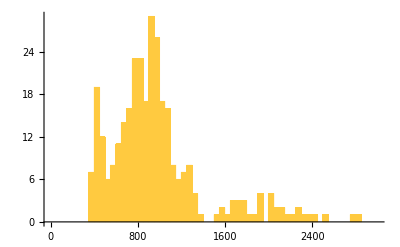

```mathematica
Histogram[fullgenomeSNPEFF[[All,129]],{50},PlotRange->{{0,3000},Automatic}]
```

#### Processing SnpEff

The gene list provided by SnpEff just picks the first of the genes, not necessarily the closest:

```mathematica
fullgenomeSNPEFF[[1;;4,Position[header,"gene"][[1,1]]]]
```

{YAL065C,FLO9,YAL056C-A,ACS1}

```mathematica
annotations=fullgenomeSNPEFF[[All,Position[header,"ANN"][[1,1]]]];
```

Looking through the SnpEff annotations and finding which genes are nearest, with the SNP in the upstream region:

```mathematica
For[i=1;regpotential={};morethanone={};closeregpotential={},i≤Length[annotations],i++,
temp=StringSplit[StringSplit[fullgenomeSNPEFF[[i,Position[header,"ANN"][[1,1]]]],","],"|"];
temp2=Select[temp,#[[2]]=="upstream_gene_variant"&];
temp2=temp2/."ADE5%2C7"->"ADE5,7"/."WARNING_TRANSCRIPT_NO_START_CODON"->10^6/."WARNING_TRANSCRIPT_MULTIPLE_STOP_CODONS"->10^6/."WARNING_TRANSCRIPT_INCOMPLETE"->10^6;
If[Length[temp2]==0,AppendTo[regpotential,{"","","",""}],
For[j=1;dist={};closegene={};systname={},j≤Length[temp2],j++,
AppendTo[dist,ToExpression[Last[temp2[[j]]]]];
AppendTo[closegene,temp2[[j,4]]];
AppendTo[systname,temp2[[j,5]]]
];
closest=PositionSmallest[ToExpression[dist]][[1]];
AppendTo[regpotential,{temp2[[closest,4]],temp2[[closest,5]],dist[[closest]],temp2[[closest,10]]}];
If[Length[numclose=Select[Transpose[{dist,closegene}],#[[1]]≤500&]]>1,AppendTo[morethanone,{i,numclose}]];
]
]
```

```mathematica
regpotential[[1;;4]]
```

{{TDA8,YAL064C-A,1849,c.-1849C>G},{GDH3,YAL062W,771,c.-771G>A},{FLC2,YAL053W,3064,c.-3064C>T},{FLC2,YAL053W,412,c.-412C>T}}

Appending the nearest gene (SNP must be upstream) and distance to fullgenomeSNPEFF and updating the header:

```mathematica
fullgenomeSNPEFF=Table[Flatten[{fullgenomeSNPEFF[[i]],regpotential[[i]]}]/.Missing["NotAvailable"]->"",{i,1,Length[fullgenomeSNPEFF]}];
```

```mathematica
newheader=Join[Table[StringSplit[header[[i]],"_"][[1]],{i,1,Length[header]}],{"Upstream of nearest gene","Systematic name of nearest gene","Distance","Effect on closest"}]
```

{CHROM,chr,POS,REF,ALT,QUAL,FORMAT,gene,effect,mut,gene,base,aa,ANN,OLY077,CdBM23,CdBM25,CdBM26,CdBM29,CdBM30,CdBM32,CdBM36,CdBM37,CdBM39,CdBM42,CdBM43,CdBM44,CdBM45,CdBM46,CdBM47,CdBM48,CoBM12,CoBM14,CoBM15,CoBM16,CoBM17,CoBM18,CoBM1,CoBM20,CoBM21,CoBM2,CoBM3,CoBM4,CoBM5,CoBM6,CoBM7,CoBM8,CuBM10,CuBM11,CuBM12,CuBM13,CuBM14,CuBM15,CuBM16,CuBM17,CuBM18,CuBM3,CuBM4,CuBM6,CuBM7,CuBM8,CuBM9,MnBM12,MnBM13,MnBM14,MnBM15,MnBM16,MnBM17,MnBM18,MnBM20,MnBM21,MnBM23,MnBM24,MnBM25,MnBM27,MnBM28,MnBM29,MnBM31,MnBM32,MnBM34,MnBM38,MnBM39,MnBM42,MnBM44,NiBM11,NiBM12,NiBM14,NiBM16,NiBM17,NiBM21,NiBM22,NiBM24,NiBM25,NiBM27,NiBM28,NiBM29,NiBM30,NiBM4,NiBM6,NiBM8,NiBM9,ZnBM11,ZnBM12,ZnBM15,ZnBM16,ZnBM17,ZnBM19,ZnBM22,ZnBM23,ZnBM25,ZnBM28,ZnBM29,ZnBM31,ZnBM34,ZnBM37,ZnBM38,ZnBM39,ZnBM41,ZnBM42,ZnBM43,ZnBM44,ZnBM45,ZnBM46,ZnBM47,AC,AF,AN,BaseQRankSum,DP,FS,MLEAC,MLEAF,MQ,MQRankSum,QD,ReadPosRankSum,SOR,LOF,Upstream of nearest gene,Systematic name of nearest gene,Distance,Effect on closest}

```mathematica
intergenicCLOSE=Sort[Select[regpotential,#[[3]]≤500&]][[All,{1,3}]]
Length[%]
```

{{AAC3,218},{ADE5,7,256},{ADH4,312},{ADH7,39},{ALE1,354},{ALT2,425},{ARC15,145},{ARG4,124},{ARO7,178},{ATH1,121},{AVO2,46},{BMT5,125},{BNA6,418},{BUB2,75},{CBP4,483},{CCA1,302},{CLB5,393},{COG5,74},{COQ8,159},{CRG1,388},{CSE1,136},{CWC27,135},{DAD3,136},{DAM1,69},{DAT1,100},{DNF3,48},{EAP1,25},{EHT1,298},{EMI2,199},{EPO1,366},{ERG26,228},{ESF1,107},{FCY21,35},{FLC2,412},{FLC3,74},{FRA1,58},{GCN3,187},{GEX1,250},{GLC8,209},{GPI13,119},{GPR1,90},{GSC2,193},{HFA1,78},{HMG2,500},{HOR7,468},{HOT1,113},{HOT13,40},{HRD1,403},{HSK3,21},{HSP104,430},{HYM1,408},{IML2,414},{IRC3,120},{ITC1,286},{KTI11,12},{LDB16,121},{LIA1,178},{MEK1,44},{MMS1,77},{MMT1,208},{MNN5,182},{MRP49,334},{MRPL9,124},{MSF1,181},{MSO1,121},{MST1,193},{NAM2,59},{NAR1,246},{NBP1,199},{NDD1,145},{NOC2,97},{NOP4,161},{NOP56,163},{NOP9,144},{OAF1,31},{OCA5,132},{OM45,339},{ORC4,68},{PAH1,156},{PDA1,13},{PDC6,459},{PEP4,56},{PHO80,184},{PHO91,146},{PIL1,171},{PMT6,334},{POM34,146},{POP2,388},{PPT2,130},{PPZ1,319},{PRM7,223},{PRO2,222},{PRP11,96},{PUF4,329},{RAD14,159},{RAS1,314},{RBD2,106},{RFC3,128},{RPA12,109},{RPH1,21},{RPL11B,152},{RPL17B,151},{RPL18A,212},{RPL22B,182},{RPL3,187},{RPL34B,418},{RPO41,393},{RPS0A,457},{RPS22A,287},{RRM3,167},{RSA1,210},{RSE1,3},{SAM50,271},{SCM4,171},{SDA1,245},{SDD2,171},{SDD4,156},{SDO1,389},{SEC12,92},{SEC31,86},{SET5,10},{SET5,11},{SMA1,137},{SMI1,441},{SNR61,94},{SNR63,207},{SOD2,365},{SPC42,490},{SPO21,157},{SSA1,331},{SWI6,47},{SYC1,137},{SYG1,48},{TCD2,270},{THI2,165},{TIF5,50},{TOK1,222},{TOM7,312},{TOP1,244},{TRE1,71},{UBP13,153},{UBR2,104},{UBX4,81},{VHR1,365},{VMA13,103},{VMA13,302},{VPH1,27},{VPS54,170},{VPS68,482},{VTA1,125},{VTC5,232},{YBR300C,372},{YBR300C,388},{YCL012C,89},{YCR006C,476},{YDL180W,439},{YDR169C-A,75},{YEL043W,82},{YGL063C-A,134},{YGL063C-A,135},{YGR125W,167},{YGR293C,385},{YHR139C-A,41},{YIL169C,437},{YJL107C,203},{YJL193W,394},{YKE2,264},{YKR005C,142},{YLL054C,175},{YME2,393},{YMR001C-A,116},{YNL190W,91},{YOP1,328},{YOR121C,106},{YOR121C,112},{YPK9,170},{YPL068C,134},{YPL222C-A,342},{YPQ2,188},{YPR078C,262},{ZWF1,373}}

181

```mathematica
intergenicFURTHER=Sort[Select[regpotential,#[[3]]>500&]][[All,{1,3}]]
Length[%]
```

{{AGA1,549},{ALE1,3743},{AMF1,1098},{ATG18,1303},{BET4,823},{BIO2,2017},{BRX1,2745},{BUD3,3536},{BUL2,881},{CNL1,2327},{COF1,810},{CUP9,1728},{DDR2,560},{DLD3,1630},{DNF2,609},{ERB1,2135},{ERR2,2305},{ETT1,520},{FAP7,902},{FLC2,3064},{FLO1,4814},{FLO1,4821},{FLO10,1151},{FMN1,1812},{FRE8,2238},{GDH3,771},{GLC3,554},{GLO3,2420},{GLO3,2711},{GLO3,2788},{GUA1,3110},{HXT7,530},{KGD1,599},{LGE1,1771},{LYS9,1323},{MDN1,2506},{MIX17,3488},{MLP1,2247},{MNN4,755},{MRH1,1209},{MSC6,709},{MSS4,3233},{NCE102,738},{NGG1,1285},{NSR1,843},{OCA6,1410},{PAD1,696},{PAD1,850},{PAU10,928},{PAU17,1332},{PDS5,919},{PEX2,3572},{PGA1,1965},{PMT4,1133},{PRE10,843},{PSA1,2688},{PSA1,3022},{PSP2,1835},{RCK1,691},{RPC82,3823},{RPL4B,1275},{RPL8B,3391},{RPO26,1539},{SAM1,2118},{SDD4,509},{SDD4,686},{SEC27,1488},{SMC6,3340},{SNR52,2977},{SPT21,519},{SQT1,1213},{SSF2,523},{TDA8,1849},{TIM10,3772},{TMS1,2180},{TOS8,1751},{TRM11,2882},{URA2,1149},{USO1,1660},{VOA1,1401},{VPS1,4066},{WTM1,908},{YAE1,1312},{YAL042C-A,4154},{YAP1802,1319},{YBL070C,2626},{YBL070C,2681},{YBL111C,1148},{YBL111C,1149},{YBL111C,1166},{YBL111C,1173},{YBL111C,1182},{YDL022C-A,832},{YDL186W,1823},{YDL240C-A,3782},{YDR034C-D,544},{YDR537C,2496},{YER076C,970},{YER137C,1594},{YER137C,1595},{YER137C,1597},{YFL021C-A,2539},{YGL014C-A,2488},{YGR269W,1642},{YHL005C,1286},{YHR140W,629},{YIL154C,2257},{YIR018C-A,680},{YIR018C-A,3557},{YJL045W,1390},{YJL107C,514},{YJL169W,2579},{YJL169W,2593},{YKL031W,2448},{YKL162C-A,882},{YLL066W-A,632},{YLL066W-A,635},{YLR302C,2362},{YML018C,701},{YMR182W-A,3578},{YMR242W-A,1338},{YNR062C,3447},{YOL150C,909},{YOR343W-A,4558},{YOR376W,1775},{YOR392W,1075},{YPL257W-A,647},{YPR014C,2379},{YPR142C,822},{YRO2,660},{ZRT1,961},{ZRT1,1577}}

132

Some sites have more than one gene within 500bp, but these were not analysed (only the closest gene):

```mathematica
morethanone(*row, closest gene, distance to all genes within 500bp*)
Length[%]
```

{{4,{{465,ACS1},{412,FLC2}}},{7,{{331,SSA1},{412,EFB1}}},{15,{{410,YBL071C-B},{12,KTI11}}},{29,{{188,SNR43},{121,LDB16}}},{82,{{302,CCA1},{398,RPH1}}},{86,{{182,RPL22B},{363,MIL1}}},{94,{{430,MTO1},{256,ADE5,7}}},{99,{{346,PRP43},{159,COQ8}}},{101,{{134,YGL063C-A},{411,PYC1}}},{102,{{135,YGL063C-A},{410,PYC1}}},{103,{{377,YGL015C},{329,PUF4}}},{130,{{167,RRM3},{207,ERC1}}},{132,{{41,YHR139C-A},{112,YHR140W}}},{139,{{492,TMA108},{339,OM45}}},{145,{{48,SYG1},{438,YIL046W-A}}},{151,{{287,RPS22A},{344,RPL39}}},{159,{{222,TOK1},{389,SRS2}}},{163,{{144,NOP9},{149,YJL009W}}},{164,{{237,NTA1},{109,RPA12}}},{175,{{40,HOT13},{452,YKL083W}}},{200,{{125,VTA1},{145,SWI6}}},{201,{{223,VTA1},{47,SWI6}}},{207,{{59,NAM2},{478,SMC6}}},{209,{{199,NBP1},{364,GAB1}}},{210,{{370,TAF8},{100,DAT1}}},{212,{{3,RSE1},{118,GSF2}}},{217,{{116,YMR001C-A},{500,MIX17}}},{222,{{171,SDD2},{338,RCO1}}},{227,{{348,EAR1},{113,HOT1}}},{231,{{159,RAD14},{334,ERG2}}},{238,{{275,MID1},{128,RFC3}}},{240,{{246,NAR1},{346,LAP3}}},{247,{{92,SEC12},{142,BUD17}}},{268,{{354,ALE1},{373,HEM15}}},{271,{{181,GEP3},{97,NOC2}}},{280,{{145,NDD1},{218,NUD1}}},{286,{{106,RBD2},{183,YPL245W}}},{290,{{71,TRE1},{196,SPT14}}},{292,{{130,PPT2},{310,PXA1}}},{294,{{135,CWC27},{188,TIM50}}},{309,{{262,YPR078C},{342,MRL1}}}}

41

These were the genes with more than 1 intergenic mutation within 500 basepairs

```mathematica
Select[Tally[intergenicCLOSE[[All,1]]],#[[2]]>1&]
```

{{SET5,2},{VMA13,2},{YBR300C,2},{YGL063C-A,2},{YOR121C,2}}

Of these, the last three are dubious open-reading frames, leaving

("SET5" | 2
"VMA13" | 2)

Only VMA13 mutants are known to affect metal resistance (SGD).

These are the set of genes with both intergenic and genic SNPS in the dataset:

```mathematica
Intersection[genelist,intergenicCLOSE[[All,1]]]
Length[%]
```

{BNA6,FLC2,GSC2,HSP104,ITC1,NAR1,OAF1,OCA5,PDA1,RSE1,SYG1,TOP1,UBR2,VTC5,YPR078C}

15

#### Relating mutations to phenotypes (metal resistance, phosphorous metabolism, DNA repair)

Metal Resistance: The list of genes affecting metal resistance was downloaded from SGD (https://yeastgenome.org/observable/APO:0000090) on 23 May 2025:

```mathematica
metallist=Import["/Users/otto/Documents/Students/AnnaBazzicalupo/MetalAdaptation/Genomics/metal_resistance_annotations_23May2025.txt","tsv"];
```

```mathematica
metalhead=metallist[[2]]
```

{Gene,Gene Systematic Name,Phenotype,Experiment Type,Experiment Type Category,Mutant Information,Strain Background,Chemical,Details,Reference}

```mathematica
metallist=Drop[metallist,2];
```

Here we will use the Gene Systematic Name for comparison:

```mathematica
metalgenenames=Union[metallist[[All,2]]];
Length[%]
```

1791

Of the SNPs that are within 500bp of gene (upstream position), 176 genes are involved and 31.82% are listed as having metal tolerance phenotypes:

```mathematica
genelistCLOSESYS=Union[Sort[Select[regpotential,#[[3]]≤500&]][[All,2]]];
Intersection[genelistCLOSESYS,metalgenenames]
{Length[genelistCLOSESYS],Length[%],Length[%]/Length[genelistCLOSESYS]//N//PercentForm}
```

{YAL051W,YAL053W,YBL071W-A,YBR085W,YCL073C,YDR027C,YDR089W,YEL043W,YER169W,YER178W,YGL234W,YGR086C,YGR214W,YGR229C,YHR008C,YIL047C,YIL052C,YIL136W,YJL177W,YJL190C,YKL204W,YLL029W,YLR024C,YLR181C,YLR182W,YLR200W,YLR382C,YLR450W,YML016C,YML113W,YMR172W,YMR177W,YMR201C,YNL051W,YNL241C,YNR013C,YNR026C,YNR049C,YNR052C,YOL001W,YOL006C,YOL013C,YOL129W,YOR101W,YOR206W,YOR270C,YOR291W,YOR323C,YOR372C,YPL148C,YPL154C,YPL176C,YPL193W,YPR036W,YPR060C,YPR120C}

{176,56,31.82%}

By contrast, for the 333 genic SNPs, 121 (36.34%) were annotated as having metal tolerance, which is slightly higher by 14.2% than the close intergenic SNPs.

By comparison, of the SNPs that are not within 500bp of gene (upstream position), 115 genes are involved and only 20.87% are listed as having metal tolerance phenotypes:

```mathematica
genelistFURTHERSYS=Union[Sort[Select[regpotential,#[[3]]>500&]][[All,2]]];
Intersection[genelistFURTHERSYS,metalgenenames]
{Length[genelistFURTHERSYS],Length[%],Length[%]/Length[genelistFURTHERSYS]//N//PercentForm}
```

{YAL053W,YDR067C,YDR105C,YDR176W,YFR021W,YGL255W,YGR106C,YIL125W,YIL154C,YKL201C,YKR001C,YLL045C,YLR047C,YLR180W,YML017W,YML018C,YML111W,YMR179W,YMR242W-A,YOL124C,YOR376W,YPL055C,YPL177C,YPR190C}

{115,24,20.87%}

By contrast, for the 333 genic SNPs, 121 (36.34%) were annotated as having metal tolerance, which is substantially higher (by 74%) than for the further intergenic SNPs.

These are the set of genes with both close intergenic and genic SNPS in the dataset:

```mathematica
bothgenicintergenic=Intersection[genelistSYS,genelistCLOSESYS]
Length[%]
```

{YAL051W,YAL053W,YDR089W,YER178W,YFR047C,YGL133W,YGR032W,YHL029C,YIL047C,YLL026W,YLR024C,YML049C,YNL240C,YOL006C,YPR078C}

15

7 out of these 15 have metal tolerance effects noted in SGD:

```mathematica
whichones=Intersection[bothgenicintergenic,metalgenenames]
{Length[bothgenicintergenic],Length[%],Length[%]/Length[bothgenicintergenic]//N//PercentForm}
```

{YAL051W,YAL053W,YDR089W,YER178W,YIL047C,YLR024C,YOL006C}

{15,7,46.67%}

```mathematica
Select[regpotential,MemberQ[whichones,#[[2]]]&]//Sort//MatrixForm
```

(FLC2 | YAL053W | 412 | c.-412C>T
FLC2 | YAL053W | 3064 | c.-3064C>T
OAF1 | YAL051W | 31 | c.-31C>T
PDA1 | YER178W | 13 | c.-13C>A
SYG1 | YIL047C | 48 | c.-48_-47insT
TOP1 | YOL006C | 244 | c.-244delA
UBR2 | YLR024C | 104 | c.-104delT
VTC5 | YDR089W | 232 | c.-232_-231delAA)

Appending metal resistance phenotype information to the data:

```mathematica
For[i=1;newcolumn={},i≤Length[fullgenomeSNPEFF],i++,
nameSYS=fullgenomeSNPEFF[[i,11]];
If[MemberQ[metalgenenames,nameSYS],AppendTo[newcolumn,"METAL"],AppendTo[newcolumn,"No"]]
]
```

```mathematica
fullgenomeSNPEFF=Transpose[Append[Transpose[fullgenomeSNPEFF],newcolumn]];
```

Phosphorus metabolic process: 
The list of genes affecting phosphorous metabolism was downloaded from Amigo 2 (https://amigo.geneontology.org/amigo/term/GO:0006793) on 17 June2025:

```mathematica
pholist=Import["/Users/otto/Documents/Students/AnnaBazzicalupo/MetalAdaptation/Genomics/phosphate_metabolism_annotations_17Jun2025.tsv","tsv"];
```

```mathematica
phohead=pholist[[1]]
```

{gene,gene_id,gene_name,go_id,evidence}

```mathematica
pholist=Drop[pholist,1];
```

The gene name but not the systematic name is listed:

```mathematica
phogenenames=pholist[[All,1]];
Length[%]
```

480

Of the 287 genes with upstream intergenic mutations, 20 (7.0%) are annotated as affecting phosphorous metabolism:

```mathematica
intergenelist=Union[Sort[regpotential][[All,1]]]
intergenelist=Drop[intergenelist,1];
```

{,AAC3,ADE5,7,ADH4,ADH7,AGA1,ALE1,ALT2,AMF1,ARC15,ARG4,ARO7,ATG18,ATH1,AVO2,BET4,BIO2,BMT5,BNA6,BRX1,BUB2,BUD3,BUL2,CBP4,CCA1,CLB5,CNL1,COF1,COG5,COQ8,CRG1,CSE1,CUP9,CWC27,DAD3,DAM1,DAT1,DDR2,DLD3,DNF2,DNF3,EAP1,EHT1,EMI2,EPO1,ERB1,ERG26,ERR2,ESF1,ETT1,FAP7,FCY21,FLC2,FLC3,FLO1,FLO10,FMN1,FRA1,FRE8,GCN3,GDH3,GEX1,GLC3,GLC8,GLO3,GPI13,GPR1,GSC2,GUA1,HFA1,HMG2,HOR7,HOT1,HOT13,HRD1,HSK3,HSP104,HXT7,HYM1,IML2,IRC3,ITC1,KGD1,KTI11,LDB16,LGE1,LIA1,LYS9,MDN1,MEK1,MIX17,MLP1,MMS1,MMT1,MNN4,MNN5,MRH1,MRP49,MRPL9,MSC6,MSF1,MSO1,MSS4,MST1,NAM2,NAR1,NBP1,NCE102,NDD1,NGG1,NOC2,NOP4,NOP56,NOP9,NSR1,OAF1,OCA5,OCA6,OM45,ORC4,PAD1,PAH1,PAU10,PAU17,PDA1,PDC6,PDS5,PEP4,PEX2,PGA1,PHO80,PHO91,PIL1,PMT4,PMT6,POM34,POP2,PPT2,PPZ1,PRE10,PRM7,PRO2,PRP11,PSA1,PSP2,PUF4,RAD14,RAS1,RBD2,RCK1,RFC3,RPA12,RPC82,RPH1,RPL11B,RPL17B,RPL18A,RPL22B,RPL3,RPL34B,RPL4B,RPL8B,RPO26,RPO41,RPS0A,RPS22A,RRM3,RSA1,RSE1,SAM1,SAM50,SCM4,SDA1,SDD2,SDD4,SDO1,SEC12,SEC27,SEC31,SET5,SMA1,SMC6,SMI1,SNR52,SNR61,SNR63,SOD2,SPC42,SPO21,SPT21,SQT1,SSA1,SSF2,SWI6,SYC1,SYG1,TCD2,TDA8,THI2,TIF5,TIM10,TMS1,TOK1,TOM7,TOP1,TOS8,TRE1,TRM11,UBP13,UBR2,UBX4,URA2,USO1,VHR1,VMA13,VOA1,VPH1,VPS1,VPS54,VPS68,VTA1,VTC5,WTM1,YAE1,YAL042C-A,YAP1802,YBL070C,YBL111C,YBR300C,YCL012C,YCR006C,YDL022C-A,YDL180W,YDL186W,YDL240C-A,YDR034C-D,YDR169C-A,YDR537C,YEL043W,YER076C,YER137C,YFL021C-A,YGL014C-A,YGL063C-A,YGR125W,YGR269W,YGR293C,YHL005C,YHR139C-A,YHR140W,YIL154C,YIL169C,YIR018C-A,YJL045W,YJL107C,YJL169W,YJL193W,YKE2,YKL031W,YKL162C-A,YKR005C,YLL054C,YLL066W-A,YLR302C,YME2,YML018C,YMR001C-A,YMR182W-A,YMR242W-A,YNL190W,YNR062C,YOL150C,YOP1,YOR121C,YOR343W-A,YOR376W,YOR392W,YPK9,YPL068C,YPL222C-A,YPL257W-A,YPQ2,YPR014C,YPR078C,YPR142C,YRO2,ZRT1,ZWF1}

```mathematica
Intersection[intergenelist,phogenenames]
{Length[intergenelist],Length[%],Length[%]/Length[intergenelist]//N//PercentForm}
```

{ALE1,BNA6,EMI2,ERR2,FAP7,FMN1,GPI13,GUA1,HFA1,HMG2,MSS4,PAH1,PDA1,PGA1,PHO91,PSA1,URA2,VPH1,VTC5,ZWF1}

{287,20,6.969%}

Appending phosphorous metabolism phenotype information to the data:

```mathematica
For[i=1;newcolumn={},i≤Length[fullgenomeSNPEFF],i++,
name=fullgenomeSNPEFF[[i,8]];
If[MemberQ[phogenenames,name],AppendTo[newcolumn,"PHO"],AppendTo[newcolumn,"No"]]
]
```

```mathematica
fullgenomeSNPEFF=Transpose[Append[Transpose[fullgenomeSNPEFF],newcolumn]];
```

DNA Repair: 
The list of genes affecting DNA repair was downloaded from Amigo 2 (https://amigo.geneontology.org/amigo/term/GO:0006281) on 17 June 2025:

```mathematica
repairlist=Import["/Users/otto/Documents/Students/AnnaBazzicalupo/MetalAdaptation/Genomics/dna_repair_amigo_17Jun2025.tsv","tsv"];
```

```mathematica
repairhead=repairlist[[1]]
```

{gene,gene_id,gene_name,go_id,evidence}

```mathematica
repairlist=Drop[repairlist,1];
```

```mathematica
repairlist[[2]]
```

{RFC2,SGD:S000003829,Subunit of heteropentameric Replication factor C (RF-C),GO:0006298,TAS}

Here we will use the Gene Systematic Name for comparison:

```mathematica
repairgenenames=Union[repairlist[[All,2]]];
Length[%]
```

322

Of the 287 genes with upstream intergenic mutations, 6 (2.1%) are annotated as affecting DNA repair:

```mathematica
Intersection[Union[genelistCLOSESYS,genelistFURTHERSYS],repairgenenames]
{Length[Union[genelistCLOSESYS,genelistFURTHERSYS]],Length[%],Length[%]/Length[Union[genelistCLOSESYS,genelistFURTHERSYS]]//N//PercentForm}
```

{}

{287,0,0%}

Appending DNA repair phenotype information to the data:

```mathematica
For[i=1;newcolumn={},i≤Length[fullgenomeSNPEFF],i++,
nameSYS=fullgenomeSNPEFF[[i,11]];
If[MemberQ[repairgenenames,nameSYS],AppendTo[newcolumn,"Repair"],AppendTo[newcolumn,"No"]]
]
```

```mathematica
fullgenomeSNPEFF=Transpose[Append[Transpose[fullgenomeSNPEFF],newcolumn]];
```

#### Exporting

If the entire SNPEff and VCF information is needed:

```mathematica
newheader=Flatten[AppendTo[newheader,{"Metal resistance gene (SGD)","Phosphorous metabolism (Amigo 2)","DNA repair (SGD)"}]];
```

```mathematica
toprint=Join[{newheader},fullgenomeSNPEFF];
```

```mathematica
Export["/Users/otto/Documents/Students/AnnaBazzicalupo/MetalAdaptation/Genomics/intergenicfullgenomeSNPEFF_Afterfiltering_17June2025.tsv",toprint];
```

To print the data by line, we first recalculate the summary table:

```mathematica
genomeSNPEFF=Table[-1,{i,1,Length[fullgenomeSNPEFF]},{j,1,topos-droppos}];For[i=1,i≤Length[fullgenomeSNPEFF],i++,
For[j=1+droppos,j≤topos,j++,
temp=StringSplit[fullgenomeSNPEFF[[i,j]],{":"}];
temp2=temp[[1]];
genomeSNPEFF[[i,j-droppos]]=temp2;
]
]
```

The following sites are “1”s in OLY077 and so we swap 1’s for 0’s and call these revertants

```mathematica
Position[genomeSNPEFF,_?(#[[1]]=="1"&)][[All,1]]
```

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification 1⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{1,8,9,22,31,32,36,38,41,43,44,76,88,105,114,128,131,138,141,144,145,177,189,194,195,206,213,253,263,275}

Swapping 0<->1 and calling “.” 0 (like OLY077):

```mathematica
For[i=1,i≤Length[%],i++,
genomeSNPEFF[[%[[i]]]]=Mod[ToExpression[StringReplace[genomeSNPEFF[[%[[i]]]],"."->"1"]]+1,2]
]
```

Swapped variants positions:

```mathematica
fullgenomeSNPEFF[[%%,{1,3,Position[newheader,"Upstream of nearest gene"][[1,1]]}]]
```

{{chrI,15592,TDA8},{chrI,198582,FLO1},{chrI,198589,FLO1},{chrII,684840,DAD3},{chrIII,309030,ADH7},{chrIV,26389,YDL240C-A},{chrIV,164943,FAP7},{chrIV,344004,USO1},{chrIV,376575,PRP11},{chrIV,392146,GPR1},{chrIV,410887,YDL022C-A},{chrV,407063,GLO3},{chrVI,193508,ATG18},{chrVII,496729,ERG26},{chrVII,808498,NSR1},{chrVIII,123954,SOD2},{chrVIII,379942,YHR140W},{chrIX,57277,YIL154C},{chrIX,183251,BMT5},{chrIX,257480,RPL34B},{chrIX,267870,SYG1},{chrXI,379623,YKL031W},{chrXII,52019,RPL8B},{chrXII,179751,POM34},{chrXII,185314,SDO1},{chrXII,881947,SMC6},{chrXIII,234752,PSP2},{chrXV,45692,YOL150C},{chrXV,426603,ETT1},{chrXV,923126,PRO2}}

All remaining “.” are treated as identical to OLY077 (not mutant) and 0/1 treated as numbers (only in genomeSNPEFF, summarytable and fullgenomeSNPEFF remain the same):

```mathematica
genomeSNPEFF=genomeSNPEFF/."."->"0";
genomeSNPEFF=ToExpression/@genomeSNPEFF;
```

Number of unique mutations:

```mathematica
Length[genomeSNPEFF]
```

316

Number of mutational hits:

```mathematica
Total[Total[genomeSNPEFF]]
```

592

As expected (once revertants were recoded), OLY077 has no mutations

```mathematica
Total[genomeSNPEFF[[All,1]]]
```

0

Number of lines per unique mutation:

```mathematica
Sort[Tally[Sum[genomeSNPEFF[[All,i]],{i,1,110}]]]
```

{{1,252},{2,35},{3,13},{4,3},{5,2},{7,2},{10,2},{11,1},{12,2},{13,1},{14,1},{40,1},{73,1}}

Genes with excessive SNP mutations (≥5) include:

```mathematica
toopoly=Position[genomeSNPEFF,_?(Total[#]≥5&)][[All,1]]
```

{1,9,42,50,54,105,111,145,184,185,186,243,300}

The genotype call for OLY077 at these sites:

```mathematica
fullgenomeSNPEFF[[toopoly,Position[newheader,"OLY077"][[1,1]]]]//MatrixForm
```

(1:17,19:36:23:23,0
1:6,9:15:99:153,0
0:16,0:16:99:0,135
.:0,3:3:99:99,0
.:3,0:3:99:0,100
1:1,12:13:99:209,0
0:14,0:14:99:0,242
1:2,6:8:99:106,0
.:4,0:4:99:0,104
0:13,0:13:99:0,226
0:28,0:28:91:0,91
0:9,0:9:99:0,253
0:5,0:5:99:0,112)

To list the remaining mutant sites and the tally of mutations in them, we first update the summary table to carry the names and distances to the nearest gene, as well as the phenotypes:

```mathematica
summarytable[[1]]
```

{chrI,15592,YAL065C,MODIFIER,{{0,73},{1,36},{.,1}}}

```mathematica
summarytable[[1]]
```

{chrI,15592,YAL065C,MODIFIER,{{0,73},{1,36},{.,1}}}

```mathematica
summarytableTEMP=summarytable;
```

```mathematica
For[i=1,i≤Length[summarytable],i++,
hold=summarytable[[i,5]];
summarytable[[i,3]]=fullgenomeSNPEFF[[i,Position[newheader,"Upstream of nearest gene"][[1,1]]]];
summarytable[[i,4]]=fullgenomeSNPEFF[[i,Position[newheader,"Systematic name of nearest gene"][[1,1]]]];
summarytable[[i,5]]=fullgenomeSNPEFF[[i,Position[newheader,"Distance"][[1,1]]]];
AppendTo[summarytable[[i]],fullgenomeSNPEFF[[i,Position[newheader,"Effect on closest"][[1,1]]]]];
AppendTo[summarytable[[i]],fullgenomeSNPEFF[[i,Position[newheader,"Metal resistance gene (SGD)"][[1,1]]]]];
AppendTo[summarytable[[i]],fullgenomeSNPEFF[[i,Position[newheader,"Phosphorous metabolism (Amigo 2)"][[1,1]]]]];AppendTo[summarytable[[i]],fullgenomeSNPEFF[[i,Position[newheader,"DNA repair (SGD)"][[1,1]]]]];
AppendTo[summarytable[[i]],hold]
]
```

```mathematica
consider=summarytable[[toopoly]];
consider//MatrixForm
```

(chrI | 15592 | TDA8 | YAL064C-A | 1849 | c.-1849C>G | No | No | No | {{0,73},{1,36},{.,1}}
chrI | 198589 | FLO1 | YAR050W | 4814 | c.-4814A>G | No | No | No | {{0,10},{1,99},{.,1}}
chrIV | 384303 | PRM7 | YDL039C | 223 | c.-250_-223delCGTAGTCAGTTCAAGTTCAGCTGATCTA | METAL | No | No | {{0,73},{1,11},{.,26}}
chrIV | 621879 | VTC5 | YDR089W | 232 | c.-232_-231delAA | No | No | No | {{0,5},{1,40},{.,65}}
chrIV | 794798 | YDR169C-A | YDR169C-A | 75 | c.-75A>C | METAL | No | No | {{0,24},{1,14},{.,72}}
chrVII | 496729 | ERG26 | YGL001C | 228 | c.-228_-227insT | No | No | No | {{0,7},{1,95},{.,8}}
chrVII | 701186 | VOA1 | YGR106C | 1401 | c.-1401_-1400insACA | No | No | No | {{0,90},{1,7},{.,13}}
chrIX | 267870 | SYG1 | YIL047C | 48 | c.-48_-47insT | No | No | No | {{0,13},{1,76},{.,21}}
chrXI | 666614 |  |  |  |  | No | No | No | {{0,50},{1,5},{.,55}}
chrXII | 5851 | YLL066W-A | YLL066W-A | 635 | c.-635C>T | No | No | No | {{0,44},{1,12},{.,54}}
chrXII | 5854 | YLL066W-A | YLL066W-A | 632 | c.-632G>T | No | No | No | {{0,44},{1,12},{.,54}}
chrXIV | 493053 | TOM7 | YNL070W | 312 | c.-312delA | METAL | No | No | {{0,63},{1,10},{.,37}}
chrXVI | 607820 | SDD4 | YPR022C | 509 | c.-509delA | METAL | PHO | No | {{0,63},{1,5},{.,42}})

Depth of coverage for these genes is higher on average:

```mathematica
fullgenomeSNPEFF[[toopoly,{Position[newheader,"Upstream of nearest gene"][[1,1]],129}]]
Mean[%[[All,2]]]//N
```

{{TDA8,4828},{FLO1,1738},{PRM7,838},{VTC5,696},{YDR169C-A,657},{ERG26,1141},{VOA1,1355},{SYG1,901},{,606},{YLL066W-A,1016},{YLL066W-A,1073},{TOM7,779},{SDD4,676}}

1254.15

Mapping quality is also slightly poorer on average:

```mathematica
fullgenomeSNPEFF[[toopoly,{Position[newheader,"Upstream of nearest gene"][[1,1]],133}]]
Mean[%[[All,2]]]//N
Length[Select[fullgenomeSNPEFF[[All,133]],#<%&]]/Length[fullgenomeSNPEFF[[All,133]]]//N//PercentForm
```

{{TDA8,55.02},{FLO1,56.74},{PRM7,52.7},{VTC5,59.97},{YDR169C-A,60.},{ERG26,60.},{VOA1,59.95},{SYG1,60.},{,58.61},{YLL066W-A,55.18},{YLL066W-A,54.84},{TOM7,59.05},{SDD4,60.}}

57.8508

6.329%

The set of highly polymorphic (and likely wrong) genes:

```mathematica
toprintmultiple=Sort[Table[{summarytable[[toopoly[[i]],3]],summarytable[[toopoly[[i]],4]],StringJoin[fullgenomeSNPEFF[[toopoly[[i]],1]],".",ToString[fullgenomeSNPEFF[[toopoly[[i]],3]]]],summarytable[[toopoly[[i]],5]],summarytable[[toopoly[[i]],6]],summarytable[[toopoly[[i]],7]],summarytable[[toopoly[[i]],8]],summarytable[[toopoly[[i]],9]],summarytable[[toopoly[[i]],10]],genomeSNPEFF[[toopoly[[i]]]].newheader[[1+droppos;;topos]]},{i,1,Length[toopoly]}]];
MatrixForm[%]
```

( |  | chrXI.666614 |  |  | No | No | No | {{0,50},{1,5},{.,55}} | NiBM30+ZnBM23+ZnBM28+ZnBM34+ZnBM43
ERG26 | YGL001C | chrVII.496729 | 228 | c.-228_-227insT | No | No | No | {{0,7},{1,95},{.,8}} | CdBM43+CdBM44+CoBM18+CuBM15+MnBM15+MnBM34+ZnBM47
FLO1 | YAR050W | chrI.198589 | 4814 | c.-4814A>G | No | No | No | {{0,10},{1,99},{.,1}} | CdBM29+CdBM43+CoBM6+CuBM12+CuBM18+CuBM3+CuBM8+MnBM25+MnBM44+ZnBM41
PRM7 | YDL039C | chrIV.384303 | 223 | c.-250_-223delCGTAGTCAGTTCAAGTTCAGCTGATCTA | METAL | No | No | {{0,73},{1,11},{.,26}} | CdBM37+CdBM45+CdBM48+CuBM11+CuBM7+MnBM28+NiBM24+NiBM4+NiBM6+ZnBM41+ZnBM45
SDD4 | YPR022C | chrXVI.607820 | 509 | c.-509delA | METAL | PHO | No | {{0,63},{1,5},{.,42}} | CdBM23+CdBM44+ZnBM29+ZnBM38+ZnBM45
SYG1 | YIL047C | chrIX.267870 | 48 | c.-48_-47insT | No | No | No | {{0,13},{1,76},{.,21}} | CdBM29+CdBM42+CoBM7+CuBM10+CuBM11+MnBM38+MnBM44+NiBM25+ZnBM19+ZnBM22+ZnBM28+ZnBM37+ZnBM39
TDA8 | YAL064C-A | chrI.15592 | 1849 | c.-1849C>G | No | No | No | {{0,73},{1,36},{.,1}} | CdBM23+CdBM26+CdBM32+CdBM36+CdBM37+CdBM42+CdBM44+CdBM46+CdBM47+CdBM48+CoBM1+CoBM14+CoBM15+CoBM16+CoBM17+CoBM2+CoBM21+CoBM4+CoBM5+CoBM6+CoBM7+CoBM8+CuBM10+CuBM11+CuBM12+CuBM13+CuBM14+CuBM18+CuBM4+CuBM6+CuBM7+CuBM9+MnBM13+MnBM14+MnBM15+MnBM20+MnBM21+MnBM24+MnBM25+MnBM27+MnBM28+MnBM29+MnBM31+MnBM32+MnBM39+MnBM42+MnBM44+NiBM11+NiBM12+NiBM16+NiBM17+NiBM22+NiBM24+NiBM25+NiBM27+NiBM28+NiBM30+NiBM4+ZnBM12+ZnBM17+ZnBM19+ZnBM23+ZnBM25+ZnBM28+ZnBM29+ZnBM34+ZnBM37+ZnBM38+ZnBM39+ZnBM42+ZnBM44+ZnBM46+ZnBM47
TOM7 | YNL070W | chrXIV.493053 | 312 | c.-312delA | METAL | No | No | {{0,63},{1,10},{.,37}} | CdBM37+CoBM17+CoBM20+CuBM11+CuBM4+MnBM38+NiBM16+ZnBM12+ZnBM31+ZnBM47
VOA1 | YGR106C | chrVII.701186 | 1401 | c.-1401_-1400insACA | No | No | No | {{0,90},{1,7},{.,13}} | CdBM29+CoBM12+CoBM6+MnBM24+NiBM24+NiBM27+ZnBM23
VTC5 | YDR089W | chrIV.621879 | 232 | c.-232_-231delAA | No | No | No | {{0,5},{1,40},{.,65}} | CdBM30+CdBM37+CdBM47+CoBM17+CoBM2+CoBM4+CoBM5+CoBM6+CoBM7+CoBM8+CuBM10+CuBM11+CuBM4+CuBM8+CuBM9+MnBM13+MnBM25+MnBM31+MnBM34+MnBM42+NiBM11+NiBM12+NiBM16+NiBM17+NiBM22+NiBM24+NiBM25+NiBM28+NiBM29+NiBM30+NiBM8+ZnBM16+ZnBM23+ZnBM25+ZnBM31+ZnBM34+ZnBM37+ZnBM39+ZnBM41+ZnBM45
YDR169C-A | YDR169C-A | chrIV.794798 | 75 | c.-75A>C | METAL | No | No | {{0,24},{1,14},{.,72}} | CuBM10+CuBM11+CuBM12+CuBM13+CuBM14+CuBM17+CuBM18+CuBM4+CuBM6+CuBM7+CuBM9+MnBM17+ZnBM41+ZnBM43
YLL066W-A | YLL066W-A | chrXII.5851 | 635 | c.-635C>T | No | No | No | {{0,44},{1,12},{.,54}} | CdBM26+CdBM36+CdBM48+CoBM12+CuBM13+CuBM16+MnBM13+MnBM27+NiBM14+NiBM22+ZnBM39+ZnBM44
YLL066W-A | YLL066W-A | chrXII.5854 | 632 | c.-632G>T | No | No | No | {{0,44},{1,12},{.,54}} | CdBM26+CdBM36+CdBM48+CoBM12+CuBM13+CuBM16+MnBM13+MnBM27+NiBM14+NiBM22+ZnBM39+ZnBM44)

```mathematica
Export["/Users/otto/Documents/Students/AnnaBazzicalupo/MetalAdaptation/Genomics/intergenictoopolymorphic_17June2025.tsv",Join[{{"Gene","Systematic name","chrom.pos","Distance from gene (upstream only)","SNP effect","Metal resistance gene (SGD)","Phosphorous metabolism (Amigo 2)","DNA repair (SGD)","# lines","Lines carrying variant not seen in ancestor (OLY077)"}},toprintmultiple]];
```

The remaining sites:

```mathematica
rest=Complement[Table[i,{i,1,Length[fullgenomeSNPEFF]}],toopoly];
Length[rest]
```

303

```mathematica
Length[rest]+Length[toopoly]-Length[fullgenomeSNPEFF]
```

0

```mathematica
summarytable[[1]]
```

{chrI,15592,TDA8,YAL064C-A,1849,c.-1849C>G,No,No,No,{{0,73},{1,36},{.,1}}}

```mathematica
toprint=Table[Flatten[{summarytable[[rest[[i]],3]],summarytable[[rest[[i]],4]],StringJoin[fullgenomeSNPEFF[[rest[[i]],1]],".",ToString[fullgenomeSNPEFF[[rest[[i]],3]]]],summarytable[[rest[[i]],5;;9]],genomeSNPEFF[[rest[[i]]]].newheader[[1+droppos;;topos]]}],{i,1,Length[rest]}];
MatrixForm[%[[1;;12]]] (*The first 12 lines shows the nature of parallel SNPs in different lines*)
```

(GDH3 | YAL062W | chrI.30796 | 771 | c.-771G>A | No | No | No | MnBM14
FLC2 | YAL053W | chrI.42835 | 3064 | c.-3064C>T | No | No | No | MnBM14
FLC2 | YAL053W | chrI.45487 | 412 | c.-412C>T | No | PHO | No | MnBM14
OAF1 | YAL051W | chrI.48533 | 31 | c.-31C>T | No | PHO | No | MnBM14
YAL042C-A | YAL042C-A | chrI.65761 | 4154 | c.-4154delA | No | No | No | CdBM42
SSA1 | YAL005C | chrI.141762 | 331 | c.-331C>G | METAL | No | No | NiBM16
FLO1 | YAR050W | chrI.198582 | 4821 | c.-4821G>A | No | No | No | CdBM29+MnBM25
YBL111C | YBL111C | chrII.6157 | 1148 | c.-1148A>G | No | No | No | ZnBM44
YBL111C | YBL111C | chrII.6158 | 1149 | c.-1149T>C | No | No | No | ZnBM44
YBL111C | YBL111C | chrII.6175 | 1166 | c.-1166A>G | No | No | No | ZnBM44
YBL111C | YBL111C | chrII.6181 | 1173 | c.-1173_-1172insAGTGGTGGTGGT | No | No | No | ZnBM44
YBL111C | YBL111C | chrII.6191 | 1182 | c.-1182G>A | No | No | No | ZnBM44)

For each SNP that occurs multiple times, make a separate row:

```mathematica
namepos=9; (*Line names*)
For[i=1;toappend={},i≤Length[toprint],i++,
splits=Length[toprint[[i,namepos]]];
If[splits>1,
temp=toprint[[i,namepos]];
toprint[[i,namepos]]=toprint[[i,namepos]][[1]];
For[j=2,j≤splits,j++,
toadd=toprint[[i]];
toadd[[namepos]]=temp[[j]];
toappend=Append[toappend,toadd]
]
]
]
```

Sorting then putting the metal first:

```mathematica
Sort[Join[toprint,toappend]];
mat=Transpose[Join[{Transpose[%[[All,namepos]]]},Transpose[%[[All,1;;(namepos-1)]]]]];
MatrixForm[mat[[1;;12]]]
```

(CdBM45 |  |  | chrV.21321 |  |  | No | No | No
MnBM24 |  |  | chrVIII.543677 |  |  | No | No | No
CdBM43 | AAC3 | YBR085W | chrII.415764 | 218 | c.-218delT | METAL | No | No
CdBM26 | ADE5,7 | YGL234W | chrVII.56225 | 256 | c.-256delT | No | No | No
CdBM37 | ADH4 | YGL256W | chrVII.14846 | 312 | c.-312delA | No | No | No
CdBM23 | ADH7 | YCR105W | chrIII.309030 | 39 | c.-40_-39insA | METAL | No | No
MnBM17 | AGA1 | YNR044W | chrXIV.703150 | 549 | c.-549C>G | No | No | No
CdBM29 | ALE1 | YOR175C | chrXV.662028 | 354 | c.-354A>T | No | PHO | No
CdBM42 | ALE1 | YOR175C | chrXV.665416 | 3743 | c.-3743delT | No | PHO | No
MnBM27 | ALT2 | YDR111C | chrIV.680189 | 425 | c.-425T>C | No | PHO | No
CdBM46 | AMF1 | YOR378W | chrXV.1048412 | 1098 | c.-1098delT | No | No | No
MnBM42 | ARC15 | YIL062C | chrIX.244607 | 145 | c.-145C>T | No | PHO | No)

The length matches that expected from the tally of multiply hit genes:

```mathematica
Length[mat]
```

373

```mathematica
Sort[Tally[Sum[genomeSNPEFF[[All,i]],{i,1,110}]]]
%[[All,1]].%[[All,2]]
```

{{1,252},{2,35},{3,13},{4,3},{5,2},{7,2},{10,2},{11,1},{12,2},{13,1},{14,1},{40,1},{73,1}}

592

```mathematica
Export["/Users/otto/Documents/Students/AnnaBazzicalupo/MetalAdaptation/Genomics/intergenicSNPs_17June2025.tsv",Join[{{"Line","Gene","Gene_Code","chrom.pos","Distance from gene (upstream only)","Mutation","Metal resistance gene (SGD)","Phosphorous metabolism (Amigo 2)","DNA repair (SGD)"}},mat]];
```

Tally by line:

```mathematica
newheader[[16;;124]]//Length
```

109

```mathematica
bymetal=Tally[Sort[Join[mat[[All,1]],newheader[[16;;124]]]]];
bymetal[[All,2]]=bymetal[[All,2]]-1;
bymetal
```

{{CdBM23,16},{CdBM25,2},{CdBM26,17},{CdBM29,15},{CdBM30,12},{CdBM32,18},{CdBM36,0},{CdBM37,23},{CdBM39,18},{CdBM42,18},{CdBM43,21},{CdBM44,7},{CdBM45,3},{CdBM46,3},{CdBM47,3},{CdBM48,7},{CoBM1,4},{CoBM12,4},{CoBM14,2},{CoBM15,5},{CoBM16,0},{CoBM17,0},{CoBM18,5},{CoBM2,0},{CoBM20,1},{CoBM21,2},{CoBM3,0},{CoBM4,0},{CoBM5,4},{CoBM6,4},{CoBM7,0},{CoBM8,6},{CuBM10,1},{CuBM11,2},{CuBM12,1},{CuBM13,4},{CuBM14,0},{CuBM15,3},{CuBM16,1},{CuBM17,0},{CuBM18,1},{CuBM3,0},{CuBM4,0},{CuBM6,0},{CuBM7,1},{CuBM8,0},{CuBM9,4},{MnBM12,0},{MnBM13,0},{MnBM14,12},{MnBM15,2},{MnBM16,2},{MnBM17,6},{MnBM18,3},{MnBM20,0},{MnBM21,0},{MnBM23,0},{MnBM24,4},{MnBM25,2},{MnBM27,2},{MnBM28,2},{MnBM29,2},{MnBM31,1},{MnBM32,5},{MnBM34,1},{MnBM38,3},{MnBM39,1},{MnBM42,37},{MnBM44,0},{NiBM11,0},{NiBM12,2},{NiBM14,1},{NiBM16,2},{NiBM17,1},{NiBM21,2},{NiBM22,2},{NiBM24,1},{NiBM25,0},{NiBM27,2},{NiBM28,0},{NiBM29,1},{NiBM30,0},{NiBM4,1},{NiBM6,0},{NiBM8,0},{NiBM9,0},{ZnBM11,1},{ZnBM12,3},{ZnBM15,1},{ZnBM16,2},{ZnBM17,1},{ZnBM19,2},{ZnBM22,1},{ZnBM23,0},{ZnBM25,5},{ZnBM28,2},{ZnBM29,1},{ZnBM31,1},{ZnBM34,1},{ZnBM37,0},{ZnBM38,0},{ZnBM39,0},{ZnBM41,1},{ZnBM42,1},{ZnBM43,0},{ZnBM44,6},{ZnBM45,2},{ZnBM46,3},{ZnBM47,1}}

```mathematica
Total[bymetal[[All,2]]]
```

373

Gene list with all lines:

```mathematica
Sort[Union[mat[[All,2]]]]
Length[%]
```

{,AAC3,ADE5,7,ADH4,ADH7,AGA1,ALE1,ALT2,AMF1,ARC15,ARG4,ARO7,ATG18,ATH1,AVO2,BET4,BIO2,BMT5,BNA6,BRX1,BUB2,BUD3,BUL2,CBP4,CCA1,CLB5,CNL1,COF1,COG5,COQ8,CRG1,CSE1,CUP9,CWC27,DAD3,DAM1,DAT1,DDR2,DLD3,DNF2,DNF3,EAP1,EHT1,EMI2,EPO1,ERB1,ERR2,ESF1,ETT1,FAP7,FCY21,FLC2,FLC3,FLO1,FLO10,FMN1,FRA1,FRE8,GCN3,GDH3,GEX1,GLC3,GLC8,GLO3,GPI13,GPR1,GSC2,GUA1,HFA1,HMG2,HOR7,HOT1,HOT13,HRD1,HSK3,HSP104,HXT7,HYM1,IML2,IRC3,ITC1,KGD1,KTI11,LDB16,LGE1,LIA1,LYS9,MDN1,MEK1,MIX17,MLP1,MMS1,MMT1,MNN4,MNN5,MRH1,MRP49,MRPL9,MSC6,MSF1,MSO1,MSS4,MST1,NAM2,NAR1,NBP1,NCE102,NDD1,NGG1,NOC2,NOP4,NOP56,NOP9,NSR1,OAF1,OCA5,OCA6,OM45,ORC4,PAD1,PAH1,PAU10,PAU17,PDA1,PDC6,PDS5,PEP4,PEX2,PGA1,PHO80,PHO91,PIL1,PMT4,PMT6,POM34,POP2,PPT2,PPZ1,PRE10,PRO2,PRP11,PSA1,PSP2,PUF4,RAD14,RAS1,RBD2,RCK1,RFC3,RPA12,RPC82,RPH1,RPL11B,RPL17B,RPL18A,RPL22B,RPL3,RPL34B,RPL4B,RPL8B,RPO26,RPO41,RPS0A,RPS22A,RRM3,RSA1,RSE1,SAM1,SAM50,SCM4,SDA1,SDD2,SDD4,SDO1,SEC12,SEC27,SEC31,SET5,SMA1,SMC6,SMI1,SNR52,SNR61,SNR63,SOD2,SPC42,SPO21,SPT21,SQT1,SSA1,SSF2,SWI6,SYC1,TCD2,THI2,TIF5,TIM10,TMS1,TOK1,TOP1,TOS8,TRE1,TRM11,UBP13,UBR2,UBX4,URA2,USO1,VHR1,VMA13,VPH1,VPS1,VPS54,VPS68,VTA1,WTM1,YAE1,YAL042C-A,YAP1802,YBL070C,YBL111C,YBR300C,YCL012C,YCR006C,YDL022C-A,YDL180W,YDL186W,YDL240C-A,YDR034C-D,YDR537C,YEL043W,YER076C,YER137C,YFL021C-A,YGL014C-A,YGL063C-A,YGR125W,YGR269W,YGR293C,YHL005C,YHR139C-A,YHR140W,YIL154C,YIL169C,YIR018C-A,YJL045W,YJL107C,YJL169W,YJL193W,YKE2,YKL031W,YKL162C-A,YKR005C,YLL054C,YLR302C,YME2,YML018C,YMR001C-A,YMR182W-A,YMR242W-A,YNL190W,YNR062C,YOL150C,YOP1,YOR121C,YOR343W-A,YOR376W,YOR392W,YPK9,YPL068C,YPL222C-A,YPL257W-A,YPQ2,YPR014C,YPR078C,YPR142C,YRO2,ZRT1,ZWF1}

279

Gene list without the mutator lines MnBM14 and MnBM42:

```mathematica
Union[Sort[Select[mat,MemberQ[{"MnBM14","MnBM42"},#[[1]]]==False&][[All,2]]]]
Length[%]
```

{,AAC3,ADE5,7,ADH4,ADH7,AGA1,ALE1,ALT2,AMF1,ARG4,ARO7,ATG18,ATH1,AVO2,BET4,BIO2,BMT5,BNA6,BRX1,BUB2,BUD3,CCA1,CLB5,CNL1,COF1,COG5,CRG1,CSE1,CUP9,CWC27,DAD3,DAM1,DAT1,DDR2,DLD3,DNF2,DNF3,EHT1,EMI2,EPO1,ERB1,ERR2,ESF1,ETT1,FAP7,FCY21,FLC3,FLO1,FLO10,FRA1,FRE8,GCN3,GEX1,GLC3,GLO3,GPI13,GPR1,GSC2,GUA1,HMG2,HOR7,HOT1,HOT13,HXT7,HYM1,IML2,IRC3,ITC1,KGD1,LDB16,LGE1,LIA1,LYS9,MDN1,MEK1,MIX17,MLP1,MNN4,MNN5,MRH1,MRP49,MRPL9,MSC6,MSF1,MSO1,MSS4,MST1,NBP1,NCE102,NDD1,NGG1,NOP4,NOP56,NOP9,NSR1,OCA5,ORC4,PAU17,PDA1,PDS5,PEP4,PEX2,PGA1,PHO80,PHO91,PMT4,PMT6,POM34,POP2,PPT2,PPZ1,PRE10,PRO2,PRP11,PSP2,PUF4,RAD14,RAS1,RBD2,RCK1,RFC3,RPA12,RPC82,RPL18A,RPL22B,RPL3,RPL34B,RPL4B,RPL8B,RPO26,RPO41,RPS0A,RPS22A,RRM3,RSA1,RSE1,SAM1,SAM50,SCM4,SDA1,SDD2,SDD4,SDO1,SEC12,SEC31,SET5,SMA1,SMC6,SMI1,SNR52,SNR63,SOD2,SPC42,SPO21,SPT21,SQT1,SSA1,SWI6,SYC1,TCD2,THI2,TIF5,TIM10,TMS1,TOK1,TOP1,TOS8,UBP13,UBR2,UBX4,URA2,USO1,VHR1,VMA13,VPH1,VPS1,VPS54,VPS68,VTA1,WTM1,YAE1,YAL042C-A,YAP1802,YBL070C,YBL111C,YBR300C,YCL012C,YCR006C,YDL022C-A,YDL180W,YDL186W,YDL240C-A,YDR034C-D,YDR537C,YEL043W,YER137C,YFL021C-A,YGL014C-A,YGL063C-A,YGR125W,YGR269W,YGR293C,YHL005C,YHR140W,YIL154C,YIL169C,YIR018C-A,YJL045W,YJL169W,YJL193W,YKE2,YKL031W,YKL162C-A,YKR005C,YLL054C,YLR302C,YME2,YML018C,YMR001C-A,YMR182W-A,YMR242W-A,YNL190W,YNR062C,YOL150C,YOP1,YOR343W-A,YOR376W,YOR392W,YPK9,YPL068C,YPL222C-A,YPQ2,YPR014C,YPR078C,YPR142C,YRO2,ZRT1}

237

## Statistical analyses

#### Fraction of genic vs intergenic mutations

Compare the genic to intergenic mutations to the expected fraction using a chi-squared goodness of fit test with df=1:

```mathematica
vec={414,316};
exp={0.7,0.3};
```

```mathematica
Total[(vec-exp*Total[vec])^2/(exp*Total[vec])]
```

61.3764

```mathematica
1-CDF[ChiSquareDistribution[1],%]
```

4.66294×10^-15

#### Fraction of metal-associated close vs further intergenic mutations

```mathematica
tab=Join[{{"Gene","Intergenic Close","Intergenic Far"}},Transpose[{{333,121,"36.34%"},{176,56,"31.82%"},{115,24,"20.87%"}}]]//Transpose;
tab//TableForm
```

Gene | 333 | 121 | 0.363363
Intergenic Close | 176 | 56 | 0.318182
Intergenic Far | 115 | 24 | 0.208696

```mathematica
tabCF={tab[[2]][[2;;3]]-{tab[[2]][[3]],0},tab[[3]][[2;;3]]-{tab[[3]][[3]],0}};
tabCF//TableForm
```

120 | 56
91 | 24

The row proportions:

```mathematica
row=Total[Transpose[tabCF]]/Total[Total[Transpose[tabCF]]]//N
```

{0.604811,0.395189}

The column proportions:

```mathematica
col=Total[tabCF]/Total[Total[tabCF]]//N
```

{0.725086,0.274914}

The expected matrix with the same row and column sums:

```mathematica
expCF=Total[Total[tabCF]]Transpose[{row}].{col}
```

{{127.615,48.3849},{83.3849,31.6151}}

```mathematica
Total[Total[(tabCF-expCF)^2/expCF]]
```

4.18263

```mathematica
1-CDF[ChiSquareDistribution[1],%]
```

0.0408403

#### Fraction of metal-associated close vs genic mutations

```mathematica
tab=Join[{{"Gene","Intergenic Close","Intergenic Far"}},Transpose[{{333,121,"36.34%"},{176,56,"31.82%"},{115,24,"20.87%"}}]]//Transpose;
tab//TableForm
```

Gene | 333 | 121 | 0.363363
Intergenic Close | 176 | 56 | 0.318182
Intergenic Far | 115 | 24 | 0.208696

```mathematica
tabCF={tab[[2]][[2;;3]]-{tab[[2]][[3]],0},tab[[1]][[2;;3]]-{tab[[1]][[3]],0}};
tabCF//TableForm
```

120 | 56
212 | 121

The row proportions:

```mathematica
row=Total[Transpose[tabCF]]/Total[Total[Transpose[tabCF]]]//N
```

{0.345776,0.654224}

The column proportions:

```mathematica
col=Total[tabCF]/Total[Total[tabCF]]//N
```

{0.652259,0.347741}

The expected matrix with the same row and column sums:

```mathematica
expCF=Total[Total[tabCF]]Transpose[{row}].{col}
```

{{114.798,61.2024},{217.202,115.798}}

```mathematica
Total[Total[(tabCF-expCF)^2/expCF]]
```

1.0363

```mathematica
1-CDF[ChiSquareDistribution[1],%]
```

0.308684

#### Cross-tolerance by phenotypes

```mathematica
linephenotypes={{"CdBM23","NO","NO","NO",0.0408102148645912},{"CdBM25","Metal","NO","NO",0.0390631227075351},{"CdBM26","Metal","NO","NO",0.0737050353872304},{"CdBM29","Metal","NO","NO",0.0329269464453367},{"CdBM30","Metal","PHO","Repair",0.0167164326245194},{"CdBM32","Metal","NO","NO",0.00384229787949349},{"CdBM37","Metal","NO","NO",0.0426435633902692},{"CdBM39","Metal","NO","NO",0.0203796328627584},{"CdBM42","Metal","NO","Repair",0.0723530941552456},{"CdBM43","NO","NO","NO",0.0316342610972205},{"CdBM44","Metal","PHO","NO",0.0282256599435741},{"CdBM45","Metal","NO","NO",0.0473659618242343},{"CdBM46","Metal","NO","NO",0.0444138767868399},{"CdBM47","Metal","NO","NO",0.0701281571352517},{"CdBM48","NO","NO","NO",0.0492242624666969},{"CoBM1","Metal","PHO","NO",0.0692853789416881},{"CoBM12","Metal","PHO","NO",0.0339336890435119},{"CoBM14","NO","NO","NO",0.0264418893771341},{"CoBM15","Metal","PHO","NO",0.0458346221316833},{"CoBM16","Metal","PHO","NO",0.0357453244509767},{"CoBM17","Metal","PHO","Repair",0.0597342559378414},{"CoBM18","Metal","PHO","Repair",0.0413293636583137},{"CoBM2","Metal","PHO","NO",0.0706202022286716},{"CoBM20","Metal","PHO","NO",0.0606191536353199},{"CoBM21","Metal","PHO","NO",0.0100054482758219},{"CoBM3","Metal","PHO","NO",0.0703312657166637},{"CoBM4","Metal","PHO","NO",0.0305670689864274},{"CoBM5","Metal","PHO","NO",0.0741003153178232},{"CoBM6","Metal","PHO","NO",0.0712429398379751},{"CoBM7","Metal","NO","Repair",0.0970299424029689},{"CoBM8","Metal","PHO","NO",0.0994528207296415},{"CuBM10","Metal","NO","NO",0.0342127642207387},{"CuBM11","Metal","NO","NO",0.034648617736055},{"CuBM12","Metal","NO","NO",0.0424992612246359},{"CuBM13","Metal","NO","NO",0.0659556115059866},{"CuBM14","Metal","PHO","NO",0.0276601268729923},{"CuBM15","NO","NO","NO",0.0233374856719222},{"CuBM17","Metal","NO","NO",0.0318022493818922},{"CuBM18","Metal","NO","NO",0.0338426987630252},{"CuBM3","NO","NO","NO",0.0420565458747525},{"CuBM4","Metal","NO","Repair",0.0399190942736623},{"CuBM6","Metal","NO","NO",0.0296793452947361},{"CuBM7","Metal","NO","Repair",0.0409788621512595},{"CuBM9","Metal","NO","Repair",0.0379312775129643},{"MnBM12","Metal","NO","Repair",0.0169372808934513},{"MnBM13","Metal","NO","NO",0.0049209194386927},{"MnBM14","Metal","PHO","Repair",0.0327898094910443},{"MnBM15","NO","NO","NO",0.011379586406605},{"MnBM16","Metal","NO","Repair",0.0023201177582847},{"MnBM17","Metal","PHO","NO",0.0149786406606714},{"MnBM18","NO","NO","NO",0.0129247894709953},{"MnBM20","NO","NO","NO",-0.00458363708636758},{"MnBM21","NO","NO","NO",-0.00090076792432409},{"MnBM23","Metal","NO","NO",0.0301072322948329},{"MnBM24","NO","NO","Repair",0.0112510112396102},{"MnBM25","NO","NO","Repair",0.0389340823955114},{"MnBM27","NO","NO","NO",-0.00624867749117926},{"MnBM28","Metal","NO","NO",-0.00369780252677346},{"MnBM29","Metal","NO","NO",0.0114234507048172},{"MnBM31","Metal","NO","NO",0.0238223008045916},{"MnBM32","Metal","NO","NO",0.0246859769740629},{"MnBM38","Metal","PHO","NO",0.0131807268686594},{"MnBM39","Metal","NO","NO",0.0380269926670653},{"MnBM42","Metal","PHO","Repair",0.01670830341897},{"MnBM44","NO","NO","NO",0.0406335642588277},{"NiBM11","Metal","PHO","NO",0.0559507099587297},{"NiBM12","NO","NO","NO",0.0251580282972785},{"NiBM16","NO","NO","NO",0.0568947850311066},{"NiBM17","NO","NO","NO",0.0653254240285763},{"NiBM21","Metal","PHO","NO",0.00717951899450082},{"NiBM24","Metal","NO","NO",0.0448899840215418},{"NiBM27","Metal","NO","NO",-0.00268200433565606},{"NiBM28","Metal","PHO","NO",0.00404369349264281},{"NiBM30","Metal","NO","NO",0.0329900367404544},{"NiBM4","Metal","PHO","NO",0.0295935205925819},{"NiBM6","Metal","PHO","NO",0.00749809687949912},{"NiBM9","Metal","PHO","NO",0.0379948895803255},{"ZnBM11","Metal","PHO","NO",0.0557065138045986},{"ZnBM12","NO","PHO","NO",0.0316055940161041},{"ZnBM15","NO","PHO","NO",0.0529235430658802},{"ZnBM16","Metal","NO","NO",0.0137405372882537},{"ZnBM17","NO","NO","NO",0.050551677363055},{"ZnBM19","Metal","NO","NO",0.0309429263721979},{"ZnBM22","Metal","NO","NO",0.00630274392454666},{"ZnBM23","Metal","PHO","NO",0.111893288460111},{"ZnBM28","Metal","NO","NO",0.0390185197357561},{"ZnBM29","NO","NO","NO",0.0610565436913919},{"ZnBM31","Metal","NO","NO",0.0299658461171137},{"ZnBM37","NO","NO","NO",0.0234296461466831},{"ZnBM38","Metal","PHO","NO",0.0640662934781045},{"ZnBM39","Metal","NO","NO",0.0516384670010139},{"ZnBM41","NO","NO","NO",0.0529478199860767},{"ZnBM42","Metal","PHO","NO",0.0394398056734653},{"ZnBM43","Metal","NO","NO",0.0325736339779984},{"ZnBM44","Metal","NO","NO",0.0223613235034169},{"ZnBM45","Metal","NO","NO",0.0207540718097365},{"ZnBM46","Metal","NO","NO",0.0593915710521536},{"ZnBM47","Metal","NO","NO",0.0202202824239883}};
```

Metal Resistance: Having or not having a mutation in a metal resistance gene is not a significant predictor of cross-tolerance:
[Not expected]

```mathematica
tabMETAL=Select[linephenotypes,#[[2]]=="Metal"&][[All,5]];
```

```mathematica
tabNoMETAL=Select[linephenotypes,#[[2]]=="NO"&][[All,5]];
```

p-value of t-test:

```mathematica
TTest[{tabMETAL,tabNoMETAL}]
```

TTest::nortst: At least one of the p-values in {0.0178719,0.676747}, resulting from a test for normality, is below 0.025. The tests in {T} require that the data is normally distributed.

0.321505

Violin plot with mean and SE:

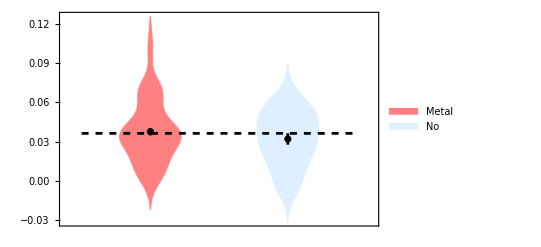

```mathematica
Show[
DistributionChart[{tabMETAL,tabNoMETAL},ChartLegends->{"Metal","No"},ChartStyle->{Pink,LightBlue}],
ErrorListPlot[{{1,Mean[tabMETAL],StandardDeviation[tabMETAL]/Sqrt[Length[tabMETAL]]},
{2,Mean[tabNoMETAL],StandardDeviation[tabNoMETAL]/Sqrt[Length[tabNoMETAL]]}},PlotStyle->Black],
ListPlot[{{0.5,Mean[Join[tabMETAL,tabNoMETAL]]},{2.5,Mean[Join[tabMETAL,tabNoMETAL]]}},PlotStyle->{Black,Dashed},Joined->True]

]
```

Phosphorous metabolism: Having or not having a mutation in a phosphorous metabolism gene does predict cross-tolerance:

```mathematica
tabPHO=Select[linephenotypes,#[[3]]=="PHO"&][[All,5]];
```

```mathematica
tabNoPHO=Select[linephenotypes,#[[3]]=="NO"&][[All,5]];
```

```mathematica
{Mean[tabPHO],Mean[tabNoPHO]}
```

{0.0430593,0.0328959}

```mathematica
{StandardDeviation[tabPHO]/Sqrt[Length[tabPHO]],StandardDeviation[tabNoPHO]/Sqrt[Length[tabNoPHO]]}
```

{0.00464377,0.00263299}

p-value of t-test:

```mathematica
TTest[{tabPHO,tabNoPHO}]
```

0.0430228

Violin plot with mean and SE:

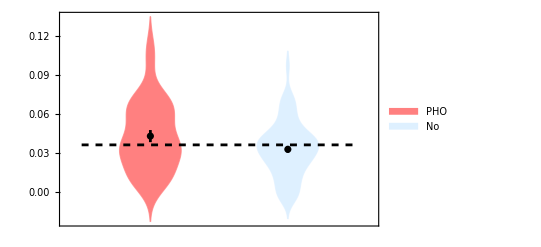

```mathematica
Show[
DistributionChart[{tabPHO,tabNoPHO},ChartLegends->{"PHO","No"},ChartStyle->{Pink,LightBlue}],
ErrorListPlot[{{1,Mean[tabPHO],StandardDeviation[tabPHO]/Sqrt[Length[tabPHO]]},
{2,Mean[tabNoPHO],StandardDeviation[tabNoPHO]/Sqrt[Length[tabNoPHO]]}},PlotStyle->Black],
ListPlot[{{0.5,Mean[Join[tabPHO,tabNoPHO]]},{2.5,Mean[Join[tabPHO,tabNoPHO]]}},PlotStyle->{Black,Dashed},Joined->True]

]
```

Repair: Having or not having a mutation in a repair gene does predict cross-tolerance:
[Not expected]

```mathematica
tabREPAIR=Select[linephenotypes,#[[4]]=="Repair"&][[All,5]];
```

```mathematica
tabNoREPAIR=Select[linephenotypes,#[[4]]=="NO"&][[All,5]];
```

p-value of t-test:

```mathematica
TTest[{tabREPAIR,tabNoREPAIR}]
```

0.841256

Violin plot with mean and SE:

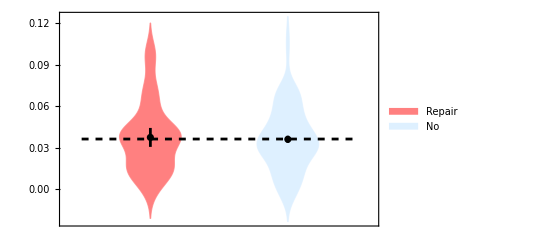

```mathematica
Show[
DistributionChart[{tabREPAIR,tabNoREPAIR},ChartLegends->{"Repair","No"},ChartStyle->{Pink,LightBlue}],
ErrorListPlot[{{1,Mean[tabREPAIR],StandardDeviation[tabREPAIR]/Sqrt[Length[tabREPAIR]]},
{2,Mean[tabNoREPAIR],StandardDeviation[tabNoREPAIR]/Sqrt[Length[tabNoREPAIR]]}},PlotStyle->Black],
ListPlot[{{0.5,Mean[Join[tabREPAIR,tabNoREPAIR]]},{2.5,Mean[Join[tabREPAIR,tabNoREPAIR]]}},PlotStyle->{Black,Dashed},Joined->True]

]
```

```mathematica
temp=Union[mat[[All,{2,8,9,10}]]]
```

{{ABP1,Metal,No,No},{ACB1,Metal,No,No},{ACC1,No,PHO,No},{ADE6,No,PHO,No},{ADR1,Metal,No,No},{AFT1,Metal,PHO,No},{AGP1,No,No,No},{AHK1,Metal,No,No},{ALD5,No,No,No},{ALY2,No,No,No},{APC2,No,No,No},{ARO3,No,No,No},{ASN1,No,No,No},{ATG11,Metal,No,No},{ATG2,Metal,No,No},{ATG39,No,No,No},{BDS1,No,No,No},{BIR1,No,No,No},{BLM10,Metal,No,Repair},{BNA6,No,PHO,No},{BNI1,Metal,No,No},{BNI4,Metal,No,No},{BRR2,No,No,No},{BSD2,Metal,No,No},{BUL1,Metal,No,No},{BUL2,Metal,No,No},{CAJ1,No,No,No},{CCC2,Metal,No,No},{CCR4,Metal,No,No},{CCW12,No,No,No},{CDC25,No,No,No},{CIC1,No,No,No},{CLB3,Metal,No,No},{CLN3,Metal,No,No},{CNE1,No,No,No},{COG1,Metal,No,No},{COG3,No,No,No},{COI1,No,No,No},{COQ1,No,No,No},{CPA1,No,No,No},{CSM3,No,No,Repair},{CUE3,No,No,No},{CWC22,No,No,No},{CWH41,Metal,No,No},{CYK3,No,No,No},{DAL2,No,No,No},{DBF20,No,No,No},{DBP10,No,No,No},{DDR48,Metal,No,Repair},{DNF1,No,No,No},{DOA4,Metal,No,No},{DOT6,No,No,No},{DSC2,No,No,No},{DSE4,No,No,No},{DUS4,No,No,No},{EBS1,No,No,No},{ECM14,No,No,No},{ECM22,Metal,No,No},{EFR3,No,No,No},{ELO3,Metal,No,No},{ERB1,No,No,No},{ERG1,No,No,No},{ERG27,No,No,No},{ERG7,No,No,No},{ERG9,No,PHO,No},{FAS2,No,No,No},{FAU1,No,No,No},{FCY2,No,No,No},{FET4,Metal,No,No},{FIG2,No,No,No},{FIG4,Metal,PHO,No},{FLC2,Metal,No,No},{FMP52,No,No,No},{FRE6,Metal,No,No},{FSF1,No,No,No},{FYV10,Metal,No,No},{FYV6,No,No,Repair},{FZF1,Metal,No,No},{GAS4,No,No,No},{GAT1,No,No,No},{GCD2,No,No,No},{GID12,Metal,No,No},{GPB1,No,No,No},{GPB2,Metal,No,No},{GPH1,Metal,No,No},{GSC2,No,No,No},{HBT1,No,No,No},{HEH2,Metal,No,No},{HHF2,No,No,No},{HIS4,Metal,No,No},{HMF1,No,No,No},{HO,No,No,No},{HOB2,No,No,No},{HRT3,No,No,No},{HSL1,Metal,No,No},{HSP104,No,No,No},{HUL5,Metal,No,No},{HXT13,No,No,No},{IDP1,Metal,PHO,No},{IES3,No,No,No},{ILV2,Metal,No,No},{IMA1,No,No,No},{INP2,No,No,No},{IOC4,No,No,No},{IPI3,No,No,No},{IRC20,No,No,Repair},{IRC8,No,No,No},{IST2,No,No,No},{ISU1,Metal,No,No},{ITC1,No,No,No},{KAR3,Metal,No,No},{KGD1,Metal,No,No},{KIN1,Metal,No,No},{KIN82,No,No,No},{KRE5,No,PHO,No},{KSP1,Metal,No,No},{KTR3,No,No,No},{LAM1,No,No,No},{LAM6,Metal,No,No},{LOS1,No,No,No},{LRG1,No,No,No},{MAM3,Metal,No,No},{MAS2,No,No,No},{MCK1,Metal,No,Repair},{MCM5,No,No,Repair},{MCT1,Metal,No,No},{MDH2,No,No,No},{MDL2,No,No,No},{MDM30,Metal,No,No},{MET10,No,No,No},{MET30,No,No,No},{MEX67,No,No,No},{MHP1,Metal,No,No},{MKT1,No,No,No},{MLF3,Metal,No,No},{MLH3,No,No,Repair},{MLS1,No,No,No},{MMS4,Metal,No,Repair},{MNN9,Metal,No,No},{MOT1,No,No,No},{MPA43,No,PHO,No},{MRL1,No,No,No},{MRPL36,Metal,No,No},{MSC6,No,No,No},{MSS2,No,No,No},{MTR4,No,No,No},{MYG1,Metal,No,No},{MYO2,Metal,No,No},{NAM8,Metal,No,No},{NAR1,No,No,No},{NFT1,No,No,No},{NGG1,Metal,No,No},{NIP100,No,No,No},{NPL3,Metal,No,No},{NSR1,No,No,No},{NUC1,Metal,No,No},{NUG1,No,No,No},{OAF1,Metal,No,No},{OCA4,No,No,No},{OCA5,No,No,No},{OPI1,No,PHO,No},{OSH2,No,No,No},{PBP2,Metal,No,No},{PBS2,Metal,No,No},{PCL5,No,No,No},{PDA1,Metal,PHO,No},{PDR1,No,No,No},{PDR10,No,No,Repair},{PDX1,No,PHO,No},{PET111,No,No,No},{PET127,No,No,No},{PEX2,No,No,No},{PFK26,No,PHO,No},{PHM7,No,No,No},{PHO23,Metal,No,No},{PHO81,No,PHO,No},{PHO84,Metal,PHO,No},{PIB1,No,No,No},{PKP1,No,No,No},{PLB2,No,PHO,No},{PMA1,No,No,No},{POL3,No,No,Repair},{PPQ1,Metal,No,No},{PRC1,No,No,No},{PRI1,No,No,No},{PRI2,No,No,Repair},{PRP2,No,No,No},{PRP8,No,No,No},{PTK2,Metal,No,No},{PYK2,Metal,PHO,No},{QRI7,No,No,No},{RAD16,Metal,No,Repair},{RAD17,No,No,Repair},{RAD26,No,No,Repair},{RBK1,Metal,PHO,No},{RCE1,No,No,No},{RCK2,Metal,No,No},{RCO1,Metal,No,No},{REC102,No,No,No},{RED1,No,No,No},{RHO1,No,No,No},{RIM11,Metal,No,No},{RIM21,Metal,No,No},{RKM3,No,No,No},{RMP1,No,No,No},{RNY1,Metal,No,No},{ROG1,No,No,No},{RPA135,No,No,No},{RPI1,No,No,No},{RPL22A,Metal,No,No},{RPL2A,No,No,No},{RPL39,Metal,No,No},{RPS15,No,No,No},{RPS2,No,No,No},{RPT5,No,No,No},{RRB1,No,No,No},{RRG7,No,No,No},{RRP46,No,No,No},{RRP6,No,No,No},{RSC1,Metal,No,Repair},{RSE1,No,No,No},{RTC2,No,No,No},{SAK1,Metal,No,No},{SAP4,No,No,No},{SBE2,Metal,No,No},{SEC8,No,No,No},{SET2,No,No,Repair},{SFP1,Metal,No,No},{SHP1,Metal,No,No},{SIW14,Metal,PHO,No},{SKN1,No,No,No},{SMC2,No,No,No},{SMY2,Metal,No,No},{SNF7,Metal,No,No},{SNT2,No,No,No},{SPC105,No,No,No},{SPO77,Metal,No,No},{SPS100,No,No,No},{SRP40,Metal,No,No},{SSE1,Metal,No,No},{SSK2,Metal,No,No},{SSQ1,Metal,No,No},{SSZ1,Metal,No,No},{STE5,Metal,No,No},{STP3,Metal,No,No},{STT3,No,No,No},{SUB2,No,No,Repair},{SUC2,No,No,No},{SUM1,Metal,No,No},{SWC5,Metal,No,No},{SWS2,No,No,No},{SWT1,No,No,No},{SYF2,No,No,No},{SYG1,Metal,No,No},{TAF8,No,No,No},{TAH11,No,No,Repair},{TAO3,No,No,No},{TCO89,Metal,No,No},{TFB1,No,No,Repair},{TFG1,No,No,No},{TIM54,No,No,No},{TOM1,Metal,No,No},{TOP1,Metal,No,No},{TOP2,No,No,No},{TOS3,No,No,No},{TPS3,Metal,No,No},{TRK2,Metal,No,No},{TRL1,No,No,No},{TUS1,Metal,No,No},{UBC1,No,No,No},{UBP5,No,No,No},{UBR2,Metal,No,No},{UBX7,Metal,No,No},{UGA3,No,No,No},{UGA4,No,No,No},{UIP5,No,No,No},{ULS1,No,No,Repair},{UME6,Metal,No,No},{URA2,No,PHO,No},{URB1,No,No,No},{USA1,No,No,No},{UTP21,No,No,No},{UTP8,No,No,No},{VBA1,No,No,No},{VCX1,Metal,No,No},{VHR2,No,No,No},{VID22,Metal,No,Repair},{VPS13,Metal,No,No},{VPS74,Metal,No,No},{VRP1,Metal,No,No},{VTC1,Metal,PHO,No},{VTC3,Metal,PHO,No},{VTC4,Metal,PHO,No},{VTC5,Metal,PHO,No},{WAR1,No,No,No},{YAP6,No,No,No},{YBR242W,No,PHO,No},{YBR292C,No,No,No},{YCF1,Metal,No,No},{YCK1,Metal,No,No},{YCT1,No,No,No},{YDL199C,No,No,No},{YDR003W-A,No,No,No},{YDR157W,No,No,No},{YDR541C,No,No,No},{YEF1,No,PHO,No},{YGR126W,No,No,No},{YGR130C,No,No,No},{YGR266W,No,No,No},{YHC1,No,No,No},{YHC3,No,No,No},{YIH1,No,No,No},{YIL092W,No,No,No},{YLR108C,No,No,No},{YLR296W,No,No,No},{YML119W,No,No,No},{YMR027W,No,No,No},{YOR029W,No,No,No},{YOR1,No,No,No},{YOR296W,Metal,No,No},{YOR343C,No,No,No},{YPK1,Metal,PHO,No},{YPL113C,No,No,No},{YPR078C,No,No,No},{YPR089W,No,No,No},{YPT6,Metal,No,No},{YRA1,No,No,Repair},{YRB2,No,No,No},{ZDS2,No,No,No},{ZRT1,Metal,No,No},{ZRT3,Metal,No,No}}

```mathematica
multihit={"CDC25","HUL5","MAM3","PHO84","PMA1","PTK2","SFP1","SIW14","VCX1","VTC4","VTC5","YGR130C","YOR1"};
```

```mathematica
Table[Flatten[Select[temp,#[[1]]==multihit[[i]]&]],{i,1,Length[multihit]}]//MatrixForm
```

(CDC25 | No | No | No
HUL5 | Metal | No | No
MAM3 | Metal | No | No
PHO84 | Metal | PHO | No
PMA1 | No | No | No
PTK2 | Metal | No | No
SFP1 | Metal | No | No
SIW14 | Metal | PHO | No
VCX1 | Metal | No | No
VTC4 | Metal | PHO | No
VTC5 | Metal | PHO | No
YGR130C | No | No | No
YOR1 | No | No | No)

#### Cross-tolerance by genes mutated in multiple metals

For the list of genes that were bore mutations in different metals, we might predict that they would be more cross tolerant.  Here we explore the relationship between these lines and the phenotypes of interest.

```mathematica
multiplemetalgenelist={"DNF1","FYV10","KSP1","MAM3","PDR1","PHO84","PMA1","PTK2","SFP1","VTC5","YLR296W","HUL5","PPQ1","SNT2","TOM1","YDL199C","YOR1"};
```

```mathematica
mat[[1]]
```

{CuBM18,ABP1,YCR088W,chrIII.265691,c.624A>C,p.Leu208Phe,MODERATE,Metal,No,No}

```mathematica
Select[mat,MemberQ[multiplemetalgenelist,#[[2]]]&];
```

```mathematica
linewithmultiplemetalhits=Union[%[[All,1]]]
```

{CdBM25,CdBM29,CdBM30,CdBM32,CdBM39,CdBM45,CdBM46,CdBM47,CoBM1,CoBM12,CoBM15,CoBM18,CoBM21,CoBM3,CoBM4,CoBM7,CoBM8,CuBM17,CuBM3,CuBM6,CuBM9,MnBM13,MnBM14,MnBM16,MnBM17,MnBM31,MnBM39,MnBM42,NiBM11,NiBM16,NiBM4,NiBM9,ZnBM11,ZnBM17,ZnBM19,ZnBM29,ZnBM37,ZnBM38,ZnBM41,ZnBM42,ZnBM43,ZnBM45,ZnBM46,ZnBM47}

This gets the phenotypes for the lines with and without hits in these genes:

```mathematica
withmultmetalhits=Select[linephenotypes,MemberQ[linewithmultiplemetalhits,#[[1]]]&];
withoutmultmetalhits=Select[linephenotypes,MemberQ[linewithmultiplemetalhits,#[[1]]]==False&];
```

For example:

```mathematica
withmultmetalhits[[1]]
```

{CdBM25,Metal,NO,NO,0.0390631}

Cross tolerance - No significant difference in broad cross tolerance:

```mathematica
{Mean[withmultmetalhits[[All,5]]],Mean[withoutmultmetalhits[[All,5]]]}
```

{0.0395263,0.0337043}

```mathematica
{StandardDeviation[withmultmetalhits[[All,5]]]/Sqrt[Length[withmultmetalhits[[All,5]]]],StandardDeviation[withoutmultmetalhits[[All,5]]]/Sqrt[Length[withoutmultmetalhits[[All,5]]]]}
```

{0.00332774,0.00334899}

```mathematica
TTest[{withmultmetalhits[[All,5]],withoutmultmetalhits[[All,5]]}]
```

0.225657

Metal resistance - There is significant association with metal resistance using a chi-squared goodness of fit test with df=1:
[Code from https://mathematica.stackexchange.com/questions/5271/doing-a-chi-square-independence-test-in-mathematica by whuber]

```mathematica
{Sort[Tally[withmultmetalhits[[All,2]]]],Sort[Tally[withoutmultmetalhits[[All,2]]]]}
```

{{{Metal,38},{NO,6}},{{Metal,37},{NO,17}}}

Compare the genic to intergenic mutations to the expected fraction using a chi-squared goodness of fit test with df=1:

```mathematica
data={{%[[1,1,2]],%[[1,2,2]]},{%[[2,1,2]],%[[2,2,2]]}};
rc={{"with","without"},{"yes","no"}};
TableForm[data,TableHeadings->rc]
fit=Outer[Times,Total[data,{2}],Total[data]]/Total[data,2];
(*TableForm[fit//N,TableHeadings->rc]*)
residual=data-fit;
(*TableForm[residual//N,TableHeadings->rc]*)
χ2array=residual^2/fit;
(*TableForm[χ2array//N,TableHeadings->rc]*)
χ2=Total[χ2array,2];
χ2//N
df=(Times@@#-Total[#]+1)&[Dimensions[data]];
pvalue=1-CDF[ChiSquareDistribution[df],χ2]//N;
Print["df=",df,",  p=",pvalue]
```

| yes | no
with | 38 | 6
without | 37 | 17

4.29855

df=1,  p=0.0381448

PHO metabolism - There is no significant association with phosphorous metabolism using a chi-squared goodness of fit test with df=1:
[Code from https://mathematica.stackexchange.com/questions/5271/doing-a-chi-square-independence-test-in-mathematica by whuber]

```mathematica
{Sort[Tally[withmultmetalhits[[All,3]]]],Sort[Tally[withoutmultmetalhits[[All,3]]]]}
```

{{{NO,26},{PHO,18}},{{NO,39},{PHO,15}}}

Compare the genic to intergenic mutations to the expected fraction using a chi-squared goodness of fit test with df=1:

```mathematica
data={{%[[1,1,2]],%[[1,2,2]]},{%[[2,1,2]],%[[2,2,2]]}};
rc={{"with","without"},{"yes","no"}};
TableForm[data,TableHeadings->rc]
fit=Outer[Times,Total[data,{2}],Total[data]]/Total[data,2];
(*TableForm[fit//N,TableHeadings->rc]*)
residual=data-fit;
(*TableForm[residual//N,TableHeadings->rc]*)
χ2array=residual^2/fit;
(*TableForm[χ2array//N,TableHeadings->rc]*)
χ2=Total[χ2array,2];
χ2//N
df=(Times@@#-Total[#]+1)&[Dimensions[data]];
pvalue=1-CDF[ChiSquareDistribution[df],χ2]//N;
Print["df=",df,",  p=",pvalue]
```

| yes | no
with | 26 | 18
without | 39 | 15

1.87181

df=1,  p=0.171268

Repair - There is no significant association with phosphorous metabolism using a chi-squared goodness of fit test with df=1:
[Code from https://mathematica.stackexchange.com/questions/5271/doing-a-chi-square-independence-test-in-mathematica by whuber]

```mathematica
{Sort[Tally[withmultmetalhits[[All,4]]]],Sort[Tally[withoutmultmetalhits[[All,4]]]]}
```

{{{NO,37},{Repair,7}},{{NO,47},{Repair,7}}}

Compare the genic to intergenic mutations to the expected fraction using a chi-squared goodness of fit test with df=1:

```mathematica
data={{%[[1,1,2]],%[[1,2,2]]},{%[[2,1,2]],%[[2,2,2]]}};
rc={{"with","without"},{"yes","no"}};
TableForm[data,TableHeadings->rc]
fit=Outer[Times,Total[data,{2}],Total[data]]/Total[data,2];
(*TableForm[fit//N,TableHeadings->rc]*)
residual=data-fit;
(*TableForm[residual//N,TableHeadings->rc]*)
χ2array=residual^2/fit;
(*TableForm[χ2array//N,TableHeadings->rc]*)
χ2=Total[χ2array,2];
χ2//N
df=(Times@@#-Total[#]+1)&[Dimensions[data]];
pvalue=1-CDF[ChiSquareDistribution[df],χ2]//N;
Print["df=",df,",  p=",pvalue]
```

| yes | no
with | 37 | 7
without | 47 | 7

0.171857

df=1,  p=0.678466